```mathematica
Frontend for the group tool
```

#### Frontend for the group tool

## Headers

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Mathlink integration and get functions

```mathematica
LinkClose[Link];
```

LinkObject::linkv: Argument Link in LinkClose[Link] is not a valid LinkObject.

```mathematica
Link=Install["./mathgroup"]
```

LinkObject[…]

```mathematica
LinkPatterns[Link]//TableForm
```

GetGroup(rank_Integer,type_String)
GetGroup(id_String)
GetReps(id_String,maxdim_Integer)
GetSubgroups(id_String)
GetRep(id_String)
GetRep(dimId_String,groupId_String)
GetSubgroup(id_String)
GetSubgroup(id_String,MixingId_String)
GetBreakingChains(SuperId_String,SubId_String)
GetDecomposeRep(RepId_String,SubgroupId_String,MixingId_String)
GetWeights(RepId_String)
GetDirectProduct(RepId1_String,RepId2_String)
GetInvariants(RepsId_String,dim_Integer)

```mathematica
?GetGroup
?GetReps
?GetSubgroups
?GetRep
?GetSubgroup
?GetBreakingChains
?GetDecomposeRep
?GetWeights
?GetDirectProduct
?GetInvariants
```

GetGroup[rank, type] gets the information of the group defined by rank and type.         GetGroup[id] gets the information of the group defined by id

GetReps[id, maxdim] gets the representations of the group identified by id up to dimension maxdim.

GetSubgroups[id] gets the subgroups of the group identified by id.

GetRep[id] gets the information of the rep defined by id.        GetRep[dimId, groupId] gets the information of the first rep of dimension dim of the group defined by groupId

GetSubgroup[id] gets the information of the subgroup defined by id and GetSubgroup[id, MixingId] gets the information of the subgroup defined by id with the mixing MixingId

GetBreakingChains[SuperId,SubId] gets all the breaking chains from the group defined by SuperId to the subgroup defined by SubId

GetDecomposeRep[RepId,SubgroupId,MixingId] decomposes the rep defined by RepId into the reps of the group defined by SubgroupId and the mixing matrix in MixingId

GetWeights[RepId] gets the weights from the representation defined by RepId

GetDirectProduct[RepId1,RepId2] calculates the direct product of the representations defined by RepId1 and RepId2

GetInvariants[RepsId,dim] builds the group invariants using the reps defined by RepsId up to dimension dim

## Object Orientation

```mathematica
NewGroup[id_]:=Module[{id2,group },
If[Length[StringSplit[id,"["]]>1 || Length[StringSplit[id,"("]]>1,
id2=StringSplit[id,"["][[1]];
id2=StringSplit[id2,"x"];
id2=StringJoin[Table[StringSplit[id2[[i]],"("][[1]]~~"x",{i,Length[id2]}]];
id2=StringDrop[id2,-1];,

id2=id;
];
If[Head[DBData[id2]]===DBData,
group = GetGroup[id2];
If[Length[StringCases[group,"Exception"]] > 0,Return[group]];
group=ImportString[group,"JSON"];
DBData["id"/.group]=group;,
group=DBData[id2];
];
"id"/.group
];
```

```mathematica
NewRep[id_,type_  : ""] :=Module[{rep,label},
If[Head[id]===String,
If[Head[DBData[id]]===DBData,
rep=GetRep[id];
If[Length[StringCases[rep,"Exception"]] > 0,Return[rep]];
rep=Append[ImportString[rep,"JSON"],"type"->type];
label = "label"/.rep;
While[Head[DBData[label]]===List &&(NumberForm["HWeight"/.DBData[label],1]≠NumberForm["HWeight"/.rep,1] || ("Group"/.DBData[label])≠("Group"/.rep) ||("type"/.DBData[label])≠type),
label=label<>"'";
];
DBData[label]=rep;
DBData[id]=rep;,

rep=DBData[id];
(*Print["DBData[",id,"] = ",rep];*)
label="label"/.(DBData[id]);
(*Print[type];*)
rep=DBData[label];
(*Print["DBData[",label,"] = ",rep];*)
(*Print[NumberForm["HWeight"/.DBData[id],1]."!=",NumberForm["HWeight"/.rep,1],"? ", NumberForm["HWeight"/.DBData[id],1]≠NumberForm["HWeight"/.rep,1]];
Print[("Group"/.DBData[id]),"≠",("Group"/.rep),"? ",("Group"/.DBData[id])≠("Group"/.rep)];*)
While[Head[DBData[label]]===List &&(NumberForm["HWeight"/.DBData[id],1]≠NumberForm["HWeight"/.rep,1] || ("Group"/.DBData[id])≠("Group"/.rep) ||("type"/.rep)≠type),
label=label<>"'";
rep=DBData[label];
(*Print["------>",label];
Print["------>",rep];*)
];
If[Head[DBData[label]]===DBData,
rep=DBData[id];
rep=Append[DeleteCases[rep,"label"->_],"label"->label];
rep=Append[DeleteCases[rep,"type"->_],"type"->type];
DBData[label]=rep;
];
(*Print[label];
Print[rep];*)
];

label,

NewRep[id,type,""]
]
];
```

```mathematica
NewRep[dim_,group_,type_ : ""] :=Module[{dimstring,rep,label},
If[Head[dim]===List,
dimstring=StringReplace[ExportString[dim,"JSON"],Whitespace->""];,
dimstring = StringReplace[ExportString[{dim},"JSON"],Whitespace->""];
];
rep=GetRep[dimstring,Attribute[group]["id"]];
rep=Append[ImportString[rep,"JSON"],"type"->type];
label="label"/.rep;
While[Head[DBData[label]]===List && (("id"/.DBData[label])≠("id"/.rep)|| ("Group"/.DBData[label])≠group ||("type"/.DBData[label])≠type),
label=label<>"'";
];
DBData[label]=rep;
DBData["id"/.rep]=rep;
label
];
```

```mathematica
NewSubgroup[id_,Mixing_ : {}]:= Module[{subgroup,label},
label=id;
If[Mixing≠{},
If[Head[DBData[id]]===DBData,
subgroup=GetSubgroup[id,StringReplace[ExportString[Mixing,"JSON"],Whitespace->""]];
subgroup=ImportString[subgroup,"JSON"];
subgroup=Append[subgroup,"Mixing"->Mixing];
DBData[id]=subgroup;,

subgroup=DBData[id];
While[Head[DBData[label]]===List&&Attribute[label]["Mixing"]≠"Mixing"&&Attribute[label]["Mixing"]≠Mixing,
label=label<>"'";
subgroup=DBData[label];
];
If[Head[DBData[label]]===DBData,
subgroup=GetSubgroup[id,StringReplace[ExportString[Mixing,"JSON"],Whitespace->""]];
subgroup=ImportString[subgroup,"JSON"];
DBData[label]=subgroup;,
If[Attribute[label]["Mixing"]=="Mixing",
subgroup=Append[subgroup,"Mixing"->Mixing];
DBData[label]=subgroup;
]
];
];,

If[Head[DBData[id]]===DBData || Head[DBData[id]]===ImportString,
subgroup=GetSubgroup[id];
subgroup=ImportString[subgroup,"JSON"];
subgroup=Append[subgroup,"Mixing"->Mixing];
DBData[id]=subgroup;,
subgroup=DBData[id];
];
];
label
];
```

```mathematica
NewTheory[Group_,Chain_,Reps_,Norm_ : 1]  := If[Norm==1,{"Group"->Group,"Chain"->Chain,"Reps"->Reps},{"Group"->Group,"Chain"->Chain,"Reps"->Reps,"Norm"->Norm}];
```

```mathematica
Attribute[obj_][attr_]:=If[Head[obj]===List,
If[attr===All,
DBData/@obj,
attr/.(DBData/@obj)
],
If[attr===All,
If[Head[DBData@obj]=== DBData,NewObject[obj]];
DBData@obj,
If[Head[DBData@obj]=== DBData,NewObject[obj]];
attr/.(DBData@obj)
]
]
```

```mathematica
SetAttribute[obj_][attr_][value_]:=Module[{object},
If[Head[DBData@obj]===DBData,NewObject[obj]];
object=DBData[obj];
If[!(Attribute[obj][attr]===attr),
object=DeleteCases[object,attr->_];
];
object=Append[object,attr->value];
DBData[obj]=object;
];
```

```mathematica
NewObject[Obj_]:=Module[{},
If[Head[DBData[Obj]]===DBData,
If[LetterQ[StringTake[Obj,1]],
If[Length[StringSplit[Obj,"("]]>1,
NewSubgroup[Obj],
NewGroup[Obj]
],
NewRep[Obj]
],
Obj
]
];
```

## Breaking functions

```mathematica
MakeTree[Chain_,level_ : 0] :=Module[{out,label,parent, son,branch,subbranches},
out={};
Table[
{parent,label}=StringSplit[Chain[[i,1,1]],"("];
parent = Attribute[parent]["label"];
parent =Subsuperscript[parent,StringDrop[label,-1],ToString[level]];
branch = Chain[[i,1,2]];
Table[
{son,label} = StringSplit[branch[[j,1,1]],"("];
son = Attribute[son]["label"];
son =Subsuperscript[son,StringDrop[label,-1],ToString[level+1]];
AppendTo[out,parent->son];,
{j,1,Length[branch]}];
subbranches = MakeTree[branch,level+1];
Table[
AppendTo[out,subbranches[[j]]];,
{j,Length[subbranches]}];,
{i,Length[Chain]}];
out
];
```

```mathematica
PrintTree[Chain_]:=Module[{Tree},
Tree=If[Head[Chain[[1]]]===List,MakeTree[Chain],Chain];
TreePlot[Tree,Automatic,Tree[[1,1]],ImageSize->300,VertexLabeling->True]
];
```

```mathematica
ChainDepth[Chain_] := Module[{Depth,SubChainDepth},
SubChainDepth = Table[ChainDepth[Chain[[i,1,2]]],{i,Length[Chain]}];
If[SubChainDepth≠{},Depth=Max[SubChainDepth]+1;,Depth=0;];
Depth
];
```

```mathematica
ChainLevel[Chain_,level_]:=Module[{Level},
Level={};
Table[
If[level==1,
AppendTo[Level,Chain[[i,1,1]]];,
Level=Join[Level,ChainLevel[Chain[[i,1,2]],level-1]];
];,
{i,Length[Chain]}];
Level
];
```

```mathematica
ChainWidth[Chain_]:=Module[{width,newwidth},
width=Length[Chain];
If[Length[Chain]>0,
newwidth=Sum[If[Length[Chain[[i,1,2]]]>0,ChainWidth[Chain[[i,1,2]]],1],{i,Length[Chain]}];
If[newwidth>width,width=newwidth];.10
];
width
];
```

```mathematica
BreakingChains[Group_,SubGroup_] :=Module[{Chains,Trees},
Chains=ImportString[GetBreakingChains[Group,SubGroup],"JSON"];
(*Chains=MixAbelians[Chains];*)
Trees=MakeTree/@Chains;
Print[{Table[PrintTree[Trees[[i]]],{i,Length[Trees]}]}//TableForm];
Chains
];
```

```mathematica
MakeChain[Subgroups_]:=Module[{groups,subgroups,label,chain,subchain,alphabet},
chain={};
alphabet=Characters["ABCDEFG"];
Do[
groups=StringSplit[StringSplit[Subgroups[[i]],"["][[1]],"x"];
If[Length[chain]>0,
chain=Table[
subchain=Reap[Table[
If[Length[groups]>1,
label=StringSplit[chain[[k,1,1]],{"(",")"}][[2]];
(*Check if there is a + sign *)
label=StringSplit[label,"+"];
label=Table[alphabet[[j]]==StringTrim[StringTake[label[[l]],{1}]],{l,Length@label}];
If[Or@@label,
Sow[chain[[k]]];
];,
Sow[chain[[k]]];
];,
{k,Length[chain]}
]][[2]];
If[Length[subchain]>0,
{groups[[j]]->subchain[[1]]},
{groups[[j]]->{}}
],
{j,Length[groups]}
];,
chain=Table[{groups[[j]]->{}},{j,Length[groups]}];
];,
{i,Length[Subgroups],1,-1}];
chain
];
```

```mathematica
CanBreak[Rep_,Chain_]:=Module[{subgroups,chain,pos,group,rank,subgroup,thereisbreaking,hweight},
If[IsSinglet[Rep],Return[False]];
rank=1;
subgroups=StringSplit[StringSplit[ExtractSubgroups[Chain][[1]],"["][[1]],"x"];
chain=Table[
Select[Chain,#[[1,1]]==subgroups[[i]]&][[1]],
{i,Length[subgroups]}];
And@@Table[
group=NewGroup@StringSplit[chain[[i,1,1]],"("][[1]];
subgroup = chain[[i,1,2]];
(* Check if there is breaking of this piece of the group *)
If[Length[subgroup]≠1,
thereisbreaking=True;,
subgroup = subgroup[[1,1,1]];
If[Length[StringCases[subgroup,"+"]]>0 ||group≠StringSplit[subgroup,"("][[1]],
thereisbreaking=True;,
thereisbreaking=False;
];
];

(* If there is breaking check that the rep is not a singlet *)
hweight=Attribute[Rep]["HWeight"][[1,rank;;rank+Attribute[group]["rank"]-1]];
rank += Attribute[group]["rank"];
If[Count[hweight,0]==Length[hweight],
If[thereisbreaking, False,True],
If[thereisbreaking,True,False]
],
{i,Length[chain]}
]
];
```

```mathematica
CalculateBreaking[Group_,Chain_,Reps_,OptionsPattern[]]:= Module[
{group,subgroup,reps,scalars,fermions,maxdim,semisimplesubgroup,breakingreps,subreps,mixing,labels,charges,othergroup},

Options[CalculateBreaking]={PrintOut->False};

group = NewGroup[Group];
subgroup=ExtractSubgroups[Chain][[2]];
reps=Reps;
fermions=Select[reps,Attribute[#]["type"]=="Fermion"&];
scalars=Select[reps,Attribute[#]["type"]!="Fermion"&];
If[OptionValue[PrintOut],
Print["Group = ",group];
Print["Subgroup = ",subgroup];
Print["Reps = ",reps];
Print["Scalars = ",scalars];
Print["Fermions = ",fermions];
];

(*If there is a + character in the subgroup, there is U(1) mixing *)
If[Length[StringCases[subgroup,"+"]]>0,
semisimplesubgroup = NewSubgroup[StringDrop[StringSplit[subgroup,"U"][[1]],-1]<>"["<>group<>"]"];
If[OptionValue[PrintOut],Print["Semisimple Subgroup = ", semisimplesubgroup]];

(* If any of the scalars is of greater dimension of the group reps, recalculate the group reps *)
If[Length[scalars]≠0,
(*maxdim=Max[Table[Attribute[scalars[[i]]]["dim"],{i,Length[scalars]}]];
If[Attribute[group]["repsMaxDim"]<maxdim,
SetAttribute[group]["Reps"][GroupReps[group,maxdim,ReturnType->"id"]];
];*)
(*breakingreps=Select[FindBreakingReps[group,semisimplesubgroup,maxdim,PrintOut->OptionValue[PrintOut]],MemberQ[scalars,#]&]*)
breakingreps=Reap[Table[
If[CanBreak[scalars[[i]],Chain] ,
subreps=DecomposeReps[scalars[[i]],semisimplesubgroup];
If[ContainsSinglet[subreps],
If[OptionValue[PrintOut],Print[scalars[[i]]," contains singlet"]];
(* Check that the rep is not a singlet under intermediate groups *)
If[Attribute[group]["rank"]>Attribute[semisimplesubgroup]["rank"] && Attribute[scalars[[i]]]["dim"]==Attribute[group]["dim"],
If[OptionValue[PrintOut],Print[scalars[[i]], " cannot break because it is adjoint"]];,
Sow[scalars[[i]]];
];
];
];,
{i,Length[scalars]}
]][[2]];,
breakingreps={};
];
If[OptionValue[PrintOut],Print["Breaking reps = ",breakingreps]];

(* Calculate the mixing of the U(1)s *)
labels=StringSplit[StringSplit[StringSplit[subgroup,"("][[-1]],")"][[1]],"+"];
mixing = Table[
charges=Table[
othergroup=StringSplit[semisimplesubgroup,"["][[1]]<>"xU1("<>labels[[j]]<>")["<>group<>"]";
Attribute[Select[DecomposeReps[breakingreps[[i]],othergroup],Attribute[#]["dim"]==1&][[1]]]["HWeight"][[1,-1]],
{j,Length[labels]}];
(* In case of two U(1) mixing *)
If[OptionValue[PrintOut],Print["Charges = ",charges]];
If[charges[[2]]==0, {0,1},{1,-charges[[1]]/charges[[2]]}],
{i,Length[breakingreps]}
];
If[OptionValue[PrintOut],Print["Mixing = ",mixing]];
subreps = Reap[Table[
subgroup=NewSubgroup[subgroup,mixing[[i]]];
If[ContainsSinglet[DecomposeReps[breakingreps[[i]],subgroup,mixing[[i]]]],
Sow[Join[DecomposeReps[fermions,subgroup,mixing[[i]]],DecomposeReps[DeleteCases[scalars,breakingreps[[i]],{1},1],subgroup,mixing[[i]]]]];
];,{i,Length[breakingreps]}
]][[2]];
If[Length[subreps]==0,
Return[{}],
subreps=subreps[[1]];
];,

(* There is no U1 mixing here *)
subgroup=NewSubgroup[subgroup];
(* If any of the scalars is of greater dimension of the group reps, recalculate the group reps *)
If[Length[scalars]≠0,
(*maxdim=Max[Table[Attribute[scalars[[i]]]["dim"],{i,Length[scalars]}]];
If[Attribute[group]["repsMaxDim"]<maxdim,
SetAttribute[group]["Reps"][GroupReps[group,maxdim,ReturnType->"id"]];
];*)
(*breakingreps=Select[FindBreakingReps[group,subgroup,maxdim,PrintOut->OptionValue[PrintOut]],MemberQ[scalars,#]&];*)
breakingreps=Reap[Table[
If[CanBreak[scalars[[i]],Chain] ,
subreps=DecomposeReps[scalars[[i]],subgroup];
If[ContainsSinglet[subreps],
If[OptionValue[PrintOut],Print[scalars[[i]]," contains singlet"]];
(* Check that the rep is not a singlet under intermediate groups *)
If[Attribute[group]["rank"]>Attribute[subgroup]["rank"] && Attribute[scalars[[i]]]["dim"]==Attribute[group]["dim"],
If[OptionValue[PrintOut],Print[scalars[[i]], " cannot break because it is adjoint"]];,
Sow[scalars[[i]]];
];
];
];,
{i,Length[scalars]}
]][[2]];,
breakingreps={};
];
If[OptionValue[PrintOut],Print["Breaking reps = ",breakingreps]];
subreps=Table[Join[DecomposeReps[fermions,subgroup],DecomposeReps[DeleteCases[scalars,breakingreps[[i]],{1},1],subgroup]],{i,Length[breakingreps]}];
mixing={};
];
If[mixing≠{},
Table[{"Reps"->subreps[[i]],"Mixing"->mixing[[i]]},{i,Length[subreps]}],
Table[{"Reps"->subreps[[i]]},{i,Length[subreps]}]
]
];
```

```mathematica
(*This doesn't work because the reps have U(1) charge = 1 and these do not break the group *)
FindBreakingReps[Group_,SubGroup_,MaxDim_,OptionsPattern[]]:=Module[{group, subgroup,chain,reps,subreps,intermediatesubgroups,breakingreps},
group = NewGroup[Group];
subgroup=NewSubgroup[SubGroup];
Print[group];
Print[subgroup];
Options[FindBreakingReps]={PrintOut->False};

If[MemberQ[Attribute[group]["Subgroups"],subgroup],

chain=MakeChain[{group,subgroup}];
reps = Attribute[group]["Reps"];
reps=Table[NewRep[reps[[i]],"Scalar"],{i,Length[reps]}];
reps=Select[reps,Attribute[#]["dim"]≤MaxDim &];
intermediatesubgroups={};
breakingreps=Reap[Table[
If[CanBreak[reps[[i]],chain] ,
subreps=DecomposeReps[reps[[i]],subgroup];
If[ContainsSinglet[subreps],
If[OptionValue[PrintOut],Print[reps[[i]]," contains singlet"]];
(* Check that the rep is not a singlet under intermediate groups *)
(*If[Length[intermediatesubgroups]≠0,*)
If[Attribute[group]["rank"]>Attribute[subgroup]["rank"] && Attribute[reps[[i]]]["dim"]==Attribute[group]["dim"],
If[OptionValue[PrintOut],Print[reps[[i]], " cannot break because it is adjoint"]];,
(*If[intermediatesubgroups=={},intermediatesubgroups=Select[Attribute[group]["Subgroups"],Attribute[NewSubgroup[#]]["dim"]>Attribute[subgroup]["dim"] && IsSubgroupOf[#,subgroup]&];];*)
(*If[Not@@Table[ContainsSinglet@DecomposeReps[reps[[i]],intermediatesubgroups[[j]]],{j,Length[intermediatesubgroups]}],
If[OptionValue[PrintOut],Print[reps[[i]], " can break"]];
Sow[reps[[i]]];,
If[OptionValue[PrintOut],Print[reps[[i]], " cannnot break"]];
];*)
Sow[reps[[i]]];
];
];
];,
{i,Length[reps]}
]][[2]];
If[Length[breakingreps]==0,
Return[{}],
breakingreps=breakingreps[[1]];
];
breakingreps,
Print[SubGroup, "is not a subgroup of ",Group];
]
];
```

## Rep functions

```mathematica
GroupReps[Group_,MaxDim_,OptionsPattern[]]:=Module[{group,maxdim,reps},

Options[GroupReps]={ReturnType->"label"};
group=Group;
maxdim=If[MaxDim==0,50,MaxDim];

reps=GetReps[Attribute[Group]["id"],If[IntegerQ[MaxDim],MaxDim,Round[MaxDim]]];
reps=ImportString[reps,"JSON"];
If[OptionValue[ReturnType]=="label",
reps=Table[NewRep[reps[[i]]],{i,Length[reps]}];
];
reps

];
```

```mathematica
WeightDiagram[Rep_]:=Module[{weights},
If[Attribute[Rep]["Weights"]=={},
weights=ImportString[GetWeights[Attribute[Rep]["id"]],"JSON"];,
weights=Attribute[Rep]["Weights"];
];
weights
]
```

```mathematica
DirectProduct[Rep1_,Rep2_]:=Module[{product},
product = ImportString[GetDirectProduct[Attribute[Rep1]["id"],Attribute[Rep2]["id"]],"JSON"];
Table[NewRep[product[[i]],Attribute[Rep1]["type"]],{i,Length[product]}]
]
```

```mathematica
DecomposeReps[Reps_,Subgroup_,Mixing_ : {},OptionsPattern[]]:=Module[{data,repstring,decomposition},
Options[DecomposeReps]={DeBug->False};
If[Length[StringCases[Subgroup,"+"]]>0 &&Length[Mixing]==0,
Return["Missing U(1) mixing parameters"];
];
If[Head[Reps]===List,

(* If it is a list, treat it as a list *)
Flatten[Table[
data=If[Mixing=={},DBData[Reps[[i]],Subgroup],DBData[Reps[[i]],Subgroup,Mixing]];
If[OptionValue[DeBug],Print[data]];

(* If the info is not on the DB, calculate it, otherwise pull it *)
If[Head[data] === DBData,
repstring=GetDecomposeRep[Attribute[Reps[[i]]]["id"],OrderSubgroup[Subgroup],StringReplace[ExportString[Mixing,"JSON"],Whitespace->""]];
repstring = ImportString[repstring,"JSON"];
decomposition=Table[
NewRep[repstring[[j]],Attribute[Reps[[i]]]["type"]],
{j,Length[repstring]}];

(*Add it to the DB *)
If[Mixing == {},
DBData[Reps[[i]],Subgroup]=decomposition;
If[OptionValue[DeBug],Print["DBData[",Reps[[i]],",",Subgroup,"] = ",DBData[Reps[[i]],Subgroup]]];,
DBData[Reps[[i]],Subgroup,Mixing]=decomposition;
If[OptionValue[DeBug],Print["DBData[",Reps[[i]],",",Subgroup,",",Mixing,"] = ",DBData[Reps[[i]],Subgroup,Mixing]]];
];,
decomposition=data
];

decomposition,
{i,Length[Reps]}],1],

(* If it's not a list, make it a list *)
DecomposeReps[{Reps},Subgroup,Mixing]
]
];
```

```mathematica
Invariants[Reps_,dim_]:=Module[{reps,invariants},
reps=Table[Attribute[Reps[[i]]]["id"],{i,Length[Reps]}];
reps=StringReplace[ExportString[reps,"JSON"],Whitespace->""];
invariants=GetInvariants[reps,dim];
invariants=ImportString[invariants,"JSON"];
Table[Table[NewRep[invariants[[i,j]]],{j,Length[invariants[[i]]]}],{i,Length[invariants]}]
]
```

```mathematica
GenerateReps[Reps_,nReps_,Mixing_ : {}]:=Module[{fermions,scalars,reps,genreps},
reps={};
If[Head[Reps]===List && Length[Reps]>0,
If[Head[Reps[[1]]]===List,
If[Mixing ≠ {},
Table[reps=Join[reps,GenerateReps[Reps[[i]],nReps,Mixing[[i]]]];,{i,Length[Reps]}];,
Table[reps=Join[reps,GenerateReps[Reps[[i]],nReps]];,{i,Length[Reps]}];
];,
fermions=Select[Reps,Attribute[#]["type"]=="Fermion" &];
scalars=Select[Reps,Attribute[#]["type"]=="Scalar" &];
reps=If[nReps===All,
Subsets[scalars],
Subsets[scalars,nReps]
];
If[Mixing≠{},
reps=Table[{"Reps"->Join[fermions,reps[[i]]],"Mixing"->Mixing},{i,Length[reps]}];,
reps=Table[{"Reps"->Join[fermions,reps[[i]]]},{i,Length[reps]}];
];
];
];
reps
];
```

```mathematica
NormaliseRepstoSM[Reps_]:=Module[{SMReps,SMQuarkD, RepsQuarkD,Norm,HWeight,reps,time},
SMReps=SMreps;

SMQuarkD=Select[SMReps,Attribute[#]["dim"]==6&][[1]];
RepsQuarkD=Select[Reps,Attribute[#]["dim"]==6&&Attribute[#]["type"]=="Fermion"&][[1]];

If[Attribute[RepsQuarkD]["HWeight"][[1,-1]]==0,Return[{}]];

Norm =√(3/5) Attribute[SMQuarkD]["HWeight"][[1,-1]]/Attribute[RepsQuarkD]["HWeight"][[1,-1]];

time=SessionTime[];
blah=0;
reps={Table[
time1=SessionTime[];
HWeight=Attribute[Reps[[i]]]["HWeight"][[1]];
HWeight[[-1]]*=Norm;
HWeight=StringReplace[ToString[HWeight],{"{"->"(","}"->")"}]<>Attribute[SMQuarkD]["Group"];
(*Print["1=",SessionTime[]-time1];*)
time2=SessionTime[];
rep=NewRep[HWeight,Attribute[Reps[[i]]]["type"]];
blah+=SessionTime[]-time1;
(*Print["2=",SessionTime[]-time2]*);
rep,
{i,Length[Reps]}],Norm};
(*Print["blah=",blah];*)
(*Print["totaltime=",SessionTime[]-time];*)
reps
];
```

```mathematica
NormaliseReps[Reps_,Norm_]:=Module[{HWeight},
Table[
HWeight=Attribute[Reps[[i]]]["HWeight"][[1]];
HWeight[[-1]]*=Norm;
HWeight=StringReplace[ToString[HWeight],{"{"->"(","}"->")"}]<>Attribute[Reps[[1]]]["Group"];
NewRep[HWeight,Attribute[Reps[[i]]]["type"]],
{i,Length[Reps]}]
];
```

```mathematica
I
```

```mathematica
NormaliseMixing[Group_,Subgroup_,Mixing_,Norm_]:= Module[{Mix,Labels,Indices,Pos,Norm2},
If[Head[Mixing]===String,Return[Mixing]];
(* Only checked for the A1xU1->U1 and U1xU1->U1 cases *)
Mix=Norm*Mixing;
Norm2=1;
If[Length[Position[StringSplit[StringSplit[Group,"["][[1]],"x"],"U1"]]>0,
(* If there is a U1, find which of the mixing entries corresponds to it and renormalise its mixing to force a^2 + b^2 = 1 *)
Labels=StringSplit[StringSplit[StringSplit[Subgroup,"("][[-1]],")"][[1]],"+"];
Indices=ToCharacterCode[Labels][[All,1]]-64;
Pos=FirstPosition[StringSplit[Group,"x"][[Indices]],"U1"][[1]];
If[Mix[[Pos]]≠0,
Norm2=Mix[[Pos]];
Mix[[Pos]]=√(1-Mix[[-Pos]]^2);
Norm2/=Mix[[Pos]];
];
];
{Mix,Norm2}
];
```

## Subgroup functions

```mathematica
Abelians[Subgroup_]:=Module[{groups,abelians},
groups=StringSplit[StringSplit[Subgroup,"["][[1]],"x"];
abelians=Reap[Table[If[StringSplit[groups[[i]],"("][[1]]=="U1",Sow[groups[[i]]];];,{i,Length[groups]}]][[2]];
If[Length[abelians]≠0,abelians[[1]],abelians]
];
```

```mathematica
ExtractSubgroups[Chain_]:=Module[{nsubgroups,supgroup,subgroups,level,subgroup},
nsubgroups=ChainDepth[Chain];
supgroup="";
subgroups= Table[
subgroup ="";
If[i==1,
level=ChainLevel[Chain,i];,
level=DeleteDuplicates[ChainLevel[Chain,i]];
];
Table[
subgroup=subgroup<>level[[j]]<>"x";,
{j,Length[level]-1}];
subgroup=subgroup<>level[[Length[level]]];
subgroup=OrderSubgroup[subgroup];
If[i≠1,subgroup = subgroup<>"["<>supgroup<>"]"];
supgroup="";
Table[
supgroup = supgroup<>StringSplit[level[[j]],"("][[1]]<>"x";,
{j,Length[level]-1}];
supgroup = supgroup<>StringSplit[level[[Length[level]]],"("][[1]];
subgroup,
{i,nsubgroups}];
subgroups
];
```

```mathematica
OrderGroup[Group_]:=Module[{group,groups,toswap,i,out},
If[Head[Group]===List,
groups  =Group;,
groups=StringSplit[Group,"x"];
];
Table[
toswap=i;
Table[
If[Attribute[groups[[toswap]]]["rank"]<Attribute[groups[[j]]]["rank"],
toswap=j;,
If[Attribute[groups[[toswap]]]["rank"]==Attribute[groups[[j]]]["rank"],
If[Attribute[groups[[toswap]]]["dim"]<Attribute[groups[[j]]]["dim"],
toswap=j;
];
];
];,
{j,i+1,Length[groups]}
];

If[toswap≠i,
group = groups[[toswap]];
groups=ReplacePart[groups,{toswap->groups[[i]],i->group}];
];,
{i,Length[groups]}
];
out="";
Table[out=out<>Attribute[groups[[i]]]["id"]<>"x",{i,Length[groups]-1}];
out=out<>Attribute[groups[[Length[groups]]]]["id"];
out
];
```

```mathematica
OrderSubgroup[Subgroup_] := Module[{subgroup,ending,id,idlabel,groups,toswap,k,label1,label2,alphabet,group,out},
If[StringTake[Subgroup,-1]=="]",
subgroup=StringSplit[Subgroup,"["][[1]];
ending=StringSplit[Subgroup,"["][[2]];,
subgroup=Subgroup;
];
subgroup=StringSplit[subgroup,"x"];
If[Length[StringSplit[subgroup[[1]],"("]]==1,Return[OrderGroup[subgroup]]];

If[Length[subgroup]==1,Return[Subgroup]];

groups=Table[
id=NewGroup[StringSplit[subgroup[[i]],"("][[1]]];
idlabel=StringDrop[StringSplit[subgroup[[i]],"("][[2]],-1];
DBData[id<>"("<>idlabel<>")"]=Append[Attribute[id][All], "idlabel"->idlabel];
id<>"("<>idlabel<>")",
{i,Length[subgroup]}
];
Table[
toswap=i;
Table[
If[Attribute[groups[[toswap]]]["rank"]<Attribute[groups[[j]]]["rank"],
toswap=j;,
If[Attribute[groups[[toswap]]]["rank"]==Attribute[groups[[j]]]["rank"],
If[Attribute[groups[[toswap]]]["dim"]<Attribute[groups[[j]]]["dim"],
toswap=j;,
If[Attribute[groups[[toswap]]]["dim"]==Attribute[groups[[j]]]["dim"],
k=1;
label1=Attribute[groups[[toswap]]]["idlabel"];
label2=Attribute[groups[[j]]]["idlabel"];
While[k<StringLength[label1] && k<StringLength[label2] &&StringTake[label1,{k}]==StringTake[label2,{k}],k++];
alphabet=Characters["ABCDEFG"];
If[Position[alphabet,StringTake[label1,{k}]][[1,1]]>Position[alphabet,StringTake[label2,{k}]][[1,1]],
toswap=j;
];
];
];
];
];,
{j,i+1,Length[subgroup]}
];


If[toswap≠i,
group = groups[[toswap]];
groups=ReplacePart[groups,{toswap->groups[[i]],i->group}];
];,
{i,Length[subgroup]}
];

out="";
Table[out=out<>Attribute[groups[[i]]]["id"]<>"("<>Attribute[groups[[i]]]["idlabel"]<>")"<>"x",{i,Length[groups]-1}];
out=out<>Attribute[groups[[Length[groups]]]]["id"]<>"("<>Attribute[groups[[Length[groups]]]]["idlabel"]<>")";
If[StringTake[Subgroup,-1]=="]"&& StringTake[Subgroup,-2] ≠ "[]",
If[Length[StringSplit[ending,"x"]]>1,
ending=NewGroup[StringDrop[ending,-1]];,
ending=StringDrop[ending,-1];
];
out<>"["<>ending<>"]",
out
]

];
```

```mathematica
IsSubgroupOf[Group_,Subgroup_]:=Module[{group,subgroup,subgroups},
group = NewGroup[Group];
subgroup=NewGroup[Subgroup];
If[Attribute[group]["rank"]≤ Attribute[subgroup]["rank"],Return[False]];
If[Attribute[group]["dim"]≤ Attribute[subgroup]["dim"],Return[False]];
subgroups=Attribute[NewGroup[Group]]["Subgroups"];
subgroups=Table[NewGroup[subgroups[[i]]],{i,Length[subgroups]}];
MemberQ[subgroups,subgroup]
];
```

## Constraint checks

```mathematica
ContainsSM[reps_,OptionsPattern[]] := Module[{LowEnTheory,SMReps,Reps,Pos,Norm,Charge,Id,Deleted,Out},

Options[ContainsSM]={PrintOut->False,PurgeColour->False};

Out = True;
Reps=reps;

(* Recast the hypercharge normalisation of the SMreps *)
Pos=FirstPosition[Reps,SelectFirst[Reps,Attribute[#]["dim"]==1&&Attribute[#]["HWeight"][[1,-1]]≠0&]][[1]];
Norm = Attribute[Reps[[Pos]]]["HWeight"][[1,-1]]/Attribute[SMreps[[13]]]["HWeight"][[1,-1]];
If[OptionValue[PrintOut],Print[Norm]];

SMReps=Table[
Charge =SetAccuracy[Attribute[SMreps[[i]]]["HWeight"][[1,-1]]*Norm,6];
Id = StringSplit[Attribute[SMreps[[i]]]["id"],","];
Id=Id[[1]]<>", "<>Id[[2]]<>", "<>Id[[3]]<>","<>ToString[Charge]<>")A2xA1xU1";
(*Print[Id];
Print[Attribute[SMreps[[i]]]["type"]];*)
NewRep[Id,Attribute[SMreps[[i]]]["type"]],
{i,Length[SMreps]}];

If[OptionValue[PrintOut],
Print[SMReps];
Print[Reps];
];
If[Length[SMReps]>Length[Reps], Return[False]];

(* Check if the SM is contained *)
Deleted=0;
Do[
Pos=FirstPosition[Reps,SMReps[[i]]];
If[OptionValue[PrintOut],Print[Pos]];
If[Head[Pos]===Missing,Return[False];,Reps=Delete[Reps,Pos];];
Deleted++;,
{i,Length[SMReps]}];
If[Deleted≠Length[SMReps],Out=False;Return[False]];

(* Check if there is non-singlet exotics *)
(*Switch[mode,
"Only",
Do[
If[!IsSinglet[Reps[[i]]], Out=False;Return[False];];,
{i,Length[Reps]}
];,
"At Least",
Return[True];
];*)

(* Check if there are colour-charged reps *)
If[OptionValue[PurgeColour],
Do[
If[!IsSinglet[Reps[[i]],1],Out=False;Return[False];];,
{i,Length[Reps]}
];
];

Return[Out];
];
```

```mathematica
IsSinglet[Rep_]:=Module[{group,rank},
rank=1;
And@@Table[
group=NewGroup@StringSplit[Attribute[Rep]["Group"],"x"][[i]];
rank += Attribute[group]["rank"];
If[Attribute[Rep]["dim"]==1,
If[Attribute[group]["type"]=="U",
If[SetAccuracy[Attribute[Rep]["HWeight"][[1,rank-Attribute[group]["rank"]]],4]==0,
True,
False],
True],
False],
{i,Length[StringSplit[Attribute[Rep]["Group"],"x"]]}
]
];
```

```mathematica
IsSinglet[Rep_,GroupPos_]:=Module[{group,rank,bool},
If[GroupPos>Length[StringSplit[Attribute[Rep]["Group"],"x"]],Return[False]];
If[IsSinglet[Rep],Return[True]];
rank=1;
Table[
group=NewGroup@StringSplit[Attribute[Rep]["Group"],"x"][[i]];
If[i==GroupPos,
bool=And@@Table[If[SetAccuracy[Attribute[Rep]["HWeight"][[1,rank+j-1]],4]==0,True,False],{j,Attribute[group]["rank"]}];,
rank+=Attribute[group]["rank"];
];,
{i,GroupPos}
];
Return[bool];
];
```

```mathematica
ContainsSinglet[Reps_]:=Or@@IsSinglet/@Reps;
```

```mathematica
AnomalyCancellation[Reps_,OptionsPattern[]]:=Module[{groups,trianglediagrams,tdgroups,anomaly,reps,rep,weight, rank},

Options[AnomalyCancellation]={PrintOut->False};

(* Anomaly Calculation, only valid for one U(1) factor *)
groups = StringSplit[Attribute[Reps[[1]]]["Group"],"x"];
trianglediagrams=DeleteDuplicates[Sort/@Tuples[Table[i,{i,Length[groups]}],3]];
tdgroups=Table[{groups[[trianglediagrams[[i,1]]]],groups[[trianglediagrams[[i,2]]]],groups[[trianglediagrams[[i,3]]]]},{i,Length[trianglediagrams]}];
And@@Table[
anomaly=Switch[Length[Cases[tdgroups[[i]],"U1"]],
0,If[trianglediagrams[[i,1]]==trianglediagrams[[i,2]]&&trianglediagrams[[i,1]]==trianglediagrams[[i,3]],
If[Attribute[tdgroups[[i,1]]]["type"]=="A"&&Attribute[tdgroups[[i,1]]]["rank"]>1,
(* Calculate the anomaly for a general gauge group, MISSING *)
Sum[
rank=1;
Table[weight=Attribute[Reps[[j]]]["HWeight"][[1,rank;;rank-1+Attribute[groups[[k]]]["rank"]]]; rank+=Attribute[groups[[k]]]["rank"],{k,trianglediagrams[[i,1]]}];
rep=NewRep["("<>StringDrop[StringDrop[ToString[weight],1],-1]<>")"<>tdgroups[[i,1]],Attribute[Reps[[j]]]["type"]];
If[Attribute[rep]["real"],0,
Switch[Attribute[tdgroups[[i,1]]]["rank"],
2,(* SU(3) *)
Switch[Attribute[rep]["dim"],
3,If[Attribute[rep]["conjugate"]==0,1,-1],
_,0
],
3, (* SU(4) *)
Switch[Attribute[rep]["dim"],
4,If[Attribute[rep]["conjugate"]==0,1,-1],
_,0
],
4, (* SU(5) *)
Switch[Attribute[rep]["dim"],
5,If[Attribute[rep]["conjugate"]==0,1,-1],
10,If[Attribute[rep]["conjugate"]==0,1,-1],
_,0
]
]]*Attribute[Reps[[j]]]["dim"]/Attribute[rep]["dim"],
{j,Length[Reps]}],
0
],
0
],
1,If[trianglediagrams[[i,1]]≠trianglediagrams[[i,2]],0,
reps=Select[Reps,!IsSinglet[#,trianglediagrams[[i,1]]]&];
Sum[Attribute[reps[[i]]]["dim"]Attribute[reps[[i]]]["HWeight"][[1,-1]],{i,Length[reps]}]],
2,0,
3,Sum[Attribute[Reps[[i]]]["dim"]Attribute[Reps[[i]]]["HWeight"][[1,-1]]^3,{i,Length[Reps]}]
];

If[Abs[anomaly]<0.001,
True&&GravitationalAnomalyCancellation[Reps]&&WittenAnomalyCancellation[Reps],
False],
{i,Length[trianglediagrams]}
]
];
```

```mathematica
WittenAnomalyCancellation[Reps_,OptionsPattern[]]:=Module[{group,rank,witten},

Options[WittenAnomalyCancellation]={PrintOut->False};
rank=1;

And@@Table[
group=NewGroup@(StringSplit[Attribute[Reps[[1]]]["Group"],"x"][[i]]);
witten=If[Attribute[group]["type"]=="A" &&Attribute[group]["rank"]==1,
EvenQ[Sum[
Attribute[Reps[[j]]]["HWeight"][[1,rank]]*Attribute[Reps[[j]]]["dim"]/(Attribute[Reps[[j]]]["HWeight"][[1,rank]]+1),
{j,Length[Reps]}]],
True
 ];
rank+=Attribute[group]["rank"];
If[!witten && OptionValue[PrintOut],Print["WITTEN ANOMALY NOT SATISFIED"]];
witten,
{i,Length[StringSplit[Attribute[Reps[[1]]]["Group"],"x"]]}
]
];
```

```mathematica
GravitationalAnomalyCancellation[Reps_,OptionsPattern[]]:=Module[{group,nabelians,charge},

Options[GravitationalAnomalyCancellation]={PrintOut->False};

group=NewGroup@Attribute[Reps[[1]]]["Group"];
nabelians = If[Attribute[group]["nabelians"]≠"nabelians" ,Attribute[group]["nabelians"] , If[Attribute[group]["abelian"]≠"abelian" && Attribute[group]["abelian"],1,0]];
If[nabelians<1,Return[True]];

And@@Table[
charge=Sum[
Attribute[Reps[[i]]]["HWeight"][[1,-j]] * Attribute[Reps[[i]]]["dim"],
{i,Length[Reps]}
];
If[Abs[charge]<0.01,
True,
If[OptionValue[PrintOut],Print["CHARGE CONSERVATION NOT SATISFIED, CHARGE: ",charge]];
False
],
{j,nabelians}
]
]
```

```mathematica
Chirality[Reps_,OptionsPattern[]]:=And@@Table[

Options[Chirality]={PrintOut->False};

If[Attribute[Reps[[i]]]["type"]=="Fermion",
If[Attribute[Reps[[i]]]["dim"]<3||Attribute[Reps[[i]]]["real"]==False,
True,
If[OptionValue[PrintOut],Print["CHIRALITY NOT SATISFIED"]];
False
],
True
],
{i,Length[Reps]}
];
```

```mathematica
CheckConstraints[Reps_,OptionsPattern[]]:=Module[{},

Options[CheckConstraints]={PrintOut->False};

If[Chirality[Reps,PrintOut->OptionValue[PrintOut]],
If[OptionValue[PrintOut],Print["CHIRALITY SATISFIED"]];
True,
False
]
];
```

## Proton Decay

```mathematica
ProtonDecay[Model_]:=Module[{model,subgroups,group,reps,gaugereps,pdecay},
Table[
model=Model[[i]];
reps="Reps"/.model;
reps=Select[reps,Attribute[#]["type"]=="Scalar" &];
subgroups=ExtractSubgroups["Chain"/.model];
group=NewGroup[subgroups[[1]]];
If[Attribute[group]["Adjoint"]=="Adjoint",
If[Head[Attribute[group]["ngroups"]]===String || Attribute[group]["ngroups"]==1,
gaugereps=NewRep[Attribute[group]["dim"],group,"Scalar"];,
gaugereps=NewRep[Table[Attribute[NewGroup[StringSplit[group,"x"][[j]]]]["dim"],{j,Length[StringSplit[group,"x"]]}],group,"Scalar"];
];
(* Save the adjoing for later use *)
DBData[group]=Append[DBData[group],"Adjoint"->Attribute[gaugereps]["id"]];,
gaugereps=NewRep[Attribute[group]["Adjoint"],"Scalar"];
];
(* Decompose til the SM level *)
Do[
If[Head["Mixing"/.Model[[j+i-1]]]===String,
reps=DecomposeReps[reps,subgroups[[j+1]],DeBug->True];
gaugereps=DecomposeReps[gaugereps,subgroups[[j+1]]];,
reps=DecomposeReps[reps,subgroups[[j+1]],"Mixing"/.Model[[j+i-1]],DeBug->True];
gaugereps=DecomposeReps[gaugereps,subgroups[[j+1]],"Mixing"/.Model[[j+i-1]]];
];,
{j,1,Length[subgroups]-1}
];
pdecay={};

(* Check for proton decay through gauge mediators *)
If[!(Head[gaugereps]===List),gaugereps={gaugereps}];
If[PDOperators[gaugereps,5],
pdecay=Append[pdecay,"GaugeD5"->True];
];
If[PDOperators[gaugereps,6],
pdecay=Append[pdecay,"GaugeD6"->True];
];

(*(* Check for proton decay through scalar mediators *)
If[Head[reps]===List,
If[PDOperators[reps,5],
pdecay = Append[pdecay,"ScalarD5"->True];
];
If[PDOperators[reps,6],
pdecay=Append[pdecay,"ScalarD6"->True];
];
];*)

Append[model,"ProtonDecay"->pdecay],
{i,Length[Model]}
]
];
```

```mathematica
PDOperators[Reps_,dim_]:=Module[{hweight},
Switch[dim,
5,
(* Missing top-bottom approach *)
Or@@Table[
hweight=Attribute[Reps[[i]]]["HWeight"][[1]];
And@@{Or@@{hweight[[1;;2]]=={1,0} ,hweight[[1;;2]]=={0,1}},
	Or@@{hweight[[3]]==0,hweight[[3]]==2},
	hweight[[4]]≠0},
{i,Length[Reps]}],
6,
(* Missing top-bottom approach *)
Or@@Table[
hweight=Attribute[Reps[[i]]]["HWeight"][[1]];
And@@{Or@@{hweight[[1;;2]]=={1,0} ,hweight[[1;;2]]=={0,1}},
	Or@@{hweight[[3]]==0,hweight[[3]]==2},
	hweight[[4]]≠0},
{i,Length[Reps]}],
_, 
(* Missing dim 7 and dim 8 operators *)
False
]
];
```

## The Standard Model

```mathematica
SM = NewGroup["A2xA1xU1"]
```

A2xA1xU1

```mathematica
QL = NewRep["(1,0,1,0.16666)A2xA1xU1","Fermion"]
uR = NewRep["(0,1,0,-0.66666)A2xA1xU1","Fermion"]
dR = NewRep["(0,1,0,0.33333)A2xA1xU1","Fermion"]
LL = NewRep["(0,0,1,-0.5)A2xA1xU1","Fermion"]
eR = NewRep["(0,0,0,1)A2xA1xU1","Fermion"]
H = NewRep["(0,0,1,0.5)A2xA1xU1","Scalar"]
```

{3, 2, 0.167}

{3*, 1, -0.667}

{3*, 1, 0.333}

{1, 2, -0.500}

{1, 1, 1.000}

{1, 2, 0.500}

```mathematica
SMreps = {QL,QL,QL,uR,uR,uR,dR,dR,dR,LL,LL,LL,eR,eR,eR,H};
```

## Other Functions

```mathematica
ImportData[Chain_]:=Module[{Dir,groups,rule,rules,count,count2,RGEName,ModelDirName,ModelName},

groups=ExtractSubgroups[Chain];
rules=Table[If[i==1,rule="("~~_;,rule=rule~~_;];rule~~")"->"",{i,5}];
groups = Table[StringReplace[StringSplit[groups[[i]],"["][[1]],rules],{i,Length[groups]}];

Dir=Directory[]<>"/models/";
Do[Dir=Dir<>groups[[i]]<>"/";,{i,Length[groups]}];

count=1;
RGEName="RGEs_"<>ToString[PaddedForm[count,3,NumberPadding->{"0",""},NumberSigns->{"",""}]]<>".out";
While[Length[FileNames[Dir<>RGEName]]>0,
RGEData[count]=Import[Dir<>RGEName,"JSON"];
count++;
RGEName="RGEs_"<>ToString[PaddedForm[count,3,NumberPadding->{"0",""},NumberSigns->{"",""}]]<>".out";

ModelDirName="Model_"<>ToString[PaddedForm[count,3,NumberPadding->{"0",""},NumberSigns->{"",""}]];
count2=1;
ModelName=ModelDirName<>"/"<>ModelDirName<>"_"<>ToString[PaddedForm[count2,3,NumberPadding->{"0",""},NumberSigns->{"",""}]]<>".out";
While[Length[FileNames[Dir<>ModelName]]>0,
ModData[count][count2]=Import[Dir<>ModelName,"JSON"];
count2++;
ModelName=ModelDirName<>"/"<>ModelDirName<>"_"<>ToString[PaddedForm[count2,3,NumberPadding->{"0",""},NumberSigns->{"",""}]]<>".out";
];
];
];
```

```mathematica
PrintToFile[ModelData_]:=Module[{Model,RGEs,BaseDir,Dir,Group,RGEName,ModelName,Name,count,count2},

Model = "Model"/.ModelData;
RGEs="RGEs"/.ModelData;

BaseDir=Directory[]<>"/models/";
Dir=BaseDir;

Do[

Group="Group"/.Model[[i]];
Dir=Dir<>Group<>"/";
If[DirectoryQ[Dir]==False,
CreateDirectory[Dir];
];

If[i==Length[Model],
(* Find out if there is data on the databse with the same rges already *)
count=1;

While[Head[RGEData[count]]===List && (("bSUSY"/.RGEData[count])≠("bSUSY"/.RGEs) ||("bSM"/.RGEData[count])≠("bSM"/.RGEs) ||If[Head["Mising"/.RGEs]===List,Abs["Mixing"/.RGEData[count]]≠Abs["Mixing"/.RGEs],False]),
count++;
];
If[Head[RGEData[count]]===List,
(* If there is, print only the model file *)
ModelName="Model_"<>ToString[PaddedForm[count,4,NumberPadding->{"0",""},NumberSigns->{"",""}]];
(* Checking that the model is not there yet *)
(*count2=1;
While[Head[ModData[count][count2]]===List && ExportString[ModData[count][count2],"JSON"]≠ExportString[Model,"JSON"],
count2++
];
If[!(Head[ModData[count][count2]]===List),
(* If the model is not on the database, then export it and it to the db *)
Name=ModelName<>"/"<>ModelName<>"_"<>ToString[PaddedForm[count2,3,NumberPadding->{"0",""},NumberSigns->{"",""}]]<>".out";
Export[Dir<>Name,Model,"JSON"];
ModData[count][count2]=Model;
];*)
count2=Length[FileNames[Dir<>ModelName<>"/Mod*"]]+1;
Name=ModelName<>"/"<>ModelName<>"_"<>ToString[PaddedForm[count2,4,NumberPadding->{"0",""},NumberSigns->{"",""}]]<>".out";
Export[Dir<>Name,Model,"JSON"];,

(* If there isn't write both the rge and the model file *)
RGEName="RGEs_"<>ToString[PaddedForm[count,4,NumberPadding->{"0",""},NumberSigns->{"",""}]]<>".out";
ModelName="Model_"<>ToString[PaddedForm[count,4,NumberPadding->{"0",""},NumberSigns->{"",""}]];
Export[Dir<>RGEName,RGEs,"JSON"];
RGEData[count]=RGEs;
(*Print["RGEs exported to ",RGEName];*)
CreateDirectory[Dir<>ModelName<>"/"];
Name=ModelName<>"/"<>ModelName<>"_0001.out";
Export[Dir<>Name,Model,"JSON"];
(*ModData[count][1]=Model;*)
(*Print["Model exported to ",Name];*)

];
];,
{i,1,Length[Model]}
];
];
```

```mathematica
DisplayTime[Secs_]:=Module[{Seconds,Minutes,Hours,Days,Months,Years},

Seconds=Floor[Mod[Secs,60]];
Minutes=Quotient[Secs,60];
If[Minutes==0,Return[ToString[Seconds]<>" sec"]];
Hours=Quotient[Minutes,60];
If[Hours==0,Return[ToString[Minutes]<>" min, "<>ToString[Seconds]<>" sec"]];
Minutes=Mod[Minutes,60];
Days=Quotient[Hours,24];
If[Days==0,Return[ToString[Hours]<>" h, "<>ToString[Minutes]<>" min, "<>ToString[Seconds]<>" sec"]];
Hours=Mod[Hours,24];
Months=Quotient[Days,30];
If[Months==0,Return[ToString[Days]<>" days, "<>ToString[Hours]<>" h, "<>ToString[Minutes]<>" min, "<>ToString[Seconds]<>" sec"]];
Days=Mod[Days,30];
Years=Quotient[Months,12];
If[Years==0,Return[ToString[Months]<>" months, "<>ToString[Days]<>" days, "<>ToString[Hours]<>" h, "<>ToString[Minutes]<>" min, "<>ToString[Seconds]<>" sec"]];
Months=Mod[Months,12];
ToString[Years]<>" years, "<>ToString[Months]<>" months, "<>ToString[Days]<>" days, "<>ToString[Hours]<>" h, "<>ToString[Minutes]<>" min, "<>ToString[Seconds]<>" sec"
];
```

## Gauge coupling running

```mathematica
getRGEs[gauge][Model_] := Module[
{out, theory,chain,reps,group,bSUSY,bSM,subgroup,Mixing,Pos,nmixings,SUSYRGEs,SMRGEs,MixRGEs,k,l,prevchain,labels, indices},

If[Head[Model[[1,1]]]===List,Return[DeleteDuplicates[getRGEs[gauge]/@Model]];];

out={};

SUSYRGEs={};
SMRGEs={};
MixRGEs={};

Do[

theory=Model[[i]];
reps = "Reps"/.theory;
chain="Chain"/.theory;
group="Group"/.theory;
subgroup = StringSplit[StringSplit[ExtractSubgroups[chain][[1]],"["][[1]],"x"];
Mixing="Mixing"/.theory;

(*Print["Group = ",group];
Print["Subgroup = ",subgroup];
Print["Reps = ",reps];
Print["Chain = ",chain];*)

(* SUSY *)
bSUSY = Total[Attribute[reps]["DynkinIndex"]]-3Attribute[group]["Casimir"];
If[!(Head[bSUSY]===List),
bSUSY={If[bSUSY==0,0,SetAccuracy[bSUSY,4]]},
bSUSY=Table[If[bSUSY[[j]]==0,0,SetAccuracy[bSUSY[[j]],4]],{j,Length[bSUSY]}];
];


nmixings=0;
bSUSY=Table[
Pos = Position[subgroup,chain[[j,1,1]]][[1,1]];
If[Length[StringCases[chain[[j,1,1]],"+"]]>0,
If[nmixings≠Length[StringCases[chain[[j,1,1]],"+"]],
nmixings++;
"-",
bSUSY[[Pos]]
],
bSUSY[[Pos]]
],
{j,Length[chain]}
];


If[SUSYRGEs == {},
SUSYRGEs = Transpose[{bSUSY}];,

k=1;l=0;
SUSYRGEs=Reap[Table[
If[SUSYRGEs[[j,-1]]=="-",
Sow[Append[SUSYRGEs[[j]],"-"]];
l++;,

If[Length[prevchain[[j+l,1,2]]]==0,
Sow[Append[SUSYRGEs[[j]],"-"]];,

Do[
Sow[Append[SUSYRGEs[[j]],bSUSY[[k]]]];
k++;,
{Length[prevchain[[j+l,1,2]]]}
];
];
];,
{j,Length[SUSYRGEs]}
]][[2,1]];
];

(* Non-SUSY *)
bSM = (N[2/3])Sum[If[Attribute[reps[[i]]]["type"]=="Fermion",Attribute[reps[[i]]]["DynkinIndex"],0],{i,Length[reps]}]+ (N[1/3])Sum[If[Attribute[reps[[i]]]["type"]=="Scalar",Attribute[reps[[i]]]["DynkinIndex"],0],{i,Length[reps]}]-(N[11/3])Attribute[group]["Casimir"];
If[!(Head[bSM]===List),
bSM={If[bSM==0,0,SetAccuracy[bSM,4]]},
bSM=Table[If[bSM[[j]]==0,0,SetAccuracy[bSM[[j]],4]],{j,Length[bSM]}];
];


nmixings=0;
bSM=Table[
Pos = Position[subgroup,chain[[j,1,1]]][[1,1]];
If[Length[StringCases[chain[[j,1,1]],"+"]]>0,
If[nmixings≠Length[StringCases[chain[[j,1,1]],"+"]],
nmixings++;
"-",
bSM[[Pos]]
],
bSM[[Pos]]
],
{j,Length[chain]}
];


If[SMRGEs == {},
SMRGEs = Transpose[{bSM}];,

k=1;l=0;
SMRGEs=Reap[Table[
If[SMRGEs[[j,-1]]=="-",
Sow[Append[SMRGEs[[j]],"-"]];
l++;,

If[Length[prevchain[[j+l,1,2]]]==0,
Sow[Append[SMRGEs[[j]],"-"]];,

Do[
Sow[Append[SMRGEs[[j]],bSM[[k]]]];
k++;,
{Length[prevchain[[j+l,1,2]]]}
];
];
];,
{j,Length[SMRGEs]}
]][[2,1]];
];

(* Mixing *)

Mixing=SetAccuracy[Mixing,4];
If[!(Head[Mixing]===String),
labels=StringSplit[StringSplit[StringSplit[ExtractSubgroups[chain][[2]],"("][[-1]],")"][[1]],"+"];
indices=Ordering[labels];
];
k=1;
MixRGEs=Reap[Table[
If[Length[chain[[j,1,2]]]>0,
Do[
If[!(Head[Mixing]===String)&&Length[StringCases[chain[[j,1,2,l,1,1]],"+"]]>0 ,
If[MixRGEs=={},
Sow[{Mixing[[indices[[k]]]]}];,
Sow[Append[MixRGEs[[j]],Mixing[[indices[[k]]]]]];
];
k++;,
If[MixRGEs=={},
Sow[{0}];,
Sow[Append[MixRGEs[[j]],0]];
];
];,
{l,Length[chain[[j,1,2]]]}
];,
Sow[Append[MixRGEs[[j]],0]];
];,
{j,Length[chain]}
]][[2,1]];

prevchain=chain;,

{i,ChainDepth["Chain"/.Model[[1]]]}
];

{"bSUSY"->SUSYRGEs,"bSM"->SMRGEs,"Mixing"->MixRGEs}
];
```

```mathematica
solveRGEs[gauge][RGEs_,refs_] := Module[{ncouplings,nsteps,μhigh,MPlanck,μlow,μref,gref,coupling,b,sol,g,,y,piece},

If[Head[RGEs[[1]]]===List,Return[Table[solveRGEs[gauge][RGEs[[i]],refs],{i,Length[RGEs]}]]];

ncouplings = Length[RGEs];
g[t_]=Table[
nsteps=Length[RGEs[[i]]];
MPlanck=10^19;

If[Length[refs]>1,
gref= refs[[i,2]];
μref=refs[[i,1]];,
gref=refs[[1,2]];
μref=refs[[1,1]];
];

If[μref==RGEs[[i,1,1]],
μhigh=Log[10,MPlanck];
If[nsteps>1,μlow=Log[10,RGEs[[i,1,1]]];,μlow=1];

Piecewise[Table[
b=RGEs[[i,j,2]];
sol =(y/. NDSolve[{y'[x]==b/(16π^2)y[x]^3,y[μhigh]==gref},y,{x,μlow,μhigh}])[[1]];
piece = {sol@t,μlow≤t≤μhigh};
μhigh=μlow;
If[j<nsteps,μlow=Log[10,RGEs[[i,j+1,1]]],μlow=1];
gref=sol@μhigh;
piece,
{j,1,nsteps}]],

If[μref==RGEs[[i,nsteps,1]],
If[nsteps>1,μhigh=Log[10,RGEs[[i,nsteps,1]]],μhigh=Log[10,MPlanck]];
μlow=1;

Piecewise[Table[
b=RGEs[[i,j,2]];
sol =(y/. NDSolve[{y'[x]==b/(16π^2)y[x]^3,y[μhigh]==gref},y,{x,μlow,μhigh}])[[1]];
piece = {sol@t,μlow≤t≤μhigh};
μlow=μhigh;
If[j>1,μhigh=Log[10,RGEs[[i,j-1,1]]],μhigh=MPlanck];
gref=sol@μhigh;
piece,
{j,nsteps,1,-1}]]
]],
{i,ncouplings}];
Return[g];
];
```

## Model construction (fast)

```mathematica
GenerateModelsFast[Theory_,OptionsPattern[]]:=Module[
{theory,chain,group,allreps,reps,depth,
norm,anomaly,protondecay,subgroup,subchain,mixsubreps,subreps,mixings,mixing,newreps,
nreps,subrep,possiblereps,startat,
step,progress,count,time,startTime,exit,eta,success,status,totalmodels,
maxinstime,time0,time1,time2,time3,maxinstimebit,
models,model,rges},

Options[GenerateModelsFast]={PrintOut->False,NReps->All, StartAt->1,PrintFile->False,KeepTiming->False};

theory=Theory;
chain="Chain"/.theory;
subchain=chain;
depth=ChainDepth[chain];
group="Group"/.theory;
subgroup=group;
models={{theory}};

(*xxxxxxxxxxxxxxxxxxxxxxxxxxxx PROGRESS REPORT MESSAGE xxxxxxxxxxxxxxxxxxxxxxxxxxxx*)
step=1; (*Counts the steps*)
progress=0;(*Counts models per step*)
time=0;(*Counts run time*)
eta=0;(*Estimated time to completion*)
status="";(*Status message string*)
startTime=SessionTime[];(*Start time*)
count=0;(*Counter*)
 success=0;(*Number of successful models *)
exit=False; (* Exit condition *)
maxinstime=0;
maxinstimebit="";

(*Function to update the progress message*)
UpdateProgress[]:=Module[{},
count++;
progress=(count)/Length[models];
time=SessionTime[]-startTime;
eta=time*(Length[models]-count+1)/(count+1);
If[exit,Abort[]];
];
(*Set up progress message*)
Print[
TableForm[{
{Dynamic["Generating Models for Step "<>ToString[step]<>" of "<>ToString[depth]],Dynamic[ToString[count]<>"/"<>ToString[totalmodels]]},
{"Elapsed Time",Dynamic[DisplayTime[time]]},
{"ETA for step",Dynamic[DisplayTime[eta]]},
(*{"Maximum instantaneous time",Dynamic[ToString[maxinstime]]},
{"Maximum instantaneous time bit",Dynamic[maxinstimebit]},*)
{"Progress",ProgressIndicator[Dynamic[progress]],Dynamic[ToString[Floor[progress*100.]]<>"%"],Button["Abort",exit=True]},
{"Successful Models",Dynamic[ToString[success]]}(*,
{"Status",Dynamic[status]}*)
}]];
(*xxxxxxxxxxxxxxxxxxxxxxxxxxxx PROGRESS REPORT MESSAGE xxxxxxxxxxxxxxxxxxxxxxxxxxxx*)


Do[

step=l;
count=0;

chain=subchain;
group=NewGroup[subgroup];
If[Length[StringSplit[group,"["]]>1,
Print[Attribute[group][All]];
Continue[];
];

If[OptionValue[PrintOut],
Print["Step = ",step];
Print["Group = ",group];
];

totalmodels=Length[models];

If[OptionValue[StartAt]>1,startat=OptionValue[StartAt];,startat=1;];

If[OptionValue[KeepTiming],time0=SessionTime[]];

models=Reap[Do[

UpdateProgress[];

If[
OptionValue[KeepTiming],
Print["Iteration: ",SessionTime[]-time0];
time0=SessionTime[];
];

(* Iterate for the number of models *)
model=models[[i]];
reps="Reps"/.model[[-1]];
If[OptionValue[PrintOut],
Print["i = ",i];
Print["Reps = ",reps];
];

(* Check constraints *)
If[!CheckConstraints[reps,PrintOut->OptionValue[PrintOut]],
If[OptionValue[PrintOut],
Print["CONSTRAINTS NOT SATISFIED: MODEL UNSUCCESSFUL"];
];
Continue[];
];

If[OptionValue[KeepTiming],
time1=SessionTime[];
If[time1-time0>maxinstime,maxinstime=time1-time0;maxinstimebit="Constraints";];
Print["Constraints: ",time1-time0];
];

(* Check if it is last step, and if so, check for SM content and exit *)
If[ChainDepth[chain]==1 && group==SM, 
If[!ContainsSM[reps,PurgeColour->False],
If[OptionValue[PrintOut],
Print["NO SM: MODEL UNSUCCESSFUL"];
];
Continue[],
(*{reps,norm} = NormaliseRepstoSM[reps];*)
(*theory=NewTheory[group,chain,reps,norm];*)
(* Check for anomaly cancellation and proton decay *)
anomaly=AnomalyCancellation[reps];
AppendTo[model[[-1]],"AnomalyFree"->anomaly];
model = ProtonDecay[model];

Sow[model];
success++;
(* For every successful model calculate the rges and print to file *)
rges=getRGEs[gauge][model];

If[OptionValue[PrintFile],PrintToFile[{"Model"->model,"RGEs"->rges}]];

If[OptionValue[PrintOut],
Print["SUCCESSFUL MODEL"];
];
Continue[];
]
];

If[OptionValue[KeepTiming],
time2=SessionTime[];
If[time2-time1>maxinstime,maxinstime=time2-time1;maxinstimebit="SM stuff";];
Print["SM stuff: ",time2-time1];
];

(* If it is not the last step, calculate the subgroup and subchain *)
subgroup=ExtractSubgroups[chain][[2]];
subchain={};
Table[subchain=Join[subchain,chain[[i,1,2]]];,{i,Length[chain]}];
If[OptionValue[PrintOut],Print["Subgroup = ", subgroup];];
If[OptionValue[PrintOut],Print["Subchain = ", subchain];];

If[OptionValue[KeepTiming],
time3=SessionTime[];
If[time3-time2>maxinstime,maxinstime=time3-time2;maxinstimebit="Subgroup/subchain";];
Print["Subgroup/subchain: ",time3-time2];
];

(* Calculate the breaking, obtaining the subreps at the end *)
mixsubreps = DeleteDuplicates@CalculateBreaking[group,chain,reps,PrintOut->OptionValue[PrintOut]];
If[OptionValue[KeepTiming],
time2=SessionTime[];
If[time2-time3>maxinstime,maxinstime=time2-time3;maxinstimebit="CalculateBreaking"];
Print["CalculateBreaking: " ,time2-time3];
];
If[mixsubreps=={},
If[OptionValue[PrintOut],
Print["NO BREAKING: MODEL UNSUCESSFUL"];
];
Continue[];
];
subreps="Reps"/.mixsubreps;
mixings="Mixing"/.mixsubreps;
If[OptionValue[PrintOut],Print["Subreps after breaking = ", subreps]];
If[OptionValue[PrintOut],Print["Mixings after breaking = ", mixings]];

(*If[step==1,
subreps={Join[Select[subreps[[1]],Attribute[#]["type"]=="Fermion"&],DeleteDuplicates@Select[subreps[[1]],Attribute[#]["type"]=="Scalar"&&(Attribute[#]["dim"]==4||(IsSinglet[#,1]&&IsSinglet[#,2]&&!IsSinglet[#,4]))&]]};
];*)

(* Loop over number of subreps, i.e. breaking options *)
Do[

subrep=subreps[[k]];
mixing=mixings[[k]];
model=models[[i]];

If[OptionValue[PrintOut],Print["Subreps = ", subrep];Print["Length subreps = ",Length[subrep]];];

If[OptionValue[KeepTiming],time2=SessionTime[];];

(* Check if the next step is last step, and if so, check for SM content *)
norm=1;

If[ChainDepth[subchain]==1 && Attribute[subrep[[1]]]["Group"]==SM, 
(*Print["Subrep=",subrep];
Print["type=",Attribute[subrep]["type"]];*)
If[ContainsSM[subrep],
(*Print["is sm"];*)
If[OptionValue[KeepTiming],
time3=SessionTime[];
If[time3-time2>maxinstime,maxinstime=time3-time2;maxinstimebit="ContainsSM"];
Print["ContainsSM: ",time3-time2];
];

{subrep,norm} = NormaliseRepstoSM[subrep];

If[OptionValue[KeepTiming],
time1=SessionTime[];
If[time1-time3>maxinstime,maxinstime=time0-time3;maxinstimebit="Normalise"];
Print["Normalise: ",time0-time3];
];

If[OptionValue[PrintOut],Print["CONTAINS SM"]];,
If[OptionValue[PrintOut],
Print["NO SM: MODEL UNSUCCESSFUL"];
];
Continue[];
];
];

If[OptionValue[KeepTiming],
time3=SessionTime[];
If[time3-time1>maxinstime,maxinstime=time1-time0;maxinstimebit="SM2"];
Print["SM2: ",time1-time0];
];

(* Add normalisation, mixing and anomaly to the previous step (ONLY WORKS FOR THE STEP BEFORE SM) *)

If[Length[StringCases[group,"U1"]]>0 && norm≠1,
If[!(Head[mixing]===String),
{mixing,norm}=NormaliseMixing[group,subgroup,mixing,norm];
];

If[OptionValue[KeepTiming],
time2=SessionTime[];
If[time2-time1>maxinstime,maxinstime=time2-time1;maxinstimebit="Normmix"];
Print["Normmix: ",time2-time1];
];
newreps=NormaliseReps[reps,norm];

If[OptionValue[KeepTiming],
time1=SessionTime[];
If[time1-time2>maxinstime,maxinstime=time1-time2;maxinstimebit="Normreps"];
Print["Normreps: ",time1-time2];
];
model=Delete[model,-1];
model=Append[model,NewTheory[group,chain,newreps,norm]];
];

If[OptionValue[KeepTiming],
time3=SessionTime[];
If[time3-time1>maxinstime,maxinstime=time3-time1;maxinstimebit="Normappend"];
Print["Normappend: ",time3-time1];
];

If[!(Head[mixing]===String),
AppendTo[model[[-1]],"Mixing"->mixing];
];
If[OptionValue[KeepTiming],
time2=SessionTime[];
If[time2-time3>maxinstime,maxinstime=time0-time3;maxinstimebit="Mixing"];
Print["Mixing: ",time2-time3];
];
(* Calculate the anomaly contribution of the newly renormalised reps *)
anomaly=AnomalyCancellation[reps];
AppendTo[model[[-1]],"AnomalyFree"->anomaly];

If[OptionValue[KeepTiming],
time3=SessionTime[];
If[time3-time2,maxinstime,maxinstime=time2-time0;maxinstimebit="/anomaly"];
Print["anomaly: ",time3-time2];
];

(* Generate all possible combiations of reps *)
If[OptionValue[PrintOut],
Print["GENERATING POSSIBLE REPS"];
];
If[Length[Select[subrep,Attribute[#]["type"]=="Scalar" &]]>10,
nreps = OptionValue[NReps];,
nreps=All;
];
If[Head[mixing]===String,
possiblereps=GenerateReps[subrep,nreps];,
possiblereps=GenerateReps[subrep,nreps,mixing];
];

If[OptionValue[KeepTiming],
time1=SessionTime[];
If[time1-time3>maxinstime,maxinstime=time1-time2;maxinstimebit="GenerateReps"];
Print["GenerateReps: ",time1-time3];
];

If[OptionValue[PrintOut],
Print["POSSIBLE REPS: ",Length[possiblereps]];
];

Table[
theory=NewTheory[NewGroup[subgroup],subchain,"Reps"/.possiblereps[[j]]];
Sow[Append[model,theory]];,
{j,Length[possiblereps]}
];,
{k,Length[subreps]}];,
{i,startat,Length[models]}]
];

If[Length[models[[2]]]>0,
models=DeleteDuplicates[models[[2,1]]];,
If[OptionValue[PrintOut],Print["NO SUCCESSFUL MODELS"]];
models={};
Break[];
];,
{l,depth}];

Return[models];
];
```

## Model construction (old)

```mathematica
(* Recursive version of Generate models *)
GenerateModels[Theory_,OptionsPattern[]]:=Module[
{theory,reps,group,chain,depth,subgroup,subchain,semisimplesubgroup,subreps,breakingreps,nreps,mixing,possiblereps,
models,subtheory,submodels,mixsubreps,norm,othertheory,model,rges,othermixing,
progress,eta,status,time,exit,anomaly,startat,
startTime,count,success,UpdateProgress},

Options[GenerateModels]={PrintOut->False,NReps->All,StartAt->1,PrintFile->False};

theory = Theory;
reps = "Reps"/.theory;
group=NewGroup["Group"/.theory];
If[Length[StringSplit[group,"["]]>1,
Print[Attribute[group][All]];
Return[];
];
chain="Chain"/.theory;
depth=ChainDepth[chain];

(*xxxxxxxxxxxxxxxxxxxxxxxxxxxx PROGRESS REPORT MESSAGE xxxxxxxxxxxxxxxxxxxxxxxxxxxx*)
progress=0;(*Counts steps*)
time=0;(*Counts run time*)
eta=0;(*Estimated time to completion*)
status="";(*Status message string*)
startTime=SessionTime[];(*Start time*)
count=0;(*Counter*)
 success=0;(*Number of successful models *)
exit=False; (* Exit condition *)
(*xxxxxxxxxxxxxxxxxxxxxxxxxxxx PROGRESS REPORT MESSAGE xxxxxxxxxxxxxxxxxxxxxxxxxxxx*)

If[Length[reps]==0,Return[{}]];

(*xxxxxxxxxxxxxxxxxxxxxxxxxxx ORIGINAL ALGORITHM xxxxxxxxxxxxxxxxxxxxxx*)
(*xxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxxx*)

If[OptionValue[PrintOut],
Print["GENERATING MODELS LEVEL ",ChainDepth[chain], ": ",group];
];

(* Check constraints *)
If[!CheckConstraints[reps,PrintOut->OptionValue[PrintOut]],
If[OptionValue[PrintOut],
Print["CONSTRAINTS NOT SATISFIED: MODEL UNSUCCESSFUL"];
];
Return[{}]
];

(* Check if it is last step, and if so, check for SM content and exit *)
If[ChainDepth[chain]==1 && group==SM, 
If[!ContainsSM[reps,PurgeColour->True],
If[OptionValue[PrintOut],
Print["NO SM: MODEL UNSUCCESSFUL"];
];
Return[{}],
{reps,norm} = NormaliseRepstoSM[reps];
theory=NewTheory[group,chain,reps,norm];
anomaly=AnomalyCancellation[reps];
theory=Append[theory,"AnomalyFree"->anomaly];
If[OptionValue[PrintOut],
Print["SUCCESSFUL MODEL"];
];
Return[{{theory}}];
]
];

(* If it is not the last step, calculate the subgroup and subchain *)
subgroup=ExtractSubgroups[chain][[2]];
subchain={};
Table[subchain=Join[subchain,chain[[i,1,2]]];,{i,Length[chain]}];
If[OptionValue[PrintOut],Print["Subgroup = ", subgroup];];
If[OptionValue[PrintOut],Print["Subchain = ", subchain];];


(* Calculate the breaking, obtaining the subreps at the end *)
mixsubreps = CalculateBreaking[group,chain,reps,PrintOut->OptionValue[PrintOut]];
If[mixsubreps=={},
If[OptionValue[PrintOut],
Print["NO BREAKING: MODEL UNSUCESSFUL"];
];
Return[{}];
];
subreps="Reps"/.mixsubreps;
mixing="Mixing"/.mixsubreps;

If[OptionValue[PrintOut],Print["Subreps = ", subreps];];

(* Check if the next step is last step, and if so, check for SM content *)
If[ChainDepth[subchain]==1 && Attribute[subreps[[1,1]]]["Group"]==SM, 
subreps=Reap[Table[
If[ContainsSM[subreps[[i]]],
Sow[subreps[[i]]];
];,
{i,Length[subreps]}
]][[2]];
If[Length[subreps]>0,
subreps=subreps[[1]];
If[OptionValue[PrintOut],Print["CONTAINS SM"]];,
If[OptionValue[PrintOut],
Print["NO SM: MODEL UNSUCCESSFUL"];
];
Return[{}]
];
];

(* Fake hack *)
(*If[group == "D5",subreps={Join[Select[subreps[[1]],Attribute[#]["type"]=="Fermion"&],{"{1, 2, 2, 0.000}","{3*, 1, 3, -1.000}","{1, 1, 3, 3.000}"}]}];*)

(* Generate all possible combiations of reps *)
If[OptionValue[PrintOut],
Print["GENERATING POSSIBLE REPS"];
];
If[Length[Select[subreps[[1]],Attribute[#]["type"]=="Scalar" &]]>10,
nreps = OptionValue[NReps];,
nreps=All;
];
If[Head[mixing[[1]]]===String,
possiblereps=GenerateReps[subreps,nreps];,
possiblereps=GenerateReps[subreps,nreps,mixing];
];

If[OptionValue[StartAt]>1,startat=OptionValue[StartAt];,startat=1;];

If[OptionValue[PrintOut],
Print["POSSIBLE REPS: ",Length[possiblereps]];
];
(*xxxxxxxxxxxxxxxxxxxxxxxxxxxx PROGRESS REPORT MESSAGE xxxxxxxxxxxxxxxxxxxxxxxxxxxx*)

(*Function to update the progress message*)
UpdateProgress[]:=Module[{},
progress=(count)/Length[possiblereps];
time=SessionTime[]-startTime;
eta=time*(Length[possiblereps]-count+1)/(count+1);
];

If[Length[possiblereps]>50,
(*Set up progress message*)
Print[
TableForm[{
{"Generating Models for Step "<>ToString[ChainDepth[chain]],Dynamic[ToString[count]<>"/"<>ToString[Length[possiblereps]]]},
{"Elapsed Time",Dynamic[ToString[Floor[time]]<>" sec"]},
(*{"ETA",Dynamic[ToString[Round[eta]]<>" sec"]},*)
{"Progress",ProgressIndicator[Dynamic[progress]],Dynamic[ToString[Floor[progress*100.]]<>"%"],Button["Cancel",exit=True]},
{"Successful Models",Dynamic[ToString[success]]}(*,
{"Status",Dynamic[status]}*)
}]];(*,
Print[
TableForm[{
{"Subprogress",ProgressIndicator[Dynamic[progress]],Dynamic[ToString[Floor[progress*100.]]<>"%"]}
}]];*)
];
(*xxxxxxxxxxxxxxxxxxxxxxxxxxxx PROGRESS REPORT MESSAGE xxxxxxxxxxxxxxxxxxxxxxxxxxxx*)


If[OptionValue[PrintOut],Print["Possible Reps = ", Length[possiblereps]]];

(* Iterate over the possible reps *)
models=Reap[Table[

If[exit,Return[];];

If[OptionValue[PrintOut],Print["Reps left = ", Length[possiblereps]-i]];
If[OptionValue[PrintOut],Print["i = ",i]];
count=i;

(* Create models with the reps *)
subtheory=NewTheory[subgroup,subchain,"Reps"/.possiblereps[[i]]];
If[OptionValue[PrintOut],Print["SubTheory = ",subtheory]];

(* Generate submodels *)
(*submodels=Monitor[
GenerateModels[subtheory,PrintOut->OptionValue[PrintOut]],
Row[{"Subprogress",ProgressIndicator[i,{1,Length[possiblereps]}]}]];
*)
submodels=GenerateModels[subtheory,PrintOut->OptionValue[PrintOut]];

If[submodels ≠ {},
othertheory=NewTheory[group,chain,reps];

Table[
(* Check if there is normalisation on the submodels and if so use it for this level *)
If[Length[StringCases[group,"U1"]]>0 && !Head[("Norm"/.submodels[[j,1]])]===String,
norm="Norm"/.submodels[[j,1]];
If[!(Head[mixing[[1]]]===String),
{othermixing ,norm}= NormaliseMixing[group,subgroup,"Mixing"/.possiblereps[[i]],norm];

If[norm≠1,
reps=NormaliseReps["Reps"/.theory,norm];,
reps="Reps"/.theory;
];
];
othertheory=NewTheory[group,chain,reps,norm];
];

(* Calculate the anomaly for this step *)
anomaly=AnomalyCancellation[reps];

If[Head[mixing[[1]]]===String,
Sow[model=Prepend[submodels[[j]],Append[othertheory,"AnomalyFree"->anomaly]]];,
Sow[model=Prepend[submodels[[j]],Join[othertheory,{"Mixing"->othermixing,"AnomalyFree"->anomaly}]]];
];

(* For every successful model calculate the rges and print to file *)
rges=getRGEs[gauge][model];
If[OptionValue[PrintFile],PrintToFile[{"Model"->model,"RGEs"->rges}]];
,
{j,Length[submodels]}];,
If[OptionValue[PrintOut],Print["MODEL NOT VALID"]];
];
success+=Length[submodels];

UpdateProgress[];,
{i,startat,Length[possiblereps]}]];
If[Length[models[[2]]]>0,
models=DeleteDuplicates[models[[2,1]]];
Return[models],
If[OptionValue[PrintOut],Print["NO SUCCESSFUL MODELS"]];
Return[{}]
];
];
```

## SU(4)->SU(2)xU(1) model

```mathematica
A3 = NewGroup["A3"]
A1xU1 = NewGroup["A1xU1"]
```

A3

A1xU1

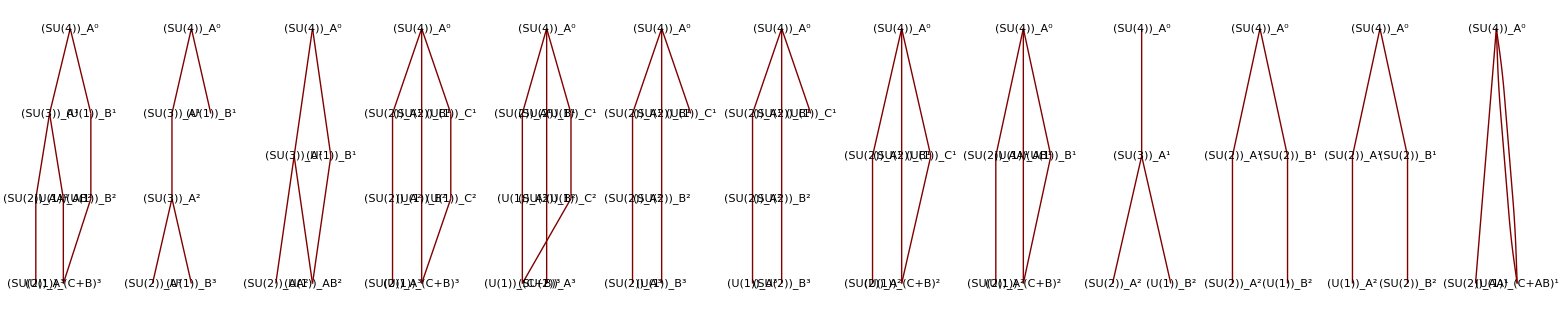

({A3(A)→{{A2(A)→{{A1(AA)→{{A1(A)→{}}}},{U1(AB)→{{U1(C+B)→{}}}}}},{U1(B)→{{U1(B)→{{U1(C+B)→{}}}}}}}}
{A3(A)→{{A2(A)→{{A2(A)→{{A1(A)→{}},{U1(B)→{}}}}}},{U1(B)→{}}}}
{A3(A)→{{A2(A)→{{A1(AA)→{}},{U1(AB)→{}}}},{U1(B)→{{U1(AB)→{}}}}}}
{A3(A)→{{A1(A)→{{A1(A)→{{A1(A)→{}}}}}},{A1(B)→{{U1(B)→{{U1(C+B)→{}}}}}},{U1(C)→{{U1(C)→{{U1(C+B)→{}}}}}}}}
{A3(A)→{{A1(A)→{{U1(A)→{{U1(C+B)→{}}}}}},{A1(B)→{{A1(B)→{{A1(A)→{}}}}}},{U1(C)→{{U1(C)→{{U1(C+B)→{}}}}}}}}
{A3(A)→{{A1(A)→{{A1(A)→{{A1(A)→{}}}}}},{A1(B)→{{A1(B)→{{U1(B)→{}}}}}},{U1(C)→{}}}}
{A3(A)→{{A1(A)→{{A1(A)→{{U1(A)→{}}}}}},{A1(B)→{{A1(B)→{{A1(B)→{}}}}}},{U1(C)→{}}}}
{A3(A)→{{A1(A)→{{A1(A)→{}}}},{A1(B)→{{U1(C+B)→{}}}},{U1(C)→{{U1(C+B)→{}}}}}}
{A3(A)→{{A1(AA)→{{A1(A)→{}}}},{U1(AB)→{{U1(C+B)→{}}}},{U1(B)→{{U1(C+B)→{}}}}}}
{A3(A)→{{A2(A)→{{A1(A)→{}},{U1(B)→{}}}}}}
{A3(A)→{{A1(A)→{{A1(A)→{}}}},{A1(B)→{{U1(B)→{}}}}}}
{A3(A)→{{A1(A)→{{U1(A)→{}}}},{A1(B)→{{A1(B)→{}}}}}}
{A3(A)→{{A1(AA)→{}},{U1(C+AB)→{}},{U1(C+AB)→{}}}})

```mathematica
A3BC = BreakingChains[A3,A1xU1]
```

```mathematica
F1 = NewRep["(1,0,0)A3","Fermion"]
F2 = NewRep["(0,0,1)A3","Fermion"]
F3 = NewRep["(0,1,0)A3","Scalar"]
reps ={F1,F2,F3}
```

4

4*

6

{4,4*,6}

```mathematica
A3theory = NewTheory[A3,A3BC[[3]],{F1,F2,F3}]
```

{Group→A3,Chain→{{A3(A)→{{A2(A)→{{A1(AA)→{}},{U1(AB)→{}}}},{U1(B)→{{U1(AB)→{}}}}}}},Reps→{4,4*,6}}

```mathematica
GenerateModelsFast[A3theory]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

{}

```mathematica
A3model=NewModel[A3theory];
A3model//TableForm
```

CALCULATING LEVEL 4 = A3(A)[]

CALCULATING LEVEL 3 = A2(A)xU1(B)[]

CALCULATING LEVEL 2 = A2(A)[]

CALCULATING LEVEL 1 = A1(A)xU1(B)[]

Group→A3 | Chain→{{A3(A)→{{A2(A)→{{A2(A)→{{A1(A)→{}},{U1(B)→{}}}}}},{U1(B)→{}}}}} | Reps→{4,4*,6}
Group→A2xU1 | Chain→{{A2(A)→{{A2(A)→{{A1(A)→{}},{U1(B)→{}}}}}},{U1(B)→{}}} | Reps→{{3, -0.25},{1, 0.75},{3*, 0.25},{1, -0.75},{3*, -0.50},{3, 0.50}}
Group→A2 | Chain→{{A2(A)→{{A1(A)→{}},{U1(B)→{}}}}} | Reps→{3,1,3*,1,3*,3}
Group→A1xU1 | Chain→{{A1(A)→{}},{U1(B)→{}}} | Reps→{{2, 0.33},{1, -0.67},{1, 0.00},{2, -0.33},{1, 0.67},{1, 0.00},{2, -0.33},{1, 0.67},{2, 0.33},{1, -0.67}}

```mathematica
A3RGEs=getRGEs[gauge][A3model];
A3RGEs//MatrixForm
```

(bSUSY→(-10. | -7. | -7. | -4.
-10. | -7. | -7. | 1.6
-10. | 1.8 | - | -)
bSM→(-4.22222 | -3. | -7.33333 | -4.88889
-4.22222 | -3. | -7.33333 | 0.
-4.22222 | 0.6 | - | -))

```mathematica
gref = √(4π/50);
```

```mathematica
sol=solveRGEs[gauge][RGEs,gref];
```

Part::partw: Part TraditionalForm`1 of TraditionalForm`{} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

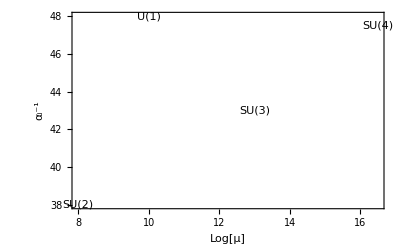

```mathematica
Plot[{4π sol[t][[1]]^-2,4 π sol[t][[2]]^-2},{t,3,18},
PlotStyle->Thick,
Frame->True,
FrameLabel->{"Log[μ]","α_i^-1"},
Epilog->{Text["SU(4)",{16.5,47.5}],
		Text["SU(3)",{13,43}],
		Text["SU(2)",{8,38}],
		Text["U(1)",{10,48}]}]
```

## SU(5) -> SM model

```mathematica
A4=NewGroup["A4"]
```

A4

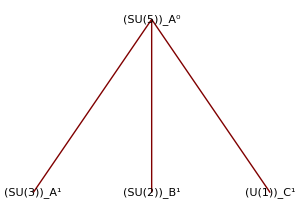

```mathematica
A4BC=BreakingChains[A4,SM];
```

```mathematica
TenF = NewRep["(0,1,0,0)A4","Fermion"]
FiveBarF = NewRep["(0,0,0,1)A4","Fermion"]
FiveH = NewRep["(1,0,0,0)A4","Scalar"]
FiveBarH=NewRep["(0,0,0,1)A4","Scalar"]
TwentyFourH=NewRep[24,A4,"Scalar"]
Singlet=NewRep[1,A4,"Scalar"]
```

10

5*

5

5*'

24

1

```mathematica
A4Reps={TenF,TenF,TenF,FiveBarF,FiveBarF,FiveBarF,FiveH,FiveBarH,TwentyFourH,Singlet}
```

{10,10,10,5*,5*,5*,5,5*',24,1}

```mathematica
A4theory=NewTheory[A4,A4BC[[1]],A4Reps]
```

{Group→A4,Chain→{{A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}}},Reps→{10,10,10,5*,5*,5*,5,5*',24,1}}

```mathematica
A4models = GenerateModelsFast[A4theory,PrintOut->False];
A4models//TableForm
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

Group→A4
Chain→{{A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}}}
Reps→{10,10,10,5*,5*,5*,5,5*',24,1}
AnomalyFree→True | Group→A2xA1xU1
Chain→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}
Reps→{{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3*, 1, 0.258},{1, 2, -0.387},{3*, 1, 0.258},{1, 2, -0.387},{3*, 1, 0.258},{1, 2, -0.387},{1, 2, 0.387}}
AnomalyFree→False
Group→A4
Chain→{{A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}}}
Reps→{10,10,10,5*,5*,5*,5,5*',24,1}
AnomalyFree→True | Group→A2xA1xU1
Chain→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}
Reps→{{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3*, 1, 0.258},{1, 2, -0.387},{3*, 1, 0.258},{1, 2, -0.387},{3*, 1, 0.258},{1, 2, -0.387},{1, 2, 0.387},{1, 2, -0.387}'}
AnomalyFree→True
Group→A4
Chain→{{A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}}}
Reps→{10,10,10,5*,5*,5*,5,5*',24,1}
AnomalyFree→True | Group→A2xA1xU1
Chain→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}
Reps→{{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3*, 1, 0.258},{1, 2, -0.387},{3*, 1, 0.258},{1, 2, -0.387},{3*, 1, 0.258},{1, 2, -0.387},{1, 2, 0.387},{1, 1, 0.000}}
AnomalyFree→False
Group→A4
Chain→{{A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}}}
Reps→{10,10,10,5*,5*,5*,5,5*',24,1}
AnomalyFree→True | Group→A2xA1xU1
Chain→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}
Reps→{{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3, 2, 0.129},{3*, 1, -0.516},{1, 1, 0.775},{3*, 1, 0.258},{1, 2, -0.387},{3*, 1, 0.258},{1, 2, -0.387},{3*, 1, 0.258},{1, 2, -0.387},{1, 2, 0.387},{1, 2, -0.387}',{1, 1, 0.000}}
AnomalyFree→True

## SU(5)xU(1) -> SM model

```mathematica
A4U1=NewGroup["A4xU1"];
A4U1//TableForm
```

A4xU1

```mathematica
SM//TableForm
```

A2xA1xU1

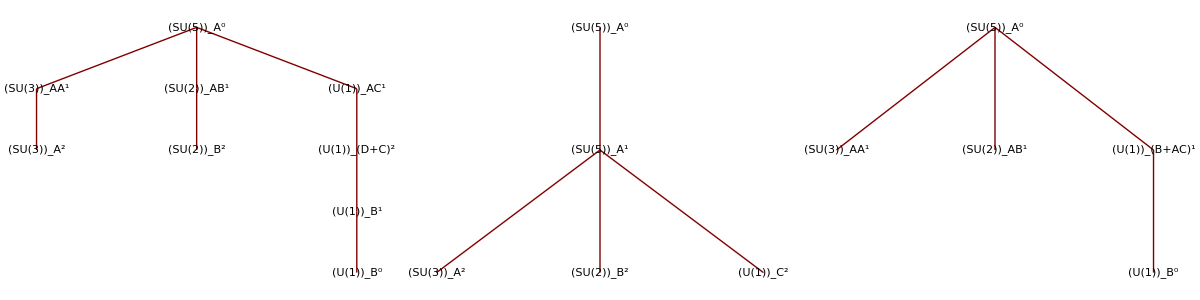

```mathematica
A4U1BC=BreakingChains[A4U1,SM];
```

```mathematica
Ten2F = NewRep["(0,1,0,0,-1)A4xU1","Fermion"]
FiveBar3F = NewRep["(0,0,0,1,3)A4xU1","Fermion"]
One5F=NewRep["(0,0,0,0,-5)A4xU1","Fermion"]
Five1H = NewRep["(1,0,0,0,-3)A4xU1","Scalar"]
FiveBar1H=NewRep["(0,0,0,1,3)A4xU1","Scalar"]
TenFlippedH=NewRep["(0,1,0,0,-1)A4xU1","Scalar"]
```

{10, -1.000}'

{5*, 3.000}

{1, -5.000}

{5, -3.000}

{5*, 3.000}'

{10, -1.000}

```mathematica
A4U1Reps={Ten2F,Ten2F,Ten2F,FiveBar3F,FiveBar3F,FiveBar3F,One5F,One5F,One5F,Five1H,FiveBar1H,TenFlippedH}
```

{{10, -1.000}',{10, -1.000}',{10, -1.000}',{5*, 3.000},{5*, 3.000},{5*, 3.000},{1, -5.000},{1, -5.000},{1, -5.000},{5, -3.000},{5*, 3.000}',{10, -1.000}}

```mathematica
A4U1theory=NewTheory[A4U1,A4U1BC[[3]],A4U1Reps]
```

{Group→A4xU1,Chain→{{A4(A)→{{A2(AA)→{}},{A1(AB)→{}},{U1(B+AC)→{}}}},{U1(B)→{{U1(B+AC)→{}}}}},Reps→{{10, -1.000}',{10, -1.000}',{10, -1.000}',{5*, 3.000},{5*, 3.000},{5*, 3.000},{1, -5.000},{1, -5.000},{1, -5.000},{5, -3.000},{5*, 3.000}',{10, -1.000}}}

```mathematica
A4U1model = GenerateModels[A4U1theory,PrintOut->False];
A4U1model//TableForm
```

Group→A4xU1
Chain→{{A4(A)→{{A2(AA)→{}},{A1(AB)→{}},{U1(B+AC)→{}}}},{U1(B)→{{U1(B+AC)→{}}}}}
Reps→{{10, 0.156},{10, 0.156},{10, 0.156},{5*, -0.469},{5*, -0.469},{5*, -0.469},{1, 0.781},{1, 0.781},{1, 0.781},{5, 0.469},{5*, -0.469}',{10, 0.156}'}
Norm→-0.156227
Mixing→{0.991632,-0.129099}
AnomalyFree→False | Group→A2xA1xU1
Chain→{{A2(AA)→{}},{A1(AB)→{}},{U1(B+AC)→{}},{U1(B+AC)→{}}}
Reps→{{3, 2, 0.129},{3*, 1, 0.258},{1, 1, 0.000}',{3, 2, 0.129},{3*, 1, 0.258},{1, 1, 0.000}',{3, 2, 0.129},{3*, 1, 0.258},{1, 1, 0.000}',{3*, 1, -0.516},{1, 2, -0.387},{3*, 1, -0.516},{1, 2, -0.387},{3*, 1, -0.516},{1, 2, -0.387},{1, 1, 0.775},{1, 1, 0.775},{1, 1, 0.775},{1, 2, 0.387}}
Norm→-0.154919
AnomalyFree→False
Group→A4xU1
Chain→{{A4(A)→{{A2(AA)→{}},{A1(AB)→{}},{U1(B+AC)→{}}}},{U1(B)→{{U1(B+AC)→{}}}}}
Reps→{{10, 0.156},{10, 0.156},{10, 0.156},{5*, -0.469},{5*, -0.469},{5*, -0.469},{1, 0.781},{1, 0.781},{1, 0.781},{5, 0.469},{5*, -0.469}',{10, 0.156}'}
Norm→-0.156227
Mixing→{0.991632,-0.129099}
AnomalyFree→False | Group→A2xA1xU1
Chain→{{A2(AA)→{}},{A1(AB)→{}},{U1(B+AC)→{}},{U1(B+AC)→{}}}
Reps→{{3, 2, 0.129},{3*, 1, 0.258},{1, 1, 0.000}',{3, 2, 0.129},{3*, 1, 0.258},{1, 1, 0.000}',{3, 2, 0.129},{3*, 1, 0.258},{1, 1, 0.000}',{3*, 1, -0.516},{1, 2, -0.387},{3*, 1, -0.516},{1, 2, -0.387},{3*, 1, -0.516},{1, 2, -0.387},{1, 1, 0.775},{1, 1, 0.775},{1, 1, 0.775},{1, 2, 0.387},{1, 2, -0.387}'}
Norm→-0.154919
AnomalyFree→True

```mathematica
A4U1RGEs=getRGEs[gauge][A4U1model];
A4U1RGEs//TableForm
```

bSUSY→(-6.5 | -3.
-6.5 | 0.5
-6.5 | 6.3
8.298 | -) | bSM→(-13.5 | -7.
-13.5 | -3.167
-13.5 | 4.1
4.719 | -) | Mixing→(0 | 0
0 | 0
-0.129 | 0
0.992 | 0)
bSUSY→(-6.5 | -3.
-6.5 | 1.
-6.5 | 6.6
8.298 | -) | bSM→(-13.5 | -7.
-13.5 | -3.
-13.5 | 4.2
4.719 | -) | Mixing→(0 | 0
0 | 0
-0.129 | 0
0.992 | 0)

```mathematica
gref=√(4π/50)
```

(√(2 π))/5

```mathematica
(*sol=solveRGEs[gauge][RGEs,{{10^16,gref}}];*)
```

```mathematica
(*Plot[{4π sol[t][[1]]^-2,4π sol[t][[2]]^-2,4π sol[t][[3]]^-2},{t,3,18},
PlotStyle->Thick,
Frame->True,
FrameLabel->{"Log[μ]","α_i^-1"},
Epilog->{Text["SU(5)",{17,49}],
		Text["SU(4)",{12,44}],
		Text["SU(3)",{5,40}],
		Text["U(1)_1",{10,54}],
		Text["U(1)_2",{7,44}]}]*)
```

## SO(10) -> PS model

```mathematica
D5=NewGroup["D5"];
D5//TableForm
```

$Aborted

D5

```mathematica
SM=NewGroup["A2xA1xU1"];
SM//TableForm
```

A2xA1xU1

```mathematica
D5BC=BreakingChains[D5,SM];
```

```mathematica
Length[D5BC]
```

38

```mathematica
SixteenF = NewRep["(0,0,0,1,0)D5","Fermion"]
TenH = NewRep["(1,0,0,0,0)D5","Scalar"]
```

16

10

```mathematica
D5Reps={SixteenF,SixteenF,SixteenF,TenH}
```

{16,16,16,10}

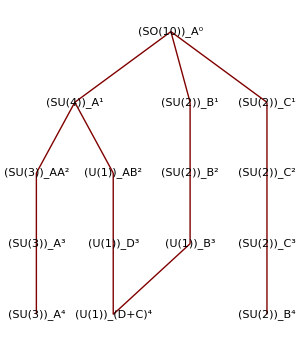

```mathematica
TreePlot[MakeTree@D5BC[[11]],Automatic,ImageSize->300,VertexLabeling->True]
```

```mathematica
D5Theory=NewTheory[D5,D5BC[[11]],D5Reps]
```

{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{{A2(A)→{{A2(A)→{}}}}}},{U1(AB)→{{U1(D)→{{U1(D+C)→{}}}}}}}},{A1(B)→{{A1(B)→{{U1(B)→{{U1(D+C)→{}}}}}}}},{A1(C)→{{A1(C)→{{A1(C)→{{A1(B)→{}}}}}}}}}}},Reps→{16,16,16,10}}

```mathematica
D5models=GenerateModels[D5Theory];
D5models//TableForm
```

{}

```mathematica
D5RGEs=getRGEs[gauge][D5model]
```

{bSUSY→(-17 | -5 | -2. | -2. | -2.
-17 | -5 | 6.3 | 6.3 | 6.3
-17 | 1 | 1. | 1. | 1.
-17 | 1 | 1. | 4.2 | -),bSM→(-25 | -31/3 | -6.66667 | -6.66667 | -6.66667
-25 | -31/3 | 3.9 | 3.9 | 3.9
-25 | -3 | -3. | -3. | -3.
-25 | -3 | -3. | 2.6 | -)}

```mathematica
gref=√(4π/50)
```

(√(2 π))/5

```mathematica
sol=solveRGEs[gauge][D5RGEs,{{10^16,gref}}];
```

```mathematica
4π sol[2][[1]]^-2
```

(4 π)/Null^2

```mathematica
sol[2]
```

{Null,Null,Null}

Power::infy: Infinite expression TraditionalForm`1/0^2 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

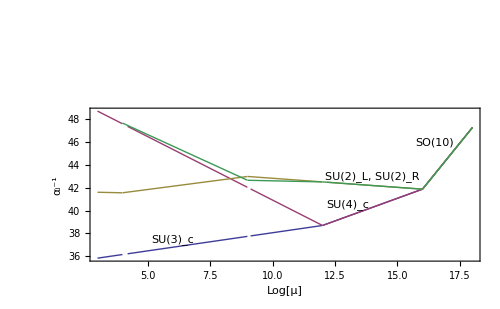

```mathematica
Plot[{4π sol[t][[1]]^-2,4π sol[t][[2]]^-2,4π sol[t][[3]]^-2},{t,3,18},
PlotStyle->Thick,
Frame->True,
FrameLabel->{"Log[μ]","α_i^-1"},
Epilog->{Text["SO(10)",{16.5,46}],
		Text["SU(4)_c",{13,40.5}],
		Text["SU(2)_L, SU(2)_R",{14,43}],
		Text["SU(3)_c",{6,37.5}],
		Text["SU(2)_L",{7,55}],
		Text["U(1)_R",{5,55}]},
ImageSize->500]
```

## SO(10) -> SU(5)xU(1) ->SM model

```mathematica
D5=NewGroup["D5"];
D5//TableForm
```

D5

```mathematica
SM=NewGroup["A2xA1xU1"];
SM//TableForm
```

A2xA1xU1

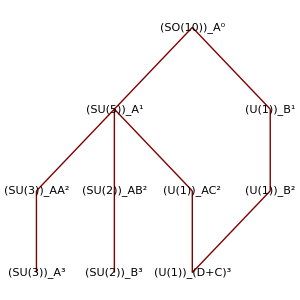
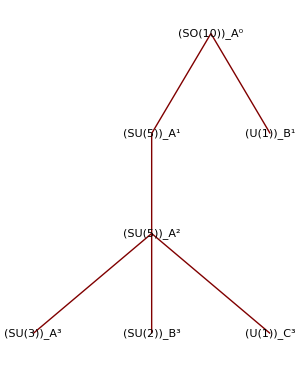
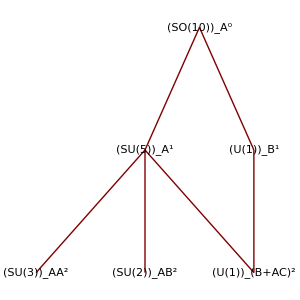
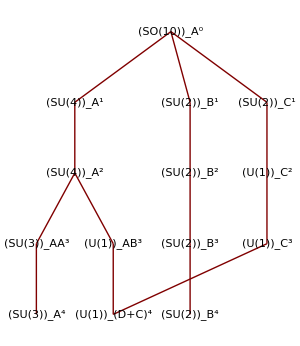
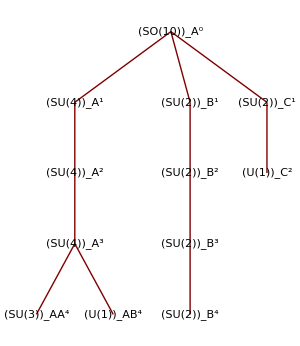
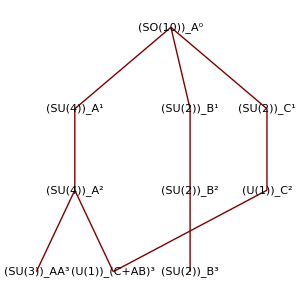
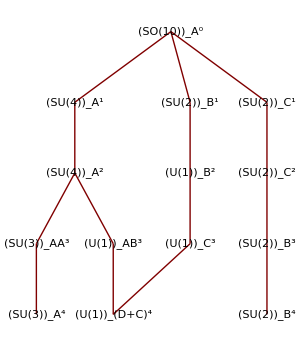
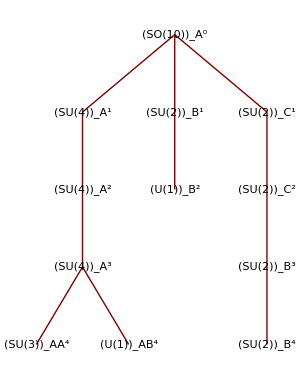
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
D5BC=BreakingChains[D5,SM];
```

```mathematica
SixteenF = NewRep["(0,0,0,1,0)D5","Fermion"]
SixteenH = NewRep["(0,0,0,1,0)D5","Scalar"]
SixteenHbar = NewRep["(0,0,0,0,1)D5","Scalar"]
FourtyFiveH=NewRep[45,D5,"Scalar"]
```

16

16'

16*

45

```mathematica
D5Reps2={SixteenF,SixteenF,SixteenF,SixteenH,SixteenHbar,FourtyFiveH}
```

{16,16,16,16',16*,45}

```mathematica
PrintTree[D5BC[[3]]]
```

-Graphics-

```mathematica
D5Theory2=NewTheory[D5,D5BC[[3]],D5Reps2]
```

{Group→D5,Chain→{{D5(A)→{{A4(A)→{{A2(AA)→{}},{A1(AB)→{}},{U1(B+AC)→{}}}},{U1(B)→{{U1(B+AC)→{}}}}}}},Reps→{16,16,16,16',16*,45}}

```mathematica
D5models2=GenerateModels[D5Theory2,PrintOut->False];
D5models2//TableForm
```

Generating Models for Step 3 |  |  | 
Elapsed Time |  |  | 
Progress |  |  | Cancel
Successful Models |  |  |

Generating Models for Step 2 |  |  | 
Elapsed Time |  |  | 
Progress |  |  | Cancel
Successful Models |  |  |

Generating Models for Step 2 |  |  | 
Elapsed Time |  |  | 
Progress |  |  | Cancel
Successful Models |  |  |

Generating Models for Step 2 |  |  | 
Elapsed Time |  |  | 
Progress |  |  | Cancel
Successful Models |  |  |

«7 more identical outputs»

1
 |  |  |  |

```mathematica
D5RGEs2=getRGEs[gauge][D5models2];
D5RGEs2//TableForm
```

bSUSY→(-6 | -5. | -3.
-6 | -5. | 1.
-6 | -5. | 6.59948
-6 | 8.40202 | -) | bSM→(-21.3333 | -13. | -7.
-21.3333 | -13. | -3.16667
-21.3333 | -13. | 4.09967
-21.3333 | 4.72114 | -) | Mixing→(0 | 0 | 0
0 | 0 | 0
0 | 1 | 0
0 | -0.129115 | 0)
bSUSY→(-6 | -5. | -3.
-6 | -5. | 1.
-6 | -5. | 6.59948
-6 | 9.60232 | -) | bSM→(-21.3333 | -13. | -7.
-21.3333 | -13. | -3.16667
-21.3333 | -13. | 4.09967
-21.3333 | 5.12123 | -) | Mixing→(0 | 0 | 0
0 | 0 | 0
0 | 1 | 0
0 | -0.129115 | 0)

## SO(10) -> SU(5) -> SM model

```mathematica
D5=NewGroup["D5"];
D5//TableForm
```

D5

```mathematica
SM=NewGroup["A2xA1xU1"];
SM//TableForm
```

A2xA1xU1

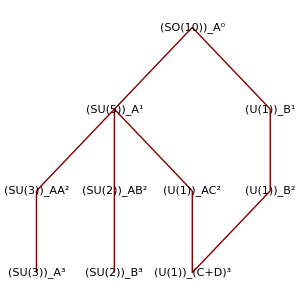
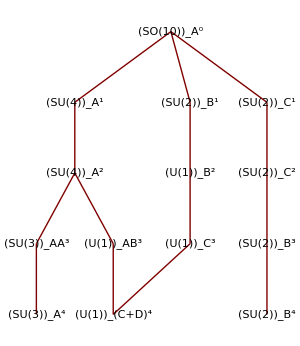
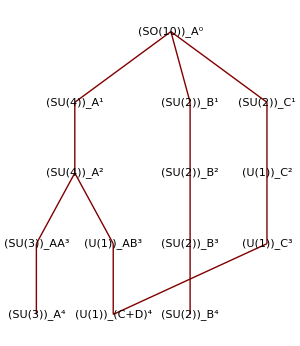
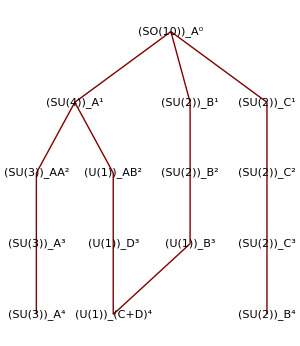
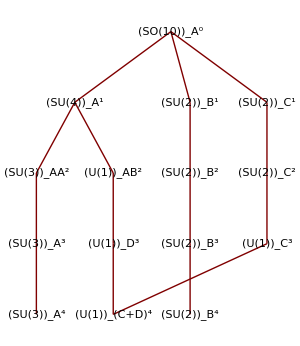
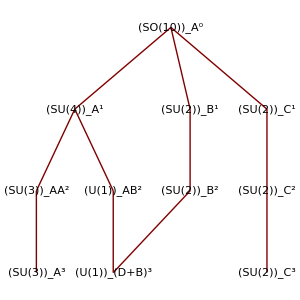
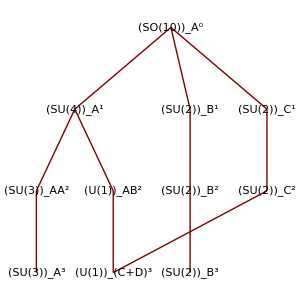
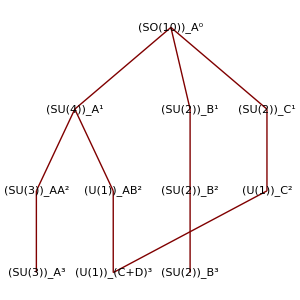
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
D5BC=BreakingChains[D5,SM];
```

```mathematica
SixteenF = NewRep["(0,0,0,1,0)D5","Fermion"]
SixteenH = NewRep["(0,0,0,1,0)D5","Scalar"]
SixteenHbar = NewRep["(0,0,0,0,1)D5","Scalar"]
TenH=NewRep["(1,0,0,0,0)D5","Scalar"]
FourtyFiveH=NewRep[45,D5,"Scalar"]
```

16

16'

16*

10

45

```mathematica
D5Reps3={SixteenF,SixteenF,SixteenF,SixteenH,TenH,FourtyFiveH}
```

{16,16,16,16',10,45}

```mathematica
PrintTree@MakeTree[D5BC[[34]]]
```

-Graphics-

```mathematica
D5Theory3=NewTheory[D5,D5BC[[34]],D5Reps3]
```

{Group→D5,Chain→{{D5(A)→{{A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}}}}},Reps→{16,16,16,16',10,45}}

```mathematica
Clear[ModelData,RGEData]
```

```mathematica
D5models3=GenerateModelsFast[D5Theory3, PrintFile->True];
D5models3//TableForm
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

## SO(10)->SU(3)xSU(2)xSU(2)xU(1)->SM model

```mathematica
D5=NewGroup["D5"];
D5//TableForm
```

D5

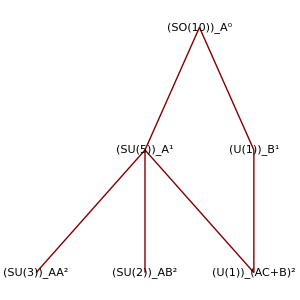
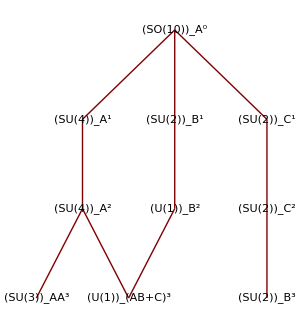
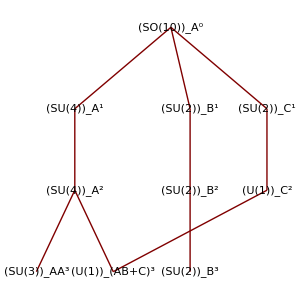
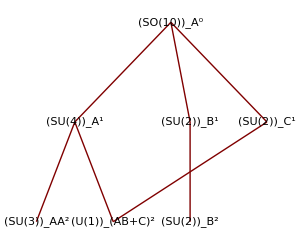
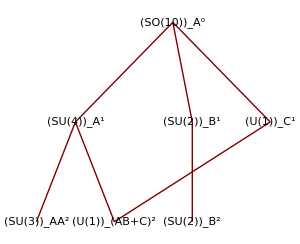
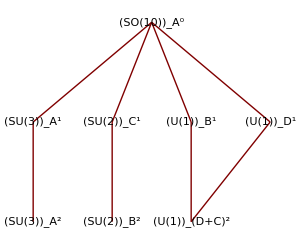
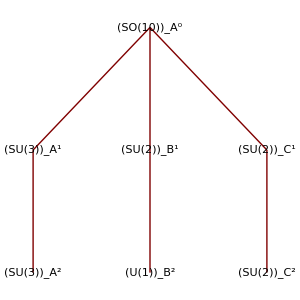
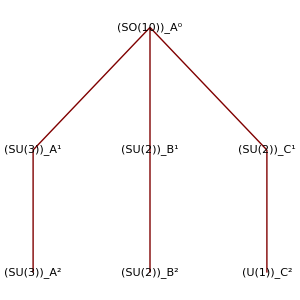
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
D5BC=BreakingChains[D5,SM];
```

```mathematica
SixteenF = NewRep["(0,0,0,1,0)D5","Fermion"]
TenH=NewRep[10,D5,"Scalar"]
FourtyFiveH=NewRep[45,D5,"Scalar"]
OneTwoSix=NewRep[126,D5,"Scalar"]
OneTwoSixB=NewRep["(0,0,0,0,2)D5","Scalar"]
```

16

10

45

126

126*

```mathematica
D5Reps4={SixteenF,SixteenF,SixteenF,TenH,FourtyFiveH,FourtyFiveH,OneTwoSix,OneTwoSixB}
```

{16,16,16,10,45,45,126,126*}

```mathematica
PrintTree@MakeTree[D5BC[[32]]]
```

-Graphics-

```mathematica
D5Theory4=NewTheory[D5,D5BC[[32]],D5Reps4]
```

{Group→D5,Chain→{{D5(A)→{{A2(A)→{{A2(A)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(D+C)→{}}}},{U1(D)→{{U1(D+C)→{}}}}}}},Reps→{16,16,16,10,45,45,126,126*}}

```mathematica
D5Models4=Table[{},{5}];
```

```mathematica
Clear[RGEData,ModData]
```

```mathematica
D5Models4[[2]]=GenerateModelsFast[D5Theory4,NReps->2,PrintOut->False]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

DBData[{1, 1, 3, -3.000},A2(A)xA1(B)[A2xA1xA1xU1]] = {{1, 1},{1, 1},{1, 1}}

DBData[{1, 1, 3, -3.000},A2(A)xA1(B)xU1(D)[A2xA1xA1xU1]] = {{1, 1, -3.000},{1, 1, -3.000},{1, 1, -3.000}}

DBData[{1, 1, 3, -3.000},A2(A)xA1(B)xU1(C)[A2xA1xA1xU1]] = {{1, 1, 1.000}',{1, 1, 0.000},{1, 1, -1.000}}

DBData[{1, 1, 3, -3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 1, 0.000},{1, 1, -3.000},{1, 1, -6.000}}

DBData[{3*, 1, 2, 0.500},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3*, 1, 2.000},{3*, 1, -1.000}}

DBData[{3, 2, 1, -0.500},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3, 2, -0.500}}

DBData[{1, 2, 1, 1.500},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 2, 1.500}}

DBData[{1, 1, 2, -1.500},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 1, 0.000}',{1, 1, -3.000}'}

DBData[{1, 1, 3, 3.000},A2(A)xA1(B)[A2xA1xA1xU1]] = {{1, 1},{1, 1},{1, 1}}

DBData[{1, 1, 3, 3.000},A2(A)xA1(B)xU1(D)[A2xA1xA1xU1]] = {{1, 1, 3.000},{1, 1, 3.000},{1, 1, 3.000}}

DBData[{1, 1, 3, 3.000},A2(A)xA1(B)xU1(C)[A2xA1xA1xU1]] = {{1, 1, 1.000}',{1, 1, 0.000},{1, 1, -1.000}}

DBData[{1, 1, 3, 3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 1, 0.000},{1, 1, 3.000},{1, 1, 6.000}}

DBData[{3*, 1, 2, 0.500},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3*, 1, -1.000},{3*, 1, 2.000}}

DBData[{3, 2, 1, -0.500},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3, 2, -0.500}}

DBData[{1, 2, 1, 1.500},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 2, 1.500}}

DBData[{1, 1, 2, -1.500},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 1, -3.000}',{1, 1, 0.000}'}

DBData[{1, 2, 2, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 2, 1.500}',{1, 2, -1.500}}

DBData[{1, 2, 2, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 2, -1.500},{1, 2, 1.500}'}

DBData[{3, 1, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3, 1, 1.000}}

DBData[{3, 1, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3, 1, 1.000}}

DBData[{3*, 1, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3*, 1, -1.000}'}

DBData[{3*, 1, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3*, 1, -1.000}'}

DBData[{3, 2, 2, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3, 2, 2.500},{3, 2, -0.500}'}

DBData[{3, 2, 2, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3, 2, -0.500}',{3, 2, 2.500}}

DBData[{3*, 2, 2, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3*, 2, 0.500},{3*, 2, -2.500}}

DBData[{3*, 2, 2, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3*, 2, -2.500},{3*, 2, 0.500}}

DBData[{8, 1, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{8, 1, 0.000}}

DBData[{8, 1, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{8, 1, 0.000}}

DBData[{3*, 1, 1, 2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3*, 1, 2.000}'}

DBData[{3*, 1, 1, 2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3*, 1, 2.000}'}

DBData[{1, 1, 3, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 1, 3.000},{1, 1, 0.000},{1, 1, -3.000}}

DBData[{1, 1, 3, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 1, -3.000},{1, 1, 0.000},{1, 1, 3.000}}

DBData[{1, 3, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 3, 0.000}}

DBData[{1, 3, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 3, 0.000}}

DBData[{3, 1, 1, -2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3, 1, -2.000}}

DBData[{3, 1, 1, -2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3, 1, -2.000}}

DBData[{1, 1, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 1, 0.000}}

DBData[{1, 1, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 1, 0.000}}

DBData[{8, 2, 2, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{8, 2, 1.500},{8, 2, -1.500}}

DBData[{8, 2, 2, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{8, 2, -1.500},{8, 2, 1.500}}

DBData[{6*, 1, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{6*, 1, 4.000},{6*, 1, 1.000},{6*, 1, -2.000}}

DBData[{6*, 1, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{6*, 1, -2.000},{6*, 1, 1.000},{6*, 1, 4.000}}

DBData[{6, 3, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{6, 3, -1.000}}

DBData[{6, 3, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{6, 3, -1.000}}

DBData[{3*, 2, 2, 2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3*, 2, 3.500},{3*, 2, 0.500}}

DBData[{3*, 2, 2, 2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3*, 2, 0.500},{3*, 2, 3.500}}

DBData[{3, 2, 2, -2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3, 2, -0.500}',{3, 2, -3.500}}

DBData[{3, 2, 2, -2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3, 2, -3.500},{3, 2, -0.500}'}

DBData[{3, 3, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3, 3, 1.000}}

DBData[{3, 3, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3, 3, 1.000}}

DBData[{3*, 1, 3, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3*, 1, 2.000}',{3*, 1, -1.000}',{3*, 1, -4.000}}

DBData[{3*, 1, 3, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3*, 1, -4.000},{3*, 1, -1.000}',{3*, 1, 2.000}'}

DBData[{1, 3, 1, 3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 3, 3.000}}

DBData[{1, 3, 1, 3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 3, 3.000}}

DBData[{6*, 3, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{6*, 3, 1.000}}

DBData[{6, 1, 3, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{6, 1, 2.000},{6, 1, -1.000},{6, 1, -4.000}}

DBData[{3, 1, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3, 1, 4.000},{3, 1, 1.000},{3, 1, -2.000}}

DBData[{3*, 3, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{3*, 3, -1.000}}

DBData[{1, 1, 3, 3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 1, 6.000},{1, 1, 3.000},{1, 1, 0.000}}

DBData[{1, 3, 1, -3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,3}] = {{1, 3, -3.000}}

DBData[{6*, 3, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{6*, 3, 1.000}}

DBData[{6, 1, 3, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{6, 1, -4.000},{6, 1, -1.000},{6, 1, 2.000}}

DBData[{3, 1, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3, 1, -2.000},{3, 1, 1.000},{3, 1, 4.000}}

DBData[{3*, 3, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{3*, 3, -1.000}}

DBData[{1, 3, 1, -3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{1,-3}] = {{1, 3, -3.000}}

DBData[{1, 2, 2, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 2, -0.387}',{1, 2, 0.387}}

DBData[{3, 1, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3, 1, 0.632}}

DBData[{3*, 1, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3*, 1, -0.632}}

DBData[{3, 2, 2, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3, 2, 0.245},{3, 2, 1.020}}

DBData[{3*, 2, 2, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3*, 2, -1.020},{3*, 2, -0.245}}

DBData[{8, 1, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{8, 1, 0.000}}

DBData[{3*, 1, 1, 2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3*, 1, 1.265}}

DBData[{1, 1, 3, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 1, -0.775},{1, 1, 0.000},{1, 1, 0.775}'}

DBData[{1, 3, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 3, 0.000}}

DBData[{3, 1, 1, -2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3, 1, -1.265}}

DBData[{1, 1, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 1, 0.000}}

DBData[{8, 2, 2, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{8, 2, -0.387},{8, 2, 0.387}}

DBData[{6*, 1, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{6*, 1, -0.142},{6*, 1, 0.632},{6*, 1, 1.407}}

DBData[{6, 3, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{6, 3, -0.632}}

DBData[{3*, 2, 2, 2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3*, 2, 0.878},{3*, 2, 1.652}}

DBData[{3, 2, 2, -2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3, 2, -1.652},{3, 2, -0.878}}

DBData[{3, 3, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3, 3, 0.632}}

DBData[{3*, 1, 3, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3*, 1, -1.407},{3*, 1, -0.632},{3*, 1, 0.142}}

DBData[{1, 3, 1, 3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 3, 1.897}}

DBData[{1, 1, 3, -3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 1, -2.672},{1, 1, -1.897},{1, 1, -1.123}}

DBData[{6*, 3, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{6*, 3, 0.632}}

DBData[{6, 1, 3, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{6, 1, -1.407},{6, 1, -0.632},{6, 1, 0.142}}

DBData[{3, 1, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3, 1, -0.142},{3, 1, 0.632},{3, 1, 1.407}}

DBData[{3*, 3, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{3*, 3, -0.632}}

DBData[{1, 1, 3, 3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 1, 1.123},{1, 1, 1.897},{1, 1, 2.672}}

DBData[{1, 3, 1, -3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 3, -1.897}}

DBData[{1, 1, 3, 1.225},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{1, 1, -0.000},{1, 1, 0.775}',{1, 1, 1.549}}

DBData[{8, 3, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,-0.774566}] = {{8, 3, -0.142},{8, 3, 0.632},{8, 3, 1.407}}

DBData[{1, 2, 2, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {{1, 2, 0.387},{1, 2, -0.387}'}

DBData[{3, 1, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {{3, 1, 0.632}}

DBData[{3*, 1, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {{3*, 1, -0.632}}

DBData[{3, 2, 2, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {{3, 2, 1.020},{3, 2, 0.245}}

DBData[{3*, 2, 2, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {{3*, 2, -0.245},{3*, 2, -1.020}}

DBData[{8, 1, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {{8, 1, 0.000}}

LinkObject::linkd: Unable to communicate with closed link LinkObject['/home/tomas/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/Code/mathgroup',90,4].

ImportString::string: First argument $Failed is not a string.

Export::badval: The element Data contains invalid values.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed,Whitespace→].

LinkObject::linkn: Argument LinkObject['/home/tomas/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/Code/mathgroup',90,4] in LinkWrite[LinkObject['/home/tomas/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/Code/mathgroup',90,4],CallPacket[1,{Scalar}]] has an invalid LinkObject number; the link may be closed.

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,Exception].

ReplaceAll::reps: {DBData(Scalar)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImportString::string: First argument GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)) is not a string.

General::stop: Further output of ImportString::string will be suppressed during this calculation.

ReplaceAll::reps: {ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {DBData(Scalar)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

LinkObject::linkn: Argument LinkObject['/home/tomas/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/Code/mathgroup',90,4] in LinkWrite[LinkObject['/home/tomas/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/Code/mathgroup',90,4],CallPacket[4,{JSON}]] has an invalid LinkObject number; the link may be closed.

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,Exception].

DBData[{3*, 1, 1, 2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

LinkObject::linkn: Argument LinkObject['/home/tomas/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/Code/mathgroup',90,4] in LinkWrite[LinkObject['/home/tomas/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/Code/mathgroup',90,4],CallPacket[9,{(0,0,0,2,0)A2xA1xA1xU1,A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],[0.632493,0.774566]}]] has an invalid LinkObject number; the link may be closed.

General::stop: Further output of LinkObject::linkn will be suppressed during this calculation.

Export::badval: The element Data contains invalid values.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed,Whitespace→].

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,Exception].

General::stop: Further output of StringCases::strse will be suppressed during this calculation.

DBData[{1, 1, 3, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

Export::badval: The element Data contains invalid values.

General::stop: Further output of Export::badval will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed,Whitespace→].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

DBData[{1, 3, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{3, 1, 1, -2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{1, 1, 1, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{8, 2, 2, 0.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{6*, 1, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{6, 3, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{3*, 2, 2, 2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{3, 2, 2, -2.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{3, 3, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{3*, 1, 3, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{1, 3, 1, 3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{1, 1, 3, -3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{6*, 3, 1, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{6, 1, 3, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{3, 1, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{3*, 3, 1, -1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{1, 1, 3, 3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{1, 3, 1, -3.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

Part::take: Cannot take positions 1 through 2 in HWeight.

Part::partd: Part specification HWeight⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 2 in HWeight.

General::stop: Further output of Part::take will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[$Failed,1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

DBData[{1, 1, 3, -1.225},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

DBData[{8, 3, 3, 1.000},A2(A)xA1(B)xU1(D+C)[A2xA1xA1xU1],{0.632493,0.774566}] = {label/.ImportString[GetRep(StringReplace[$Failed,Whitespace→],id/.DBData(Scalar)),JSON,type→],$Failed}

(1)
 |  |  |  |

```mathematica
D5Models4[[3]]=GenerateModelsFast[D5Theory4,NReps->{3},PrintFile->True]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

{}

```mathematica
D5Models4[[4]]=GenerateModelsFast[D5Theory4,PrintFile->True,NReps->{4}]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

(1)
 |  |  |  |

```mathematica
D5Models4[[5]]=GenerateModelsFast[D5Theory4,NReps->{5},PrintFile->True]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

(1)
 |  |  |  |

```mathematica
Length[D5Models4[[2]]]+Length[D5Models4[[3]]]+Length[D5Models4[[4]]]+Length[D5Models4[[5]]]
```

239114

## SO(10)->SU(4)xSU(2)xSU(2)->SM model

```mathematica
D5=NewGroup["D5"];
D5//TableForm
```

D5

```mathematica
SM=NewGroup["A2xA1xU1"];
SM//TableForm
```

A2xA1xU1

```mathematica
D5BC=BreakingChains[D5,SM];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
SixteenF = NewRep["(0,0,0,1,0)D5","Fermion"]
TenH=NewRep[10,D5,"Scalar"]
FiftyFour=NewRep[54,D5,"Scalar"]
OneTwoSix=NewRep[126,D5,"Scalar"]
OneTwoSixB=NewRep["(0,0,0,0,2)D5","Scalar"]
```

16

10

54

126

126*

```mathematica
D5Reps5={SixteenF,SixteenF,SixteenF,TenH,FiftyFour,FiftyFour,OneTwoSix,OneTwoSixB}
```

{16,16,16,10,54,54,126,126*}

```mathematica
PrintTree@MakeTree[D5BC[[20]]]
```

-Graphics-

```mathematica
D5Theory5=NewTheory[D5,D5BC[[20]],D5Reps5]
```

{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*}}

```mathematica
D5Models5=GenerateModelsFast[D5Theory5,NReps->2]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

({Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{1, 2, 2},{10*, 1, 3}},Mixing→{1,0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{1, 2, 0.387}},AnomalyFree→False}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{1, 2, 2},{10*, 1, 3}},Mixing→{1,0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{1, 2, -0.387}',{1, 2, 0.387}},AnomalyFree→True}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{1, 2, 2},{10, 1, 3}},Mixing→{1,-0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{1, 2, 0.387}},AnomalyFree→False}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{1, 2, 2},{10, 1, 3}},Mixing→{1,-0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{1, 2, 0.387},{1, 2, -0.387}'},AnomalyFree→True}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{15, 2, 2},{10*, 1, 3}},Mixing→{1,0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{1, 2, 0.387}},AnomalyFree→False}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{15, 2, 2},{10*, 1, 3}},Mixing→{1,0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{1, 2, -0.387}',{1, 2, 0.387}},AnomalyFree→True}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{15, 2, 2},{10, 1, 3}},Mixing→{1,-0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{1, 2, 0.387}},AnomalyFree→False}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{15, 2, 2},{10, 1, 3}},Mixing→{1,-0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{3, 2, 0.129},{1, 2, -0.387},{3*, 1, 0.258},{3*, 1, -0.516},{1, 1, 0.775},{1, 1, 0.000}',{1, 2, 0.387},{1, 2, -0.387}'},AnomalyFree→True}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{10*, 1, 3},{15, 2, 2}},Mixing→{1,0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{1, 2, 0.387}},AnomalyFree→False}
{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}}}},Reps→{16,16,16,10,54,54,126,126*},AnomalyFree→True} | {Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}},{A1(B)→{{A1(B)→{}}}},{A1(C)→{{U1(C+AB)→{}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{10*, 1, 3},{15, 2, 2}},Mixing→{1,0.666667},AnomalyFree→True} | {Group→A2xA1xU1,Chain→{{A2(AA)→{}},{U1(C+AB)→{}},{A1(B)→{}},{U1(C+AB)→{}}},Reps→{{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{3, 2, 0.129},{1, 2, -0.387},{3*, 1, -0.516},{3*, 1, 0.258},{1, 1, 0.000}',{1, 1, 0.775},{1, 2, -0.387}',{1, 2, 0.387}},AnomalyFree→True})

```mathematica
D5Models5=GenerateModelsFast[D5Theory5,NReps->{3}]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

(1)
 |  |  |  |

```mathematica
D5Models5=GenerateModelsFast[D5Theory5,NReps->{4}]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

(1)
 |  |  |  |

```mathematica
D5Models5=GenerateModelsFast[D5Theory5,NReps->{5}]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

(1)
 |  |  |  |

## SO(10)->SU(4)xSU(2)xSU(2)->SU(3)xSU(2)xSU(2)xU(1)->SM model

```mathematica
D5=NewGroup["D5"];
D5//TableForm
```

D5

```mathematica
SM=NewGroup["A2xA1xU1"];
SM//TableForm
```

A2xA1xU1

```mathematica
D5BC=BreakingChains[D5,SM];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
SixteenF = NewRep["(0,0,0,1,0)D5","Fermion"]
TenH=NewRep[10,D5,"Scalar"]
SixteenH=NewRep["(0,0,0,1,0)D5","Scalar"]
FourtyFive=NewRep[45,D5,"Scalar"]
FiftyFour=NewRep[54,D5,"Scalar"]
OneTwenty=NewRep[120,D5,"Scalar"]
OneTwoSix=NewRep[126,D5,"Scalar"]
OneTwoSixB=NewRep["(0,0,0,0,2)D5","Scalar"]
```

16

10

16'

45

54

120

126

126*

```mathematica
D5Reps6={SixteenF,SixteenF,SixteenF,TenH,FourtyFive,FiftyFour,OneTwoSix,OneTwoSixB}
```

{16,16,16,10,45,54,126,126*}

```mathematica
PrintTree@MakeTree[D5BC[[14]]]
```

-Graphics-

```mathematica
D5Theory6=NewTheory[D5,D5BC[[14]],D5Reps6]
```

{Group→D5,Chain→{{D5(A)→{{A3(A)→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}}}},{A1(B)→{{A1(B)→{{A1(B)→{}}}}}},{A1(C)→{{A1(C)→{{U1(D+C)→{}}}}}}}}},Reps→{16,16,16,10,45,54,126,126*}}

```mathematica
D5Models6=GenerateModelsFast[D5Theory6,NReps->2]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

{}

```mathematica
D5Models5=GenerateModelsFast[D5Theory6,NReps->{3}]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

(1)
 |  |  |  |

```mathematica
D5Models5=GenerateModelsFast[D5Theory5,NReps->{4}]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

(1)
 |  |  |  |

```mathematica
D5Models5=GenerateModelsFast[D5Theory5,NReps->{5}]
```

|  |  | 
Elapsed Time |  |  | 
ETA for step |  |  | 
Progress |  |  | Abort
Successful Models |  |  |

(1)
 |  |  |  |

## SU(5)xU(1) model for inflation

```mathematica
A4=NewGroup["A4"];
A4//TableForm
```

A4

```mathematica
SM//TableForm
```

A2xA1xU1

```mathematica
A4BC=BreakingChains[A4,SM];
A4BC//MatrixForm
```

{-Graphics-}

((A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}))

```mathematica
Tenϕ = NewRep["(0,1,0,0)A4","Fermion"]
FiveBarϕ = NewRep["(0,0,0,1)A4","Fermion"]
Oneϕ=NewRep["(0,0,0,0)A4","Fermion"]
Oneϕbar=NewRep["(0,0,0,0)A4","Scalar"]
FiveH = NewRep["(1,0,0,0)A4","Scalar"]
FiveBarH=NewRep["(0,0,0,1)A4","Scalar"]
TwentyFourH=NewRep["(1,0,0,1)A4","Scalar"]
```

10

5*

1

1'

5

5*'

24

```mathematica
A4InflReps={Tenϕ,Tenϕ,Tenϕ,FiveBarϕ,FiveBarϕ,FiveBarϕ,Oneϕ,Oneϕ,Oneϕ,Oneϕbar,FiveH,FiveBarH,TwentyFourH}
```

{10,10,10,5*,5*,5*,1,1,1,1',5,5*',24}

```mathematica
A4Infltheory=NewTheory[A4,A4BC[[1]],A4InflReps]
```

{Group→A4,Chain→{{A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}}},Reps→{10,10,10,5*,5*,5*,1,1,1,1',5,5*',24}}

```mathematica
A4Inflmodel = NewModel[A4Infltheory,CheckForSM->False];
A4Inflmodel//TableForm
```

CALCULATING LEVEL 2 = A4(A)[]

{{DynkinIndex→{1,1.5,0.144},Group→A2xA1xU1,dim→6,id→(1,0,1,0.2)A2xA1xU1,HWeight→(1 | 0 | 1 | 0.2),label→{3, 2, 0.20},nirreps→3,Casimir→{1.33333,0.75,0.024},Weights→{},type→Fermion},{DynkinIndex→{0.5,0,1.152},Group→A2xA1xU1,dim→3,id→(0,1,0,-0.8)A2xA1xU1,HWeight→(0 | 1 | 0 | -0.8),label→{3*, 1, -0.80},nirreps→3,Casimir→{1.33333,0,0.384},Weights→{},type→Fermion},{DynkinIndex→{0,0,0.864},Group→A2xA1xU1,dim→1,id→(0,0,0,1.2)A2xA1xU1,HWeight→(0 | 0 | 0 | 1.2),label→{1, 1, 1.20},nirreps→3,Casimir→{0,0,0.864},Weights→{},type→Fermion},{DynkinIndex→{1,1.5,0.144},Group→A2xA1xU1,dim→6,id→(1,0,1,0.2)A2xA1xU1,HWeight→(1 | 0 | 1 | 0.2),label→{3, 2, 0.20},nirreps→3,Casimir→{1.33333,0.75,0.024},Weights→{},type→Fermion},{DynkinIndex→{0.5,0,1.152},Group→A2xA1xU1,dim→3,id→(0,1,0,-0.8)A2xA1xU1,HWeight→(0 | 1 | 0 | -0.8),label→{3*, 1, -0.80},nirreps→3,Casimir→{1.33333,0,0.384},Weights→{},type→Fermion},{DynkinIndex→{0,0,0.864},Group→A2xA1xU1,dim→1,id→(0,0,0,1.2)A2xA1xU1,HWeight→(0 | 0 | 0 | 1.2),label→{1, 1, 1.20},nirreps→3,Casimir→{0,0,0.864},Weights→{},type→Fermion},{DynkinIndex→{1,1.5,0.144},Group→A2xA1xU1,dim→6,id→(1,0,1,0.2)A2xA1xU1,HWeight→(1 | 0 | 1 | 0.2),label→{3, 2, 0.20},nirreps→3,Casimir→{1.33333,0.75,0.024},Weights→{},type→Fermion},{DynkinIndex→{0.5,0,1.152},Group→A2xA1xU1,dim→3,id→(0,1,0,-0.8)A2xA1xU1,HWeight→(0 | 1 | 0 | -0.8),label→{3*, 1, -0.80},nirreps→3,Casimir→{1.33333,0,0.384},Weights→{},type→Fermion},{DynkinIndex→{0,0,0.864},Group→A2xA1xU1,dim→1,id→(0,0,0,1.2)A2xA1xU1,HWeight→(0 | 0 | 0 | 1.2),label→{1, 1, 1.20},nirreps→3,Casimir→{0,0,0.864},Weights→{},type→Fermion},{DynkinIndex→{0,0.5,0.432},Group→A2xA1xU1,dim→2,id→(0,0,1,-0.6)A2xA1xU1,HWeight→(0 | 0 | 1 | -0.6),label→{1, 2, -0.60},nirreps→3,Casimir→{0,0.75,0.216},Weights→{},type→Fermion},{DynkinIndex→{0.5,0,0.288},Group→A2xA1xU1,dim→3,id→(0,1,0,0.4)A2xA1xU1,HWeight→(0 | 1 | 0 | 0.4),label→{3*, 1, 0.40},nirreps→3,Casimir→{1.33333,0,0.096},Weights→{},type→Fermion},{DynkinIndex→{0,0.5,0.432},Group→A2xA1xU1,dim→2,id→(0,0,1,-0.6)A2xA1xU1,HWeight→(0 | 0 | 1 | -0.6),label→{1, 2, -0.60},nirreps→3,Casimir→{0,0.75,0.216},Weights→{},type→Fermion},{DynkinIndex→{0.5,0,0.288},Group→A2xA1xU1,dim→3,id→(0,1,0,0.4)A2xA1xU1,HWeight→(0 | 1 | 0 | 0.4),label→{3*, 1, 0.40},nirreps→3,Casimir→{1.33333,0,0.096},Weights→{},type→Fermion},{DynkinIndex→{0,0.5,0.432},Group→A2xA1xU1,dim→2,id→(0,0,1,-0.6)A2xA1xU1,HWeight→(0 | 0 | 1 | -0.6),label→{1, 2, -0.60},nirreps→3,Casimir→{0,0.75,0.216},Weights→{},type→Fermion},{DynkinIndex→{0.5,0,0.288},Group→A2xA1xU1,dim→3,id→(0,1,0,0.4)A2xA1xU1,HWeight→(0 | 1 | 0 | 0.4),label→{3*, 1, 0.40},nirreps→3,Casimir→{1.33333,0,0.096},Weights→{},type→Fermion},{DynkinIndex→{0,0,0},Group→A2xA1xU1,dim→1,id→(0,0,0,0)A2xA1xU1,HWeight→(0 | 0 | 0 | 0),label→{1, 1, 0.00},nirreps→3,Casimir→{0,0,0},Weights→{},type→Fermion},{DynkinIndex→{0,0,0},Group→A2xA1xU1,dim→1,id→(0,0,0,0)A2xA1xU1,HWeight→(0 | 0 | 0 | 0),label→{1, 1, 0.00},nirreps→3,Casimir→{0,0,0},Weights→{},type→Fermion},{DynkinIndex→{0,0,0},Group→A2xA1xU1,dim→1,id→(0,0,0,0)A2xA1xU1,HWeight→(0 | 0 | 0 | 0),label→{1, 1, 0.00},nirreps→3,Casimir→{0,0,0},Weights→{},type→Fermion},{DynkinIndex→{0,0,0},Group→A2xA1xU1,dim→1,id→(0,0,0,0)A2xA1xU1,HWeight→(0 | 0 | 0 | 0),label→{1, 1, 0.00},nirreps→3,Casimir→{0,0,0},Weights→{},type→Scalar},{DynkinIndex→{0.5,0,0.288},Group→A2xA1xU1,dim→3,id→(1,0,0,-0.4)A2xA1xU1,HWeight→(1 | 0 | 0 | -0.4),label→{3, 1, -0.40},nirreps→3,Casimir→{1.33333,0,0.096},Weights→{},type→Scalar},{DynkinIndex→{0,0.5,0.432},Group→A2xA1xU1,dim→2,id→(0,0,1,0.6)A2xA1xU1,HWeight→(0 | 0 | 1 | 0.6),label→{1, 2, 0.60},nirreps→3,Casimir→{0,0.75,0.216},Weights→{},type→Scalar},{DynkinIndex→{0,0.5,0.432},Group→A2xA1xU1,dim→2,id→(0,0,1,-0.6)A2xA1xU1,HWeight→(0 | 0 | 1 | -0.6),label→{1, 2, -0.60},nirreps→3,Casimir→{0,0.75,0.216},Weights→{},type→Scalar},{DynkinIndex→{0.5,0,0.288},Group→A2xA1xU1,dim→3,id→(0,1,0,0.4)A2xA1xU1,HWeight→(0 | 1 | 0 | 0.4),label→{3*, 1, 0.40},nirreps→3,Casimir→{1.33333,0,0.096},Weights→{},type→Scalar},{DynkinIndex→{1,1.5,3.6},Group→A2xA1xU1,dim→6,id→(1,0,1,-1)A2xA1xU1,HWeight→(1 | 0 | 1 | -1),label→{3, 2, -1.00},nirreps→3,Casimir→{1.33333,0.75,0.6},Weights→{},type→Scalar},{DynkinIndex→{0,2,0},Group→A2xA1xU1,dim→3,id→(0,0,2,0)A2xA1xU1,HWeight→(0 | 0 | 2 | 0),label→{1, 3, 0.00},nirreps→3,Casimir→{0,2,0},Weights→{},type→Scalar},{DynkinIndex→{3,0,0},Group→A2xA1xU1,dim→8,id→(1,1,0,0)A2xA1xU1,HWeight→(1 | 1 | 0 | 0),label→{8, 1, 0.00},nirreps→3,Casimir→{3,0,0},Weights→{},type→Scalar},{DynkinIndex→{1,1.5,3.6},Group→A2xA1xU1,dim→6,id→(0,1,1,1)A2xA1xU1,HWeight→(0 | 1 | 1 | 1),label→{3*, 2, 1.00},nirreps→3,Casimir→{1.33333,0.75,0.6},Weights→{},type→Scalar},{DynkinIndex→{0,0,0},Group→A2xA1xU1,dim→1,id→(0,0,0,0)A2xA1xU1,HWeight→(0 | 0 | 0 | 0),label→{1, 1, 0.00},nirreps→3,Casimir→{0,0,0},Weights→{},type→Scalar}}

CALCULATING LEVEL 1 = A2(A)xA1(B)xU1(C)[]

Group→A4 | Chain→{{A4(A)→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}}}} | Reps→{10,10,10,5*,5*,5*,1,1,1,1',5,5*',24}
Group→A2xA1xU1 | Chain→{{A2(A)→{}},{A1(B)→{}},{U1(C)→{}}} | Reps→{{3, 2, 0.20},{3*, 1, -0.80},{1, 1, 1.20},{3, 2, 0.20},{3*, 1, -0.80},{1, 1, 1.20},{3, 2, 0.20},{3*, 1, -0.80},{1, 1, 1.20},{1, 2, -0.60},{3*, 1, 0.40},{1, 2, -0.60},{3*, 1, 0.40},{1, 2, -0.60},{3*, 1, 0.40},{1, 1, 0.00},{1, 1, 0.00},{1, 1, 0.00},{1, 1, 0.00}',{3, 1, -0.40},{1, 2, 0.60},{1, 2, -0.60}',{3*, 1, 0.40}',{3, 2, -1.00},{1, 3, 0.00},{8, 1, 0.00},{3*, 2, 1.00},{1, 1, 0.00}'}

```mathematica
A4InflModels=GenerateModels[A4Inflmodel]
```

$Aborted

```mathematica
A4InflRGEs=getRGEs[gauge][A4Inflmodel]
```

{bSUSY→(-3. | 3.
-3. | 6.
-3. | 17.28),bSM→(-12.3333 | -5.
-12.3333 | -1.33333
-12.3333 | 8.64)}

```mathematica
gref=√(4π/50)
```

(√(2 π))/5

```mathematica
(*sol=solveRGEs[gauge][RGEs,{{10^16,gref}}];*)
```

```mathematica
(*Plot[{4π sol[t][[1]]^-2,4π sol[t][[2]]^-2,4π sol[t][[3]]^-2},{t,3,18},
PlotStyle->Thick,
Frame->True,
FrameLabel->{"Log[μ]","α_i^-1"},
Epilog->{Text["SU(5)",{17,49}],
		Text["SU(4)",{12,44}],
		Text["SU(3)",{5,40}],
		Text["U(1)_1",{10,54}],
		Text["U(1)_2",{7,44}]}]*)
```

## SU(4)xSU(2)xSU(2)->SU(3)xSU(2)xU(1)xU(1)->SM

```mathematica
PS=NewGroup["A3xA1xA1"]
```

A3xA1xA1

```mathematica
PSBC=BreakingChains[PS,SM]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

({A3(A)→{{A3(A)→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}}}}}} | {A1(B)→{{A1(B)→{{A1(B)→{{A1(B)→{}}}}}}}} | {A1(C)→{{U1(C)→{{U1(C)→{{U1(D+C)→{}}}}}}}}
{A3(A)→{{A3(A)→{{A3(A)→{{A2(AA)→{}},{U1(AB)→{}}}}}}}} | {A1(B)→{{A1(B)→{{A1(B)→{{A1(B)→{}}}}}}}} | {A1(C)→{{U1(C)→{}}}}
{A3(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}}}} | {A1(B)→{{A1(B)→{{A1(B)→{}}}}}} | {A1(C)→{{U1(C)→{{U1(C+AB)→{}}}}}}
{A3(A)→{{A3(A)→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}}}}}} | {A1(B)→{{U1(B)→{{U1(C)→{{U1(D+C)→{}}}}}}}} | {A1(C)→{{A1(C)→{{A1(B)→{{A1(B)→{}}}}}}}}
{A3(A)→{{A3(A)→{{A3(A)→{{A2(AA)→{}},{U1(AB)→{}}}}}}}} | {A1(B)→{{U1(B)→{}}}} | {A1(C)→{{A1(C)→{{A1(B)→{{A1(B)→{}}}}}}}}
{A3(A)→{{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}}}} | {A1(B)→{{U1(B)→{{U1(C+AB)→{}}}}}} | {A1(C)→{{A1(C)→{{A1(B)→{}}}}}}
{A3(A)→{{A2(AA)→{{A2(A)→{{A2(A)→{}}}}}},{U1(AB)→{{U1(D)→{{U1(D+C)→{}}}}}}}} | {A1(B)→{{A1(B)→{{A1(B)→{{A1(B)→{}}}}}}}} | {A1(C)→{{A1(C)→{{U1(C)→{{U1(D+C)→{}}}}}}}}
{A3(A)→{{A2(AA)→{{A2(A)→{{A2(A)→{}}}}}},{U1(AB)→{{U1(D)→{{U1(D+C)→{}}}}}}}} | {A1(B)→{{A1(B)→{{U1(B)→{{U1(D+C)→{}}}}}}}} | {A1(C)→{{A1(C)→{{A1(C)→{{A1(B)→{}}}}}}}}
{A3(A)→{{A2(AA)→{{A2(A)→{{A2(A)→{}}}}}},{U1(AB)→{}}}} | {A1(B)→{{A1(B)→{{A1(B)→{{A1(B)→{}}}}}}}} | {A1(C)→{{A1(C)→{{A1(C)→{{U1(C)→{}}}}}}}}
{A3(A)→{{A2(AA)→{{A2(A)→{{A2(A)→{}}}}}},{U1(AB)→{}}}} | {A1(B)→{{A1(B)→{{A1(B)→{{U1(B)→{}}}}}}}} | {A1(C)→{{A1(C)→{{A1(C)→{{A1(C)→{}}}}}}}}
{A3(A)→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}}}} | {A1(B)→{{A1(B)→{{A1(B)→{}}}}}} | {A1(C)→{{A1(C)→{{U1(D+C)→{}}}}}}
{A3(A)→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}}}} | {A1(B)→{{A1(B)→{{A1(B)→{}}}}}} | {A1(C)→{{U1(C)→{{U1(D+C)→{}}}}}}
{A3(A)→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}}}} | {A1(B)→{{U1(B)→{{U1(D+C)→{}}}}}} | {A1(C)→{{A1(C)→{{A1(B)→{}}}}}}
{A3(A)→{{A3(A)→{{A2(AA)→{}},{U1(AB)→{}}}}}} | {A1(B)→{{A1(B)→{{A1(B)→{}}}}}} | {A1(C)→{}}
{A3(A)→{{A2(AA)→{{A2(A)→{}}}}}} | {A1(B)→{{A1(B)→{{A1(B)→{}}}}}} | {A1(C)→{{A1(C)→{{U1(C)→{}}}}}}
{A3(A)→{{A2(AA)→{{A2(A)→{}}}}}} | {A1(B)→{{A1(B)→{{U1(B)→{}}}}}} | {A1(C)→{{A1(C)→{{A1(C)→{}}}}}}
{A3(A)→{{A2(AA)→{}},{U1(C+AB)→{}}}} | {A1(B)→{{A1(B)→{}}}} | {A1(C)→{{U1(C+AB)→{}}}}
{A3(A)→{{A2(AA)→{}},{U1(AB)→{}}}} | {A1(B)→{{U1(AB)→{}}}} | {A1(C)→{{A1(C)→{}}}})

```mathematica
PrintTree[PSBC[[12]]]
```

-Graphics-

```mathematica
FourPlet=NewRep["(1,0,0,1,0)A3xA1xA1","Fermion"]
FourBarPlet=NewRep["(0,0,1,0,1)A3xA1xA1","Fermion"]
BiDoublet=NewRep[{1,2,2},PS,"Scalar"]
Adjoint=NewRep[{15,1,3},PS,"Scalar"]
```

{4, 2, 1}

{4*, 1, 2}

{1, 2, 2}

{15, 1, 3}

```mathematica
PSReps={FourPlet,FourBarPlet,FourPlet,FourBarPlet,FourPlet,FourBarPlet,BiDoublet,Adjoint}
```

{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{1, 2, 2},{15, 1, 3}}

```mathematica
PSTheory=NewTheory[PS,PSBC[[12]],PSReps]
```

{Group→A3xA1xA1,Chain→{{A3(A)→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}}}},{A1(B)→{{A1(B)→{{A1(B)→{}}}}}},{A1(C)→{{U1(C)→{{U1(D+C)→{}}}}}}},Reps→{{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{4, 2, 1},{4*, 1, 2},{1, 2, 2},{15, 1, 3}}}

```mathematica
PSModels=GenerateModels[PSTheory,PrintOut->True]
```

GENERATING MODELS LEVEL 3: A3xA1xA1

Subgroup = A2(AA)xA1(B)xU1(AB)xU1(C)[A3xA1xA1]

Subchain = {{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}},{A1(B)→{{A1(B)→{}}}},{U1(C)→{{U1(D+C)→{}}}}}

Subreps = ({3, 2, -0.25, 0.00} | {1, 2, 0.75, 0.00} | {3*, 1, 0.25, 0.50} | {3*, 1, 0.25, -0.50} | {1, 1, -0.75, 0.50} | {1, 1, -0.75, -0.50} | {3, 2, -0.25, 0.00} | {1, 2, 0.75, 0.00} | {3*, 1, 0.25, 0.50} | {3*, 1, 0.25, -0.50} | {1, 1, -0.75, 0.50} | {1, 1, -0.75, -0.50} | {3, 2, -0.25, 0.00} | {1, 2, 0.75, 0.00} | {3*, 1, 0.25, 0.50} | {3*, 1, 0.25, -0.50} | {1, 1, -0.75, 0.50} | {1, 1, -0.75, -0.50} | {1, 2, 0.00, 0.50} | {1, 2, 0.00, -0.50})

GENERATING POSSIBLE REPS

Possible Reps = 4

Reps left = 3

i = 1

SubTheory = {Group→A2(AA)xA1(B)xU1(AB)xU1(C)[A3xA1xA1],Chain→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}},{A1(B)→{{A1(B)→{}}}},{U1(C)→{{U1(D+C)→{}}}}},Reps→{{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50}}}

GENERATING MODELS LEVEL 2: A2xA1xU1xU1

Subgroup = A2(A)xA1(B)xU1(D+C)[A2xA1xU1xU1]

Subchain = {{A2(A)→{}},{U1(D+C)→{}},{A1(B)→{}},{U1(D+C)→{}}}

Semisimple Subgroup = A2(A)xA1(B)[A2xA1xU1xU1]

NO BREAKING: MODEL UNSUCESSFUL

MODEL NOT VALID

Reps left = 2

i = 2

SubTheory = {Group→A2(AA)xA1(B)xU1(AB)xU1(C)[A3xA1xA1],Chain→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}},{A1(B)→{{A1(B)→{}}}},{U1(C)→{{U1(D+C)→{}}}}},Reps→{{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{1, 2, 0.00, 0.50}}}

GENERATING MODELS LEVEL 2: A2xA1xU1xU1

CONSTRAINTS NOT SATISFIED: MODEL UNSUCCESSFUL

MODEL NOT VALID

Reps left = 1

i = 3

SubTheory = {Group→A2(AA)xA1(B)xU1(AB)xU1(C)[A3xA1xA1],Chain→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}},{A1(B)→{{A1(B)→{}}}},{U1(C)→{{U1(D+C)→{}}}}},Reps→{{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{1, 2, 0.00, -0.50}}}

GENERATING MODELS LEVEL 2: A2xA1xU1xU1

CONSTRAINTS NOT SATISFIED: MODEL UNSUCCESSFUL

MODEL NOT VALID

Reps left = 0

i = 4

SubTheory = {Group→A2(AA)xA1(B)xU1(AB)xU1(C)[A3xA1xA1],Chain→{{A2(AA)→{{A2(A)→{}}}},{U1(AB)→{{U1(D+C)→{}}}},{A1(B)→{{A1(B)→{}}}},{U1(C)→{{U1(D+C)→{}}}}},Reps→{{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{3, 2, -0.25, 0.00},{1, 2, 0.75, 0.00},{3*, 1, 0.25, 0.50},{3*, 1, 0.25, -0.50},{1, 1, -0.75, 0.50},{1, 1, -0.75, -0.50},{1, 2, 0.00, 0.50},{1, 2, 0.00, -0.50}}}

GENERATING MODELS LEVEL 2: A2xA1xU1xU1

Subgroup = A2(A)xA1(B)xU1(D+C)[A2xA1xU1xU1]

Subchain = {{A2(A)→{}},{U1(D+C)→{}},{A1(B)→{}},{U1(D+C)→{}}}

Semisimple Subgroup = A2(A)xA1(B)[A2xA1xU1xU1]

Subreps = {{1, 2}}

Subreps = {{1, 2}}

NO BREAKING: MODEL UNSUCESSFUL

MODEL NOT VALID

NO SUCCESSFUL MODELS

{}

## End

```mathematica
D5=NewGroup["D5"]
```

D5

```mathematica
Sixteen=NewRep["(0,0,0,1,0)D5"]
```

16

```mathematica
prod=DirectProduct[Sixteen,Sixteen]
```

{126,120,10}

```mathematica
DirectProduct[prod[[1]],Sixteen]
```

{1200,672,144}

```mathematica
DirectProduct[prod[[2]],Sixteen]
```

{1200,560*,144,16*}

```mathematica
DirectProduct[prod[[3]],Sixteen]
```

{144,16*}

```mathematica
D3=NewGroup["D3"]
```

A3

```mathematica
Four=NewRep["(1,0,0)D3"]
Six=NewRep["(0,1,0)D3"]
```

4

6

```mathematica
Attribute[Four][All]
```

{conjugate→0,DynkinIndex→0.5,Group→A3,dim→4,id→(1,0,0)A3,real→False,HWeight→(1 | 0 | 0),label→4,congruency→(1),Casimir→1.875,Weights→{},type→}

```mathematica
DirectProduct[Four,Four]
```

{10',6}

```mathematica
D4=NewGroup["D4"]
```

D4

```mathematica
Eightv=NewRep["(1,0,0,0)D4"]
Eights=NewRep["(0,0,1,0)D4"]
Eightc=NewRep["(0,0,0,1)D4"]
```

8

8

8

```mathematica
WeightDiagram[Eightv]
WeightDiagram[Eights]
WeightDiagram[Eightc]
```

{(0,0,0,1)D4,(0,1,0,-1)D4,(1,-1,1,0)D4,(-1,0,1,0)D4,(1,0,-1,0)D4,(-1,1,-1,0)D4,(0,-1,0,1)D4,(0,0,0,-1)D4}

{(0,0,0,1)D4,(0,1,0,-1)D4,(1,-1,1,0)D4,(-1,0,1,0)D4,(1,0,-1,0)D4,(-1,1,-1,0)D4,(0,-1,0,1)D4,(0,0,0,-1)D4}

{(0,0,0,1)D4,(0,1,0,-1)D4,(1,-1,1,0)D4,(-1,0,1,0)D4,(1,0,-1,0)D4,(-1,1,-1,0)D4,(0,-1,0,1)D4,(0,0,0,-1)D4}

```mathematica
B4=NewGroup["B4"]
```

B4

```mathematica
NewRep["(1,0,0,0)B4"]
NewRep["(0,1,0,0)B4"]
NewRep["(0,0,1,0)B4"]
NewRep["(0,0,0,1)B4"]
```

9

36

84

16'

```mathematica
NewRep["(0,1,0,0,0)D5"]
```

45

```mathematica
A3=NewGroup["A3"]
```

A3

```mathematica
Four=NewRep["(1,0,0)A3","Scalar"]
Six=NewRep["(0,1,0)A3","Scalar"]
Ten=NewRep["(2,0,0)A3","Scalar"]
```

4

6'

10'

```mathematica
TwoTen=NewRep["(0,0,0,1,1)D5","Scalar"]
```

210

```mathematica
DBData[TwoTen]
```

{conjugate→0,DynkinIndex→56,Group→D5,dim→210,id→(0,0,0,1,1)D5,real→True,HWeight→(0 | 0 | 0 | 1 | 1),label→210,congruency→(0 | 0),Casimir→12,Weights→{},type→Scalar}

```mathematica
DecomposeReps[TwoTen,"A4(A)xU1(B)[D5]"]
DecomposeReps[TwoTen,"A3(A)xA1(B)xA1(C)[D5]"]
DecomposeReps[TwoTen,"A2(AA)xA1(B)xA1(C)xU1(AB)[D5]"]
```

{{75, 0.000},{40, -1.000},{40*, 1.000},{24, 0.000},{10*, -1.000},{10, 1.000},{5, -2.000},{5*, 2.000},{1, 0.000}}

{{15, 3, 1},{15, 1, 3},{10*, 2, 2},{10, 2, 2},{6, 2, 2},{15, 1, 1},{1, 1, 1}}

{{8, 3, 1, 0.000},{6*, 2, 2, 0.500},{6, 2, 2, -0.500},{8, 1, 3, 0.000},{3, 2, 2, 0.500},{3, 2, 2, 0.500},{3*, 2, 2, -0.500},{3*, 2, 2, -0.500},{3*, 3, 1, 1.000},{3, 3, 1, -1.000},{3*, 1, 3, 1.000},{3, 1, 3, -1.000},{8, 1, 1, 0.000},{1, 2, 2, 1.500},{1, 2, 2, -1.500},{3*, 1, 1, 1.000},{1, 3, 1, 0.000},{3, 1, 1, -1.000},{1, 1, 3, 0.000},{1, 1, 1, 0.000},{1, 1, 1, 0.000}}

```mathematica
FiftyFour=NewRep[54,D5]
```

54'

```mathematica
DecomposeReps[OneTwoSix,"A3(A)xA1(B)xA1(C)[D5]"]
```

{{15, 2, 2},{10, 3, 1},{10*, 1, 3},{6, 1, 1}}

```mathematica
DBData[TenH]
```

{conjugate→0,DynkinIndex→1,Group→D5,dim→10,id→(1,0,0,0,0)D5,real→True,HWeight→(1 | 0 | 0 | 0 | 0),label→10,congruency→(0 | 2),Casimir→4.5,Weights→{},type→Scalar}

```mathematica
DecomposeReps[TenH,"A4(A)xU1(B)[D5]"]
```

{{5*, -0.500},{5, 0.500}}

```mathematica
N@7/4
```

1.75

```mathematica
DecomposeReps[OneTwoSix,"A4(A)xU1(B)[D5]"]
```

{{50, -0.500},{45, 0.500},{15*, 1.500},{10, -1.500},{5*, -0.500},{1, -2.500}}

```mathematica
Sixteen=NewRep[16,D5,"Scalar"]
Ten=NewRep[10,D5,"Scalar"]
FourtyFive=NewRep[45,D5,"Scalar"]
OneTwoSix=NewRep[126,D5,"Scalar"]
OneTwenty=NewRep[120,D5,"Scalar"]
```

16

10

45

126

120

```mathematica
DecomposeReps[Ten,"A2(AA)xA1(B)xA1(C)xU1(AB)[D5]"]
DecomposeReps[Sixteen,"A2(AA)xA1(B)xA1(C)xU1(AB)[D5]"]
DecomposeReps[FourtyFive,"A2(AA)xA1(B)xA1(C)xU1(AB)[D5]"]
DecomposeReps[OneTwoSix,"A2(AA)xA1(B)xA1(C)xU1(AB)[D5]"]
```

{{1, 2, 2, 0.000},{3, 1, 1, 0.500},{3*, 1, 1, -0.500}}

{{3, 2, 1, -0.250},{3*, 1, 2, 0.250},{1, 2, 1, 0.750},{1, 1, 2, -0.750}}

{{3, 2, 2, 0.500},{3*, 2, 2, -0.500},{8, 1, 1, 0.000},{3*, 1, 1, 1.000},{1, 3, 1, 0.000},{3, 1, 1, -1.000},{1, 1, 3, 0.000},{1, 1, 1, 0.000}}

{{8, 2, 2, 0.000},{6, 3, 1, -0.500},{6*, 1, 3, 0.500},{3*, 2, 2, 1.000},{3, 2, 2, -1.000},{3, 3, 1, 0.500},{3*, 1, 3, -0.500},{1, 2, 2, 0.000},{1, 3, 1, 1.500},{3, 1, 1, 0.500},{3*, 1, 1, -0.500},{1, 1, 3, -1.500}}

```mathematica
2^35 //N
```

3.43597×10^10

```mathematica
Sum[Binomial[35,k],{k,5}] //N
```

384167.

```mathematica
DBData[%[[1]]]
```

{DynkinIndex→{12,11.25},Group→A4xU1,dim→45,id→(1,0,1,0,-0.5)A4xU1,real→False,HWeight→(1 | 0 | 1 | 0 | -0.5),label→{45, -0.500},nirreps→2,Casimir→{6.4,0.25},Weights→{},type→Scalar}

```mathematica
DBData[%[[2]]]
```

{DynkinIndex→{12,11.25},Group→A4xU1,dim→45,id→(0,1,0,1,0.5)A4xU1,real→False,HWeight→(0 | 1 | 0 | 1 | 0.5),label→{45, 0.500},nirreps→2,Casimir→{6.4,0.25},Weights→{},type→Scalar}

```mathematica
A4=NewGroup["A4"]
```

A4

```mathematica
blah=NewRep[45,A4]
```

45''

```mathematica
DBData[blah]
```

{conjugate→0,DynkinIndex→12,Group→A4,dim→45,id→(1,0,1,0)A4,real→False,HWeight→(1 | 0 | 1 | 0),label→45,congruency→(2),Casimir→6.4,Weights→{},type→}

```mathematica
NewRep["(0,1,0,1)A4"]
```

45''

```mathematica
DecomposeReps[Four,"A2(A)xU1(B)[A3]"]
DecomposeReps[Six,"A2(A)xU1(B)[A3]"]
DecomposeReps[Ten,"A2(A)xU1(B)[A3]"]
```

{{3, -0.250},{1, 0.750}}

{{3, 0.500},{3*, -0.500}}

{{6, -0.500},{3, 0.500},{1, 1.500}}

```mathematica
Dir="~/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/models/D5/A2xA1xA1xU1/A2xA1xU1/"
```

~/Documents/UCL/2015_03_24_SO10_Model_Building/SO10Survey/models/D5/A2xA1xA1xU1/A2xA1xU1/

```mathematica
dir1=Dir<>"Test3RepsNew/D5/A2xA1xA1xU1/A2xA1xU1/";
dir2=Dir<>"Test3RepsOld/D5/A2xA1xA1xU1/A2xA1xU1/";
```

```mathematica
files1=FileNames[dir1<>"Mod*"];
Length[files1]
files2=FileNames[dir2<>"Mod*"];
Length[files2]
```

48

48

```mathematica
files=FileNames[Dir<>"Mod*"];
Length[files]
```

3888

```mathematica
Do[
RenameFile[files[[i]]<>StringTake[files[[i]],-11]<>"_001.out",files[[i]]<>StringTake[files[[i]],-11]<>"_0001.out"];,
{i,2,Length[files]}
];
```

```mathematica
Sum[
Length[FileNames[files[[i]]<>"/Mod*"]],
{i,Length[files]}
]
```

239114

```mathematica
Sum[
Length[FileNames[files2[[i]]<>"/Mod*"]],
{i,Length[files2]}
]
```

441

```mathematica
And@@Table[
filesin1=FileNames[files1[[i]]<>"/Mod*"];
filesin2=FileNames[files2[[i]]<>"/Mod*"];
And@@Table[
file1=Import[filesin1[[j]],"JSON"];
file2=Import[filesin2[[j]],"JSON"];
("Reps"/.file1)==("Reps"/.file2),
{j,Length[filesin1]}
],
{i,Length[files1]}
]
```

True

```mathematica
G = NewGroup["A3xA1xA1"]
```

A3xA1xA1

```mathematica
Attribute[G]["rank"]
Attribute[G]["dim"]
Attribute[G]["Casimir"]
```

5

21

{4,2,2}

```mathematica
Attribute[G][All]//TableForm
```

rank→5
dim→21
id→A3xA1xA1
nabelians→0
label→SU(4) x SU(2) x SU(2)
simple→False
ngroups→3
semisimple→True
Casimir→{4,2,2}
Reps→{(0,0,0,0,0)A3xA1xA1,(0,0,0,0,1)A3xA1xA1,(0,0,0,0,2)A3xA1xA1,(0,0,0,0,3)A3xA1xA1,(0,0,0,0,4)A3xA1xA1,(0,0,0,0,5)A3xA1xA1,(0,0,0,0,6)A3xA1xA1,(0,0,0,0,7)A3xA1xA1,(0,0,0,0,8)A3xA1xA1,(0,0,0,0,9)A3xA1xA1,(0,0,0,0,10)A3xA1xA1,(0,0,0,0,11)A3xA1xA1,(0,0,0,0,12)A3xA1xA1,(0,0,0,0,13)A3xA1xA1,(0,0,0,0,14)A3xA1xA1,(0,0,0,0,15)A3xA1xA1,(0,0,0,0,16)A3xA1xA1,(0,0,0,0,17)A3xA1xA1,(0,0,0,0,18)A3xA1xA1,(0,0,0,0,19)A3xA1xA1,(0,0,0,0,20)A3xA1xA1,(0,0,0,0,21)A3xA1xA1,(0,0,0,0,22)A3xA1xA1,(0,0,0,0,23)A3xA1xA1,(0,0,0,0,24)A3xA1xA1,(0,0,0,0,25)A3xA1xA1,(0,0,0,0,26)A3xA1xA1,(0,0,0,0,27)A3xA1xA1,(0,0,0,0,28)A3xA1xA1,(0,0,0,0,29)A3xA1xA1,(0,0,0,0,30)A3xA1xA1,(0,0,0,0,31)A3xA1xA1,(0,0,0,0,32)A3xA1xA1,(0,0,0,0,33)A3xA1xA1,(0,0,0,0,34)A3xA1xA1,(0,0,0,0,35)A3xA1xA1,(0,0,0,0,36)A3xA1xA1,(0,0,0,0,37)A3xA1xA1,(0,0,0,0,38)A3xA1xA1,(0,0,0,0,39)A3xA1xA1,(0,0,0,0,40)A3xA1xA1,(0,0,0,0,41)A3xA1xA1,(0,0,0,0,42)A3xA1xA1,(0,0,0,0,43)A3xA1xA1,(0,0,0,0,44)A3xA1xA1,(0,0,0,0,45)A3xA1xA1,(0,0,0,0,46)A3xA1xA1,(0,0,0,0,47)A3xA1xA1,(0,0,0,0,48)A3xA1xA1,(0,0,0,0,49)A3xA1xA1,(0,0,0,1,0)A3xA1xA1,(0,0,0,1,1)A3xA1xA1,(0,0,0,1,2)A3xA1xA1,(0,0,0,1,3)A3xA1xA1,(0,0,0,1,4)A3xA1xA1,(0,0,0,1,5)A3xA1xA1,(0,0,0,1,6)A3xA1xA1,(0,0,0,1,7)A3xA1xA1,(0,0,0,1,8)A3xA1xA1,(0,0,0,1,9)A3xA1xA1,(0,0,0,1,10)A3xA1xA1,(0,0,0,1,11)A3xA1xA1,(0,0,0,1,12)A3xA1xA1,(0,0,0,1,13)A3xA1xA1,(0,0,0,1,14)A3xA1xA1,(0,0,0,1,15)A3xA1xA1,(0,0,0,1,16)A3xA1xA1,(0,0,0,1,17)A3xA1xA1,(0,0,0,1,18)A3xA1xA1,(0,0,0,1,19)A3xA1xA1,(0,0,0,1,20)A3xA1xA1,(0,0,0,1,21)A3xA1xA1,(0,0,0,1,22)A3xA1xA1,(0,0,0,1,23)A3xA1xA1,(0,0,0,1,24)A3xA1xA1,(0,0,0,2,0)A3xA1xA1,(0,0,0,2,1)A3xA1xA1,(0,0,0,2,2)A3xA1xA1,(0,0,0,2,3)A3xA1xA1,(0,0,0,2,4)A3xA1xA1,(0,0,0,2,5)A3xA1xA1,(0,0,0,2,6)A3xA1xA1,(0,0,0,2,7)A3xA1xA1,(0,0,0,2,8)A3xA1xA1,(0,0,0,2,9)A3xA1xA1,(0,0,0,2,10)A3xA1xA1,(0,0,0,2,11)A3xA1xA1,(0,0,0,2,12)A3xA1xA1,(0,0,0,2,13)A3xA1xA1,(0,0,0,2,14)A3xA1xA1,(0,0,0,2,15)A3xA1xA1,(0,0,0,3,0)A3xA1xA1,(0,0,0,3,1)A3xA1xA1,(0,0,0,3,2)A3xA1xA1,(0,0,0,3,3)A3xA1xA1,(0,0,0,3,4)A3xA1xA1,(0,0,0,3,5)A3xA1xA1,(0,0,0,3,6)A3xA1xA1,(0,0,0,3,7)A3xA1xA1,(0,0,0,3,8)A3xA1xA1,(0,0,0,3,9)A3xA1xA1,(0,0,0,3,10)A3xA1xA1,(0,0,0,3,11)A3xA1xA1,(0,0,0,4,0)A3xA1xA1,(0,0,0,4,1)A3xA1xA1,(0,0,0,4,2)A3xA1xA1,(0,0,0,4,3)A3xA1xA1,(0,0,0,4,4)A3xA1xA1,(0,0,0,4,5)A3xA1xA1,(0,0,0,4,6)A3xA1xA1,(0,0,0,4,7)A3xA1xA1,(0,0,0,4,8)A3xA1xA1,(0,0,0,4,9)A3xA1xA1,(0,0,0,5,0)A3xA1xA1,(0,0,0,5,1)A3xA1xA1,(0,0,0,5,2)A3xA1xA1,(0,0,0,5,3)A3xA1xA1,(0,0,0,5,4)A3xA1xA1,(0,0,0,5,5)A3xA1xA1,(0,0,0,5,6)A3xA1xA1,(0,0,0,5,7)A3xA1xA1,(0,0,0,6,0)A3xA1xA1,(0,0,0,6,1)A3xA1xA1,(0,0,0,6,2)A3xA1xA1,(0,0,0,6,3)A3xA1xA1,(0,0,0,6,4)A3xA1xA1,(0,0,0,6,5)A3xA1xA1,(0,0,0,6,6)A3xA1xA1,(0,0,0,7,0)A3xA1xA1,(0,0,0,7,1)A3xA1xA1,(0,0,0,7,2)A3xA1xA1,(0,0,0,7,3)A3xA1xA1,(0,0,0,7,4)A3xA1xA1,(0,0,0,7,5)A3xA1xA1,(0,0,0,8,0)A3xA1xA1,(0,0,0,8,1)A3xA1xA1,(0,0,0,8,2)A3xA1xA1,(0,0,0,8,3)A3xA1xA1,(0,0,0,8,4)A3xA1xA1,(0,0,0,9,0)A3xA1xA1,(0,0,0,9,1)A3xA1xA1,(0,0,0,9,2)A3xA1xA1,(0,0,0,9,3)A3xA1xA1,(0,0,0,9,4)A3xA1xA1,(0,0,0,10,0)A3xA1xA1,(0,0,0,10,1)A3xA1xA1,(0,0,0,10,2)A3xA1xA1,(0,0,0,10,3)A3xA1xA1,(0,0,0,11,0)A3xA1xA1,(0,0,0,11,1)A3xA1xA1,(0,0,0,11,2)A3xA1xA1,(0,0,0,11,3)A3xA1xA1,(0,0,0,12,0)A3xA1xA1,(0,0,0,12,1)A3xA1xA1,(0,0,0,12,2)A3xA1xA1,(0,0,0,13,0)A3xA1xA1,(0,0,0,13,1)A3xA1xA1,(0,0,0,13,2)A3xA1xA1,(0,0,0,14,0)A3xA1xA1,(0,0,0,14,1)A3xA1xA1,(0,0,0,14,2)A3xA1xA1,(0,0,0,15,0)A3xA1xA1,(0,0,0,15,1)A3xA1xA1,(0,0,0,15,2)A3xA1xA1,(0,0,0,16,0)A3xA1xA1,(0,0,0,16,1)A3xA1xA1,(0,0,0,17,0)A3xA1xA1,(0,0,0,17,1)A3xA1xA1,(0,0,0,18,0)A3xA1xA1,(0,0,0,18,1)A3xA1xA1,(0,0,0,19,0)A3xA1xA1,(0,0,0,19,1)A3xA1xA1,(0,0,0,20,0)A3xA1xA1,(0,0,0,20,1)A3xA1xA1,(0,0,0,21,0)A3xA1xA1,(0,0,0,21,1)A3xA1xA1,(0,0,0,22,0)A3xA1xA1,(0,0,0,22,1)A3xA1xA1,(0,0,0,23,0)A3xA1xA1,(0,0,0,23,1)A3xA1xA1,(0,0,0,24,0)A3xA1xA1,(0,0,0,24,1)A3xA1xA1,(0,0,0,25,0)A3xA1xA1,(0,0,0,26,0)A3xA1xA1,(0,0,0,27,0)A3xA1xA1,(0,0,0,28,0)A3xA1xA1,(0,0,0,29,0)A3xA1xA1,(0,0,0,30,0)A3xA1xA1,(0,0,0,31,0)A3xA1xA1,(0,0,0,32,0)A3xA1xA1,(0,0,0,33,0)A3xA1xA1,(0,0,0,34,0)A3xA1xA1,(0,0,0,35,0)A3xA1xA1,(0,0,0,36,0)A3xA1xA1,(0,0,0,37,0)A3xA1xA1,(0,0,0,38,0)A3xA1xA1,(0,0,0,39,0)A3xA1xA1,(0,0,0,40,0)A3xA1xA1,(0,0,0,41,0)A3xA1xA1,(0,0,0,42,0)A3xA1xA1,(0,0,0,43,0)A3xA1xA1,(0,0,0,44,0)A3xA1xA1,(0,0,0,45,0)A3xA1xA1,(0,0,0,46,0)A3xA1xA1,(0,0,0,47,0)A3xA1xA1,(0,0,0,48,0)A3xA1xA1,(0,0,0,49,0)A3xA1xA1,(1,0,0,0,0)A3xA1xA1,(1,0,0,0,1)A3xA1xA1,(1,0,0,0,2)A3xA1xA1,(1,0,0,0,3)A3xA1xA1,(1,0,0,0,4)A3xA1xA1,(1,0,0,0,5)A3xA1xA1,(1,0,0,0,6)A3xA1xA1,(1,0,0,0,7)A3xA1xA1,(1,0,0,0,8)A3xA1xA1,(1,0,0,0,9)A3xA1xA1,(1,0,0,0,10)A3xA1xA1,(1,0,0,0,11)A3xA1xA1,(1,0,0,1,0)A3xA1xA1,(1,0,0,1,1)A3xA1xA1,(1,0,0,1,2)A3xA1xA1,(1,0,0,1,3)A3xA1xA1,(1,0,0,1,4)A3xA1xA1,(1,0,0,1,5)A3xA1xA1,(1,0,0,2,0)A3xA1xA1,(1,0,0,2,1)A3xA1xA1,(1,0,0,2,2)A3xA1xA1,(1,0,0,2,3)A3xA1xA1,(1,0,0,3,0)A3xA1xA1,(1,0,0,3,1)A3xA1xA1,(1,0,0,3,2)A3xA1xA1,(1,0,0,4,0)A3xA1xA1,(1,0,0,4,1)A3xA1xA1,(1,0,0,5,0)A3xA1xA1,(1,0,0,5,1)A3xA1xA1,(1,0,0,6,0)A3xA1xA1,(1,0,0,7,0)A3xA1xA1,(1,0,0,8,0)A3xA1xA1,(1,0,0,9,0)A3xA1xA1,(1,0,0,10,0)A3xA1xA1,(1,0,0,11,0)A3xA1xA1,(0,0,1,0,0)A3xA1xA1,(0,0,1,0,1)A3xA1xA1,(0,0,1,0,2)A3xA1xA1,(0,0,1,0,3)A3xA1xA1,(0,0,1,0,4)A3xA1xA1,(0,0,1,0,5)A3xA1xA1,(0,0,1,0,6)A3xA1xA1,(0,0,1,0,7)A3xA1xA1,(0,0,1,0,8)A3xA1xA1,(0,0,1,0,9)A3xA1xA1,(0,0,1,0,10)A3xA1xA1,(0,0,1,0,11)A3xA1xA1,(0,0,1,1,0)A3xA1xA1,(0,0,1,1,1)A3xA1xA1,(0,0,1,1,2)A3xA1xA1,(0,0,1,1,3)A3xA1xA1,(0,0,1,1,4)A3xA1xA1,(0,0,1,1,5)A3xA1xA1,(0,0,1,2,0)A3xA1xA1,(0,0,1,2,1)A3xA1xA1,(0,0,1,2,2)A3xA1xA1,(0,0,1,2,3)A3xA1xA1,(0,0,1,3,0)A3xA1xA1,(0,0,1,3,1)A3xA1xA1,(0,0,1,3,2)A3xA1xA1,(0,0,1,4,0)A3xA1xA1,(0,0,1,4,1)A3xA1xA1,(0,0,1,5,0)A3xA1xA1,(0,0,1,5,1)A3xA1xA1,(0,0,1,6,0)A3xA1xA1,(0,0,1,7,0)A3xA1xA1,(0,0,1,8,0)A3xA1xA1,(0,0,1,9,0)A3xA1xA1,(0,0,1,10,0)A3xA1xA1,(0,0,1,11,0)A3xA1xA1,(0,1,0,0,0)A3xA1xA1,(0,1,0,0,1)A3xA1xA1,(0,1,0,0,2)A3xA1xA1,(0,1,0,0,3)A3xA1xA1,(0,1,0,0,4)A3xA1xA1,(0,1,0,0,5)A3xA1xA1,(0,1,0,0,6)A3xA1xA1,(0,1,0,0,7)A3xA1xA1,(0,1,0,1,0)A3xA1xA1,(0,1,0,1,1)A3xA1xA1,(0,1,0,1,2)A3xA1xA1,(0,1,0,1,3)A3xA1xA1,(0,1,0,2,0)A3xA1xA1,(0,1,0,2,1)A3xA1xA1,(0,1,0,3,0)A3xA1xA1,(0,1,0,3,1)A3xA1xA1,(0,1,0,4,0)A3xA1xA1,(0,1,0,5,0)A3xA1xA1,(0,1,0,6,0)A3xA1xA1,(0,1,0,7,0)A3xA1xA1,(2,0,0,0,0)A3xA1xA1,(2,0,0,0,1)A3xA1xA1,(2,0,0,0,2)A3xA1xA1,(2,0,0,0,3)A3xA1xA1,(2,0,0,0,4)A3xA1xA1,(2,0,0,1,0)A3xA1xA1,(2,0,0,1,1)A3xA1xA1,(2,0,0,2,0)A3xA1xA1,(2,0,0,3,0)A3xA1xA1,(2,0,0,4,0)A3xA1xA1,(0,0,2,0,0)A3xA1xA1,(0,0,2,0,1)A3xA1xA1,(0,0,2,0,2)A3xA1xA1,(0,0,2,0,3)A3xA1xA1,(0,0,2,0,4)A3xA1xA1,(0,0,2,1,0)A3xA1xA1,(0,0,2,1,1)A3xA1xA1,(0,0,2,2,0)A3xA1xA1,(0,0,2,3,0)A3xA1xA1,(0,0,2,4,0)A3xA1xA1,(1,0,1,0,0)A3xA1xA1,(1,0,1,0,1)A3xA1xA1,(1,0,1,0,2)A3xA1xA1,(1,0,1,1,0)A3xA1xA1,(1,0,1,2,0)A3xA1xA1,(1,1,0,0,0)A3xA1xA1,(1,1,0,0,1)A3xA1xA1,(1,1,0,1,0)A3xA1xA1,(0,1,1,0,0)A3xA1xA1,(0,1,1,0,1)A3xA1xA1,(0,1,1,1,0)A3xA1xA1,(0,2,0,0,0)A3xA1xA1,(0,2,0,0,1)A3xA1xA1,(0,2,0,1,0)A3xA1xA1,(3,0,0,0,0)A3xA1xA1,(3,0,0,0,1)A3xA1xA1,(3,0,0,1,0)A3xA1xA1,(0,0,3,0,0)A3xA1xA1,(0,0,3,0,1)A3xA1xA1,(0,0,3,1,0)A3xA1xA1,(4,0,0,0,0)A3xA1xA1,(0,0,4,0,0)A3xA1xA1,(2,0,1,0,0)A3xA1xA1,(1,0,2,0,0)A3xA1xA1,(2,1,0,0,0)A3xA1xA1,(0,1,2,0,0)A3xA1xA1,(0,3,0,0,0)A3xA1xA1}
Subgroups→{A3(A)xA1(B)xU1(C)[A3xA1xA1],A3(A)xA1(C)xU1(B)[A3xA1xA1],A3(A)xU1(B)xU1(C)[A3xA1xA1],A2(AA)xA1(B)xA1(C)xU1(AB)[A3xA1xA1],A2(AA)xA1(B)xU1(AB)xU1(C)[A3xA1xA1],A2(AA)xA1(C)xU1(AB)xU1(B)[A3xA1xA1],A1(AA)xA1(AB)xA1(B)xA1(C)xU1(AC)[A3xA1xA1],A2(AA)xU1(AB)xU1(B)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xA1(B)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xA1(C)xU1(AC)xU1(B)[A3xA1xA1],A1(AAA)xA1(B)xA1(C)xU1(AAB)xU1(AB)[A3xA1xA1],A1(AA)xA1(B)xA1(C)xU1(AB)xU1(AC)[A3xA1xA1],A1(AB)xA1(B)xA1(C)xU1(AA)xU1(AC)[A3xA1xA1],A1(AA)xA1(AB)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],A1(AAA)xA1(B)xU1(AAB)xU1(AB)xU1(C)[A3xA1xA1],A1(AA)xA1(B)xU1(AB)xU1(AC)xU1(C)[A3xA1xA1],A1(AB)xA1(B)xU1(AA)xU1(AC)xU1(C)[A3xA1xA1],A1(AAA)xA1(C)xU1(AAB)xU1(AB)xU1(B)[A3xA1xA1],A1(AA)xA1(C)xU1(AB)xU1(AC)xU1(B)[A3xA1xA1],A1(AB)xA1(C)xU1(AA)xU1(AC)xU1(B)[A3xA1xA1],A1(B)xA1(C)xU1(AAA)xU1(AAB)xU1(AB)[A3xA1xA1],A1(B)xA1(C)xU1(AA)xU1(AB)xU1(AC)[A3xA1xA1],A1(AAA)xU1(AAB)xU1(AB)xU1(B)xU1(C)[A3xA1xA1],A1(AA)xU1(AB)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],A1(AB)xU1(AA)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],A1(B)xU1(AAA)xU1(AAB)xU1(AB)xU1(C)[A3xA1xA1],A1(B)xU1(AA)xU1(AB)xU1(AC)xU1(C)[A3xA1xA1],A1(C)xU1(AAA)xU1(AAB)xU1(AB)xU1(B)[A3xA1xA1],A1(C)xU1(AA)xU1(AB)xU1(AC)xU1(B)[A3xA1xA1],U1(AAA)xU1(AAB)xU1(AB)xU1(B)xU1(C)[A3xA1xA1],U1(AA)xU1(AB)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],A3(A)xA1(B)[A3xA1xA1],A3(A)xU1(B)[A3xA1xA1],A3(A)xU1(C)[A3xA1xA1],A3(A)xU1(C)[A3xA1xA1],A3(A)xU1(B)[A3xA1xA1],A2(AA)xA1(B)xA1(C)[A3xA1xA1],A2(AA)xA1(B)xU1(AB)[A3xA1xA1],A2(AA)xA1(B)xU1(C)[A3xA1xA1],A2(AA)xA1(C)xU1(AB)[A3xA1xA1],A2(AA)xA1(C)xU1(B)[A3xA1xA1],A2(AA)xA1(B)xU1(AB)[A3xA1xA1],A2(AA)xA1(C)xU1(AB)[A3xA1xA1],A1(AA)xA1(AB)xA1(B)xA1(C)[A3xA1xA1],A2(AA)xU1(AB)xU1(B)[A3xA1xA1],A2(AA)xU1(AB)xU1(C)[A3xA1xA1],A2(AA)xU1(B)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xA1(B)xU1(AC)[A3xA1xA1],A1(AA)xA1(AB)xA1(B)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xA1(C)xU1(AC)[A3xA1xA1],A1(AA)xA1(AB)xA1(C)xU1(B)[A3xA1xA1],A1(AAA)xA1(B)xA1(C)xU1(AAB)[A3xA1xA1],A1(AAA)xA1(B)xA1(C)xU1(AB)[A3xA1xA1],A2(AA)xU1(AB)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xA1(B)xU1(AC)[A3xA1xA1],A2(AA)xU1(AB)xU1(B)[A3xA1xA1],A1(AA)xA1(AB)xA1(C)xU1(AC)[A3xA1xA1],A1(AA)xA1(AB)xU1(AC)xU1(B)[A3xA1xA1],A1(AA)xA1(AB)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xU1(B)xU1(C)[A3xA1xA1],A1(AAA)xA1(B)xU1(AAB)xU1(AB)[A3xA1xA1],A1(AAA)xA1(B)xU1(AAB)xU1(C)[A3xA1xA1],A1(AAA)xA1(B)xU1(AB)xU1(C)[A3xA1xA1],A1(AAA)xA1(C)xU1(AAB)xU1(AB)[A3xA1xA1],A1(AAA)xA1(C)xU1(AAB)xU1(B)[A3xA1xA1],A1(AAA)xA1(C)xU1(AB)xU1(B)[A3xA1xA1],A1(AA)xA1(B)xU1(AB)xU1(C)[A3xA1xA1],A1(AA)xA1(B)xU1(AC)xU1(C)[A3xA1xA1],A1(AB)xA1(B)xU1(AA)xU1(C)[A3xA1xA1],A1(AB)xA1(B)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xU1(AC)xU1(B)[A3xA1xA1],A1(AAA)xU1(AAB)xU1(AB)xU1(B)[A3xA1xA1],A1(AAA)xU1(AAB)xU1(AB)xU1(C)[A3xA1xA1],A1(AAA)xU1(AAB)xU1(B)xU1(C)[A3xA1xA1],A1(AAA)xU1(AB)xU1(B)xU1(C)[A3xA1xA1],A1(AA)xU1(AB)xU1(AC)xU1(B)[A3xA1xA1],A1(AA)xU1(AB)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xU1(AB)xU1(B)xU1(C)[A3xA1xA1],A1(AA)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],A1(AB)xU1(AA)xU1(AC)xU1(B)[A3xA1xA1],A1(AB)xU1(AA)xU1(B)xU1(C)[A3xA1xA1],A1(AB)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],A1(AB)xU1(AA)xU1(AC)xU1(C)[A3xA1xA1],A1(B)xU1(AAA)xU1(AAB)xU1(C)[A3xA1xA1],A1(B)xU1(AAA)xU1(AB)xU1(C)[A3xA1xA1],A1(B)xU1(AAB)xU1(AB)xU1(C)[A3xA1xA1],A1(B)xU1(AA)xU1(AB)xU1(C)[A3xA1xA1],A1(B)xU1(AA)xU1(AC)xU1(C)[A3xA1xA1],A1(B)xU1(AB)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],U1(AAA)xU1(AAB)xU1(AB)xU1(B)[A3xA1xA1],U1(AAA)xU1(AAB)xU1(AB)xU1(C)[A3xA1xA1],U1(AAA)xU1(AAB)xU1(B)xU1(C)[A3xA1xA1],U1(AAA)xU1(AB)xU1(B)xU1(C)[A3xA1xA1],U1(AAB)xU1(AB)xU1(B)xU1(C)[A3xA1xA1],U1(AA)xU1(AB)xU1(AC)xU1(B)[A3xA1xA1],U1(AA)xU1(AB)xU1(AC)xU1(C)[A3xA1xA1],U1(AA)xU1(AB)xU1(B)xU1(C)[A3xA1xA1],U1(AA)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],U1(AB)xU1(AC)xU1(B)xU1(C)[A3xA1xA1],A3(A)[A3xA1xA1],A2(AA)xA1(B)[A3xA1xA1],A2(AA)xA1(B)[A3xA1xA1],A2(AA)xU1(AB)[A3xA1xA1],A2(AA)xU1(B)[A3xA1xA1],A2(AA)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xA1(B)[A3xA1xA1],A2(AA)xU1(AB)[A3xA1xA1],A1(AAA)xA1(B)xA1(C)[A3xA1xA1],A1(AA)xA1(AB)xA1(B)[A3xA1xA1],A2(AA)xU1(B)[A3xA1xA1],A1(AA)xA1(AB)xU1(AC)[A3xA1xA1],A1(AA)xA1(AB)xU1(B)[A3xA1xA1],A1(AA)xA1(AB)xU1(C)[A3xA1xA1],A1(AAA)xA1(B)xU1(AAB)[A3xA1xA1],A1(AAA)xA1(B)xU1(AB)[A3xA1xA1],A1(AAA)xA1(B)xU1(C)[A3xA1xA1],A1(AAA)xA1(C)xU1(AB)[A3xA1xA1],A1(AAA)xA1(C)xU1(B)[A3xA1xA1],A1(AAA)xA1(C)xU1(AAB)[A3xA1xA1],A1(AA)xA1(AB)xU1(AC)[A3xA1xA1],A1(AA)xA1(B)xU1(C)[A3xA1xA1],A1(AB)xA1(B)xU1(C)[A3xA1xA1],A1(AA)xA1(AB)xU1(B)[A3xA1xA1],A1(AAA)xU1(AAB)xU1(AB)[A3xA1xA1],A1(AAA)xU1(AAB)xU1(B)[A3xA1xA1],A1(AAA)xU1(AB)xU1(B)[A3xA1xA1],A1(AAA)xU1(AAB)xU1(C)[A3xA1xA1],A1(AAA)xU1(AB)xU1(C)[A3xA1xA1],A1(AAA)xU1(B)xU1(C)[A3xA1xA1],A1(AA)xU1(AB)xU1(AC)[A3xA1xA1],A1(AA)xU1(AB)xU1(B)[A3xA1xA1],A1(AA)xU1(AC)xU1(B)[A3xA1xA1],A1(AA)xU1(AB)xU1(C)[A3xA1xA1],A1(AA)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xU1(B)xU1(C)[A3xA1xA1],A1(AB)xU1(AA)xU1(B)[A3xA1xA1],A1(AB)xU1(AC)xU1(B)[A3xA1xA1],A1(AB)xU1(AC)xU1(C)[A3xA1xA1],A1(B)xU1(AAA)xU1(C)[A3xA1xA1],A1(B)xU1(AAB)xU1(C)[A3xA1xA1],A1(B)xU1(AB)xU1(C)[A3xA1xA1],A1(AB)xU1(B)xU1(C)[A3xA1xA1],A1(AB)xU1(AA)xU1(C)[A3xA1xA1],A1(B)xU1(AA)xU1(C)[A3xA1xA1],A1(B)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xU1(AC)xU1(C)[A3xA1xA1],A1(AA)xU1(AC)xU1(B)[A3xA1xA1],U1(AAA)xU1(AAB)xU1(AB)[A3xA1xA1],U1(AAA)xU1(AAB)xU1(B)[A3xA1xA1],U1(AAA)xU1(AB)xU1(B)[A3xA1xA1],U1(AAB)xU1(AB)xU1(B)[A3xA1xA1],U1(AAA)xU1(AAB)xU1(C)[A3xA1xA1],U1(AAA)xU1(AB)xU1(C)[A3xA1xA1],U1(AAB)xU1(AB)xU1(C)[A3xA1xA1],U1(AAA)xU1(B)xU1(C)[A3xA1xA1],U1(AAB)xU1(B)xU1(C)[A3xA1xA1],U1(AB)xU1(B)xU1(C)[A3xA1xA1],U1(AA)xU1(AB)xU1(AC)[A3xA1xA1],U1(AA)xU1(AB)xU1(B)[A3xA1xA1],U1(AA)xU1(AC)xU1(B)[A3xA1xA1],U1(AA)xU1(AB)xU1(C)[A3xA1xA1],U1(AA)xU1(AC)xU1(C)[A3xA1xA1],U1(AA)xU1(B)xU1(C)[A3xA1xA1],U1(AB)xU1(AC)xU1(B)[A3xA1xA1],U1(AB)xU1(AC)xU1(C)[A3xA1xA1],U1(AC)xU1(B)xU1(C)[A3xA1xA1],U1(AB)xU1(B)xU1(C)[A3xA1xA1],A2(AA)[A3xA1xA1],A2(AA)[A3xA1xA1],A1(AA)xA1(AB)[A3xA1xA1],A1(AAA)xA1(B)[A3xA1xA1],A1(AAA)xA1(C)[A3xA1xA1],A1(AA)xA1(AB)[A3xA1xA1],A1(AAA)xU1(AAB)[A3xA1xA1],A1(AAA)xU1(AB)[A3xA1xA1],A1(AAA)xU1(B)[A3xA1xA1],A1(AAA)xU1(C)[A3xA1xA1],A1(AA)xU1(AB)[A3xA1xA1],A1(AA)xU1(AC)[A3xA1xA1],A1(AA)xU1(B)[A3xA1xA1],A1(AA)xU1(C)[A3xA1xA1],A1(B)xU1(C)[A3xA1xA1],A1(AA)xU1(AC)[A3xA1xA1],A1(AB)xU1(B)[A3xA1xA1],A1(AB)xU1(C)[A3xA1xA1],A1(AA)xU1(B)[A3xA1xA1],U1(AAA)xU1(AAB)[A3xA1xA1],U1(AAA)xU1(AB)[A3xA1xA1],U1(AAB)xU1(AB)[A3xA1xA1],U1(AAA)xU1(B)[A3xA1xA1],U1(AAB)xU1(B)[A3xA1xA1],U1(AB)xU1(B)[A3xA1xA1],U1(AAA)xU1(C)[A3xA1xA1],U1(AAB)xU1(C)[A3xA1xA1],U1(AB)xU1(C)[A3xA1xA1],U1(B)xU1(C)[A3xA1xA1],U1(AA)xU1(AB)[A3xA1xA1],U1(AA)xU1(AC)[A3xA1xA1],U1(AA)xU1(B)[A3xA1xA1],U1(AA)xU1(C)[A3xA1xA1],U1(AB)xU1(AC)[A3xA1xA1],U1(AC)xU1(B)[A3xA1xA1],U1(AC)xU1(C)[A3xA1xA1],U1(B)xU1(C)[A3xA1xA1],U1(AB)xU1(B)[A3xA1xA1],U1(AB)xU1(C)[A3xA1xA1],A1(AAA)[A3xA1xA1],A1(AA)[A3xA1xA1],A1(AA)[A3xA1xA1],U1(AAA)[A3xA1xA1],U1(AAB)[A3xA1xA1],U1(AB)[A3xA1xA1],U1(B)[A3xA1xA1],U1(C)[A3xA1xA1],U1(AA)[A3xA1xA1],U1(B)[A3xA1xA1],U1(C)[A3xA1xA1],U1(AB)[A3xA1xA1]}

```mathematica
OutputTable[lab_]:=Module[{label,out,type,Data,headers},

If[Head[lab]===List,
label=lab;,
label={lab};
];
out=Reap[
If[!(Head[Attribute[label[[1]]]["rank"]]===String),
If[Head[Attribute[label[[1]]]["Projection"]]===String,
type="Group";,
type="Subgroup";
],
If[!(Head[Attribute[label[[1]]]["HWeight"]]===String),
type="Rep";
]
];

Data=Attribute[label][All];
headers=Select[Data[[1,All,1]],#≠"Subgroups" && #≠"Reps"&&#≠"Weights"&&(type≠"Rep"||#≠"type")&&#≠"label"&];
Sow[Prepend[headers,type]];
Table[
Sow[Prepend[Table[
headers[[j]]/.Data[[i]],
{j,Length[headers]}
],Attribute[label[[i]]]["label"]]
];,
{i,Length[Data]}
];
];
Grid[out[[2,1]],Alignment->Left,Spacings->{2,1},Frame->All,Background->{None,{LightGray,None}},ItemStyle->{Automatic,{Bold,Automatic}}]
];
```

```mathematica
Export["GroupTable.png",OutputTable[G],"PNG"]
```

GroupTable.png

```mathematica
Export["RepTable.png",OutputTable[Select[Attribute[G]["Reps"],Attribute[#]["dim"]≤10&]],"PNG"]
```

RepTable.png

```mathematica
Grid[Transpose@Table[label=DBData[G][[i,1]];{label,label/.DBData[G]},{i,Length[DBData[G]]-2}],Alignment->Left,Spacings->{2,1},Frame->All,Background->{None,{LightGray,None}},ItemStyle->{Automatic,{Bold,Automatic}}]
```

rank | dim | id | nabelians | label | simple | ngroups | semisimple | Casimir
5 | 21 | A3xA1xA1 | 0 | SU(4) x SU(2) x SU(2) | False | 3 | True | {4,2,2}

```mathematica
BC=BreakingChains[G,SM] ;
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Length@BC
```

18

```mathematica
PrintTree@BC[[1]]
```

```mathematica
PrintTree@BC[[2]]
```

```mathematica
PrintTree@BC[[3]]
```

```mathematica
PrintTree@BC[[4]]
```

```mathematica
PrintTree@BC[[5]]
```

```mathematica
PrintTree@BC[[6]]
```

```mathematica
R = NewRep["(1,0,0,1,1)A3xA1xA1"]
```

{4, 2, 2}

```mathematica
R2=NewRep["(0,0,1,1,1)A3xA1xA1"]
```

{4*, 2, 2}

```mathematica
M={{0.5,0.5}}
```

(0.5 | 0.5)

```mathematica
F=NewSubgroup["A2(AA)xA1(B)xU1(C+AB)[A3xA1xA1]",M]
```

A2(AA)xA1(B)xU1(C+AB)[A3xA1xA1]

```mathematica
DecomposeReps[R,F,M]
```

{{3, 2, 0.125},{3, 2, -0.375},{1, 2, 0.625},{1, 2, 0.125}}

```mathematica
Invariants[{R,R2},4] //TableForm
```

{4, 2, 2} | {4*, 2, 2} |  | 
{4*, 2, 2} | {4, 2, 2} |  | 
{4, 2, 2} | {4, 2, 2} | {4, 2, 2} | {4, 2, 2}
{4, 2, 2} | {4, 2, 2} | {4*, 2, 2} | {4*, 2, 2}
{4, 2, 2} | {4*, 2, 2} | {4, 2, 2} | {4*, 2, 2}
{4, 2, 2} | {4*, 2, 2} | {4*, 2, 2} | {4, 2, 2}
{4*, 2, 2} | {4, 2, 2} | {4, 2, 2} | {4*, 2, 2}
{4*, 2, 2} | {4, 2, 2} | {4*, 2, 2} | {4, 2, 2}
{4*, 2, 2} | {4*, 2, 2} | {4, 2, 2} | {4, 2, 2}
{4*, 2, 2} | {4*, 2, 2} | {4*, 2, 2} | {4*, 2, 2}

```mathematica
A4=NewGroup["A4"]
```

A4

```mathematica
Attribute["A4"][All]//TableForm
```

```mathematica
{{"Subgroups"->{"A3(A)xU1(B)[A4]","A2(A)xA1(B)xU1(C)[A4]","A2(AA)xU1(AB)xU1(B)[A4]","A2(A)xU1(B)xU1(C)[A4]","A1(AA)xA1(AB)xU1(AC)xU1(B)[A4]","A1(AA)xA1(B)xU1(AB)xU1(C)[A4]","A1(AAA)xU1(AAB)xU1(AB)xU1(B)[A4]","A1(AA)xU1(AB)xU1(AC)xU1(B)[A4]","A1(AB)xU1(AA)xU1(AC)xU1(B)[A4]","A1(AA)xU1(AB)xU1(B)xU1(C)[A4]","A1(B)xU1(AA)xU1(AB)xU1(C)[A4]","U1(AAA)xU1(AAB)xU1(AB)xU1(B)[A4]","U1(AA)xU1(AB)xU1(AC)xU1(B)[A4]","U1(AA)xU1(AB)xU1(B)xU1(C)[A4]","A3(A)[A4]","A2(A)xA1(B)[A4]","A2(AA)xU1(AB)[A4]","A2(AA)xU1(B)[A4]","A2(A)xU1(B)[A4]","A2(A)xU1(C)[A4]","A1(AA)xA1(AB)xU1(AC)[A4]","A1(AA)xA1(AB)xU1(B)[A4]","A1(AA)xA1(B)xU1(AB)[A4]","A1(AA)xA1(B)xU1(C)[A4]","A1(AAA)xU1(AAB)xU1(AB)[A4]","A1(AAA)xU1(AAB)xU1(B)[A4]","A1(AAA)xU1(AB)xU1(B)[A4]","A1(AA)xU1(AB)xU1(AC)[A4]","A1(AA)xU1(AB)xU1(B)[A4]","A1(AA)xU1(AC)xU1(B)[A4]","A1(AA)xU1(AB)xU1(C)[A4]","A1(AA)xU1(B)xU1(C)[A4]","U1(AAA)xU1(AAB)xU1(AB)[A4]","U1(AAA)xU1(AAB)xU1(B)[A4]","U1(AAA)xU1(AB)xU1(B)[A4]","U1(AAB)xU1(AB)xU1(B)[A4]","U1(AA)xU1(AB)xU1(AC)[A4]","U1(AA)xU1(AB)xU1(B)[A4]","U1(AA)xU1(AC)xU1(B)[A4]","U1(AB)xU1(AC)xU1(B)[A4]","U1(AA)xU1(AB)xU1(C)[A4]","U1(AA)xU1(B)xU1(C)[A4]","U1(AB)xU1(B)xU1(C)[A4]","A2(AA)[A4]","A2(A)[A4]","A1(AA)xA1(AB)[A4]","A1(AA)xA1(B)[A4]","A1(AAA)xU1(AAB)[A4]","A1(AAA)xU1(AB)[A4]","A1(AAA)xU1(B)[A4]","A1(AA)xU1(AB)[A4]","A1(AA)xU1(AC)[A4]","A1(AA)xU1(B)[A4]","A1(AA)xU1(C)[A4]","U1(AAA)xU1(AAB)[A4]","U1(AAA)xU1(AB)[A4]","U1(AAB)xU1(AB)[A4]","U1(AAA)xU1(B)[A4]","U1(AAB)xU1(B)[A4]","U1(AB)xU1(B)[A4]","U1(AA)xU1(AB)[A4]","U1(AA)xU1(AC)[A4]","U1(AB)xU1(AC)[A4]","U1(AA)xU1(B)[A4]","U1(AA)xU1(C)[A4]","U1(AB)xU1(C)[A4]","U1(B)xU1(C)[A4]","A1(AAA)[A4]","A1(AA)[A4]","U1(AAA)[A4]","U1(AAB)[A4]","U1(AB)[A4]","U1(B)[A4]","U1(AA)[A4]","U1(B)[A4]"}}, {"G"->({{0.8, 0.6, 0.4, 0.2}, {0.6, 1.2, 0.8, 0.4}, {0.4, 0.8, 1.2, 0.6}, {0.2, 0.4, 0.6, 0.8}})}, {"abelian"->False}, {"order"->5}, {"type"->"A"}, {"rank"->4}, {"dim"->24}, {"id"->"A4"}, {"label"->"SU(5)"}, {"Reps"->{"(0,0,0,0)A4","(1,0,0,0)A4","(0,0,0,1)A4","(1,0,1,0,0)A4","(0,0,1,0)A4","(2,0,0,0)A4","(0,0,0,2)A4","(1,0,0,1)A4","(3,0,0,0)A4","(0,0,0,3)A4","(1,1,0,0)A4","(0,0,1,1)A4","(1,0,1,0)A4","(0,1,0,1)A4","(0,2,0,0)A4","(0,0,2,0)A4"}}, {"Cartan"->({{2, -1, 0, 0}, {-1, 2, -1, 0}, {0, -1, 2, -1}, {0, 0, -1, 2}})}, {"Casimir"->5}}
```

```mathematica
TwentyFour=NewRep["(1,0,0,1)A4","Fermion"]
```

24

```mathematica
NewRep[5,"A4","Scalar"]
```

5

```mathematica
Attribute["24"][All]
```

{conjugate→0,DynkinIndex→5,Group→A4,dim→24,id→(1,0,0,1)A4,real→True,HWeight→(1 | 0 | 0 | 1),label→24,congruency→(2),Casimir→5,Weights→{},type→Fermion}

```mathematica
sm=NewGroup["A2xA1xU1"]
```

A2xA1xU1

```mathematica
Attribute[sm][All]
```

{rank→4,dim→12,id→A2xA1xU1,nabelians→1,label→SU(3) x SU(2) x U(1),simple→False,ngroups→3,semisimple→False,Casimir→{3,2,0},Reps→{(0,0,0,0)A2xA1xU1,(0,0,1,0)A2xA1xU1,(0,0,2,0)A2xA1xU1,(0,0,3,0)A2xA1xU1,(0,0,4,0)A2xA1xU1,(0,0,5,0)A2xA1xU1,(0,0,6,0)A2xA1xU1,(0,0,7,0)A2xA1xU1,(0,0,8,0)A2xA1xU1,(0,0,9,0)A2xA1xU1,(0,0,10,0)A2xA1xU1,(0,0,11,0)A2xA1xU1,(0,0,12,0)A2xA1xU1,(0,0,13,0)A2xA1xU1,(0,0,14,0)A2xA1xU1,(0,0,15,0)A2xA1xU1,(0,0,16,0)A2xA1xU1,(0,0,17,0)A2xA1xU1,(0,0,18,0)A2xA1xU1,(0,0,19,0)A2xA1xU1,(0,0,20,0)A2xA1xU1,(0,0,21,0)A2xA1xU1,(0,0,22,0)A2xA1xU1,(0,0,23,0)A2xA1xU1,(0,0,24,0)A2xA1xU1,(0,0,25,0)A2xA1xU1,(0,0,26,0)A2xA1xU1,(0,0,27,0)A2xA1xU1,(0,0,28,0)A2xA1xU1,(0,0,29,0)A2xA1xU1,(0,0,30,0)A2xA1xU1,(0,0,31,0)A2xA1xU1,(0,0,32,0)A2xA1xU1,(0,0,33,0)A2xA1xU1,(0,0,34,0)A2xA1xU1,(0,0,35,0)A2xA1xU1,(0,0,36,0)A2xA1xU1,(0,0,37,0)A2xA1xU1,(0,0,38,0)A2xA1xU1,(0,0,39,0)A2xA1xU1,(0,0,40,0)A2xA1xU1,(0,0,41,0)A2xA1xU1,(0,0,42,0)A2xA1xU1,(0,0,43,0)A2xA1xU1,(0,0,44,0)A2xA1xU1,(0,0,45,0)A2xA1xU1,(0,0,46,0)A2xA1xU1,(0,0,47,0)A2xA1xU1,(0,0,48,0)A2xA1xU1,(0,0,49,0)A2xA1xU1,(1,0,0,0)A2xA1xU1,(1,0,1,0)A2xA1xU1,(1,0,2,0)A2xA1xU1,(1,0,3,0)A2xA1xU1,(1,0,4,0)A2xA1xU1,(1,0,5,0)A2xA1xU1,(1,0,6,0)A2xA1xU1,(1,0,7,0)A2xA1xU1,(1,0,8,0)A2xA1xU1,(1,0,9,0)A2xA1xU1,(1,0,10,0)A2xA1xU1,(1,0,11,0)A2xA1xU1,(1,0,12,0)A2xA1xU1,(1,0,13,0)A2xA1xU1,(1,0,14,0)A2xA1xU1,(1,0,15,0)A2xA1xU1,(0,1,0,0)A2xA1xU1,(0,1,1,0)A2xA1xU1,(0,1,2,0)A2xA1xU1,(0,1,3,0)A2xA1xU1,(0,1,4,0)A2xA1xU1,(0,1,5,0)A2xA1xU1,(0,1,6,0)A2xA1xU1,(0,1,7,0)A2xA1xU1,(0,1,8,0)A2xA1xU1,(0,1,9,0)A2xA1xU1,(0,1,10,0)A2xA1xU1,(0,1,11,0)A2xA1xU1,(0,1,12,0)A2xA1xU1,(0,1,13,0)A2xA1xU1,(0,1,14,0)A2xA1xU1,(0,1,15,0)A2xA1xU1,(2,0,0,0)A2xA1xU1,(2,0,1,0)A2xA1xU1,(2,0,2,0)A2xA1xU1,(2,0,3,0)A2xA1xU1,(2,0,4,0)A2xA1xU1,(2,0,5,0)A2xA1xU1,(2,0,6,0)A2xA1xU1,(2,0,7,0)A2xA1xU1,(0,2,0,0)A2xA1xU1,(0,2,1,0)A2xA1xU1,(0,2,2,0)A2xA1xU1,(0,2,3,0)A2xA1xU1,(0,2,4,0)A2xA1xU1,(0,2,5,0)A2xA1xU1,(0,2,6,0)A2xA1xU1,(0,2,7,0)A2xA1xU1,(1,1,0,0)A2xA1xU1,(1,1,1,0)A2xA1xU1,(1,1,2,0)A2xA1xU1,(1,1,3,0)A2xA1xU1,(1,1,4,0)A2xA1xU1,(1,1,5,0)A2xA1xU1,(3,0,0,0)A2xA1xU1,(3,0,1,0)A2xA1xU1,(3,0,2,0)A2xA1xU1,(3,0,3,0)A2xA1xU1,(3,0,4,0)A2xA1xU1,(0,3,0,0)A2xA1xU1,(0,3,1,0)A2xA1xU1,(0,3,2,0)A2xA1xU1,(0,3,3,0)A2xA1xU1,(0,3,4,0)A2xA1xU1,(2,1,0,0)A2xA1xU1,(2,1,1,0)A2xA1xU1,(2,1,2,0)A2xA1xU1,(1,2,0,0)A2xA1xU1,(1,2,1,0)A2xA1xU1,(1,2,2,0)A2xA1xU1,(4,0,0,0)A2xA1xU1,(4,0,1,0)A2xA1xU1,(4,0,2,0)A2xA1xU1,(0,4,0,0)A2xA1xU1,(0,4,1,0)A2xA1xU1,(0,4,2,0)A2xA1xU1,(5,0,0,0)A2xA1xU1,(5,0,1,0)A2xA1xU1,(0,5,0,0)A2xA1xU1,(0,5,1,0)A2xA1xU1,(3,1,0,0)A2xA1xU1,(3,1,1,0)A2xA1xU1,(1,3,0,0)A2xA1xU1,(1,3,1,0)A2xA1xU1,(2,2,0,0)A2xA1xU1,(6,0,0,0)A2xA1xU1,(0,6,0,0)A2xA1xU1,(4,1,0,0)A2xA1xU1,(1,4,0,0)A2xA1xU1,(7,0,0,0)A2xA1xU1,(0,7,0,0)A2xA1xU1,(3,2,0,0)A2xA1xU1,(2,3,0,0)A2xA1xU1,(8,0,0,0)A2xA1xU1,(0,8,0,0)A2xA1xU1,(5,1,0,0)A2xA1xU1,(1,5,0,0)A2xA1xU1},Subgroups→{A2(A)xU1(B)xU1(C)[A2xA1xU1],A1(AA)xA1(B)xU1(AB)xU1(C)[A2xA1xU1],A1(AA)xU1(AB)xU1(B)xU1(C)[A2xA1xU1],A1(B)xU1(AA)xU1(AB)xU1(C)[A2xA1xU1],U1(AA)xU1(AB)xU1(B)xU1(C)[A2xA1xU1],A2(A)xA1(B)[A2xA1xU1],A2(A)xU1(B)[A2xA1xU1],A2(A)xU1(C)[A2xA1xU1],A1(AA)xA1(B)xU1(AB)[A2xA1xU1],A1(AA)xA1(B)xU1(C)[A2xA1xU1],A1(AA)xU1(AB)xU1(B)[A2xA1xU1],A1(AA)xU1(AB)xU1(C)[A2xA1xU1],A1(AA)xU1(B)xU1(C)[A2xA1xU1],A1(AA)xU1(AB)xU1(C)[A2xA1xU1],A1(AA)xU1(AB)xU1(B)[A2xA1xU1],U1(AA)xU1(AB)xU1(B)[A2xA1xU1],U1(AA)xU1(AB)xU1(C)[A2xA1xU1],U1(AA)xU1(B)xU1(C)[A2xA1xU1],U1(AB)xU1(B)xU1(C)[A2xA1xU1],U1(AB)xU1(B)xU1(C)[A2xA1xU1],A2(A)[A2xA1xU1],A1(AA)xA1(B)[A2xA1xU1],A1(AA)xU1(AB)[A2xA1xU1],A1(AA)xU1(B)[A2xA1xU1],A1(AA)xU1(C)[A2xA1xU1],A1(AA)xU1(AB)[A2xA1xU1],A1(AA)xU1(C)[A2xA1xU1],U1(AA)xU1(AB)[A2xA1xU1],U1(AA)xU1(B)[A2xA1xU1],U1(AB)xU1(B)[A2xA1xU1],U1(AA)xU1(C)[A2xA1xU1],U1(AB)xU1(C)[A2xA1xU1],U1(B)xU1(C)[A2xA1xU1],U1(B)xU1(C)[A2xA1xU1],U1(AB)xU1(B)[A2xA1xU1],U1(AB)xU1(C)[A2xA1xU1],A1(AA)[A2xA1xU1],A1(AA)[A2xA1xU1],U1(AA)[A2xA1xU1],U1(AB)[A2xA1xU1],U1(B)[A2xA1xU1],U1(C)[A2xA1xU1],U1(B)[A2xA1xU1],U1(AB)[A2xA1xU1]}}

```mathematica
NewRep["(1,0,1,0.1667)A2xA1xU1"]
```

{3, 2, 0.167}'

```mathematica
Attribute["{3, 2, 0.167}'"][All]
```

{DynkinIndex→{1,1.5,0.166733},Group→A2xA1xU1,dim→6,id→(1,0,1,0.1667)A2xA1xU1,real→False,HWeight→(1 | 0 | 1 | 0.1667),label→{3, 2, 0.167},nirreps→3,Casimir→{1.33333,0.75,0.027789},Weights→{},type→}

```mathematica
smsg=NewSubgroup[Attribute[A4]["Subgroups"][[2]]]
```

A2(A)xA1(B)xU1(C)[A4]

```mathematica
DecomposeReps[TwentyFour,smsg]
```

{{8, 1, 0.000},{3*, 2, 1.000},{3, 2, -1.000},{1, 3, 0.000},{1, 1, 0.000}}